```mathematica
(*Check no more than one loopmom in the FCh/DTr*)
```

## FA/FC

```mathematica
Quit[]
```

```mathematica
SetDirectory["~/celine/FeynArts-3.7"(*"/scratch/local/FeynArts-3.6","~/celine/FeynArts-3.7"*)];
<< FeynArts`
SetDirectory["~/celine/feynrules/trunk/feynrules-development/R2"];
<< R2EFT`
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 11 Jul 12

- R2 -

Version: 0.2.1

Authors: C. Degrande

```mathematica
WriteR2["HEFT/HEFT","HEFT/HEFT","HEFT",LabelInternal->False,QCDonly->False]//Timing
```

8

loading generic model file /Users/omatt/celine/FeynArts-3.7/Models/HEFT/HEFT.gen

> $SVMixing is OFF

generic model {HEFT/HEFT} initialized

loading classes model file /Users/omatt/celine/FeynArts-3.7/Models/HEFT/HEFT.mod

> 44 particles (incl. antiparticles) in 17 classes

> $CounterTerms are ON

> 97 vertices

classes model {HEFT/HEFT} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 531 Classes insertions

> Top. 2: 2 Generic, 48 Classes insertions

> Top. 3: 2 Generic, 48 Classes insertions

> Top. 4: 2 Generic, 47 Classes insertions

in total: 16 Generic, 674 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 531 Classes amplitudes

> Top. 2: 2 Generic, 48 Classes amplitudes

> Top. 3: 2 Generic, 48 Classes amplitudes

> Top. 4: 2 Generic, 47 Classes amplitudes

in total: 16 Generic, 674 Classes amplitudes

FA finished after 4.886807

after total expand

270

after total expand

83

after total expand

103

after total expand

11996

after total expand

585

after total expand

550

after total expand

17

after total expand

68

after total expand

1044

after total expand

972

after total expand

298

after total expand

11

after total expand

137

after total expand

7

after total expand

8

after total expand

35

R2atClass finished after 3715.557643

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

R2vertlist finished after 3716.394380

Expand finished after 3716.419500

SU3 finished after 3716.430863

Simplify finished after 3735.132285

{V, V, S} finished after 3735.132524

Writing R2 from HEFT/HEFT in HEFT.nlo

done

{3650.05,Null}

```mathematica
topo = CreateTopologies[1,3->0,Adjacencies->{3,4},ExcludeTopologies->{Internal(*,Tadpoles,SelfEnergies,Triangles,Boxes*)}];
INTopo = InsertFields[topo,{F,F,S}->{},Model->"TopFCNC/TopFCNC",GenericModel->"TopFCNC/TopFCNC",(*InsertionLevel->Generic,*)InsertionLevel->Classes];
    If[True,INTopo=DeleteCases[DeleteCases[DeleteCases[INTopo,FeynmanGraph[_,Classes==_][__?(FreeQ[#,Gluon]&)],∞],
                              _->Insertions[Classes][],{3}],_->Insertions[Generic][],{1}];];
Ampl= CreateFeynAmp[INTopo];//Timing
```

loading generic model file /Users/omatt/celine/FeynArts-3.7/Models/TopFCNC/TopFCNC.gen

> $SVMixing is OFF

generic model {TopFCNC/TopFCNC} initialized

loading classes model file /Users/omatt/celine/FeynArts-3.7/Models/TopFCNC/TopFCNC.mod

> 43 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 163 vertices

classes model {TopFCNC/TopFCNC} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 420 Classes insertions

> Top. 2: 2 Generic, 46 Classes insertions

> Top. 3: 2 Generic, 46 Classes insertions

> Top. 4: 1 Generic, 20 Classes insertions

in total: 11 Generic, 532 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 40 Classes amplitudes

> Top. 2: 1 Generic, 22 Classes amplitudes

> Top. 3: 1 Generic, 22 Classes amplitudes

in total: 3 Generic, 84 Classes amplitudes

{0.56094,Null}

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

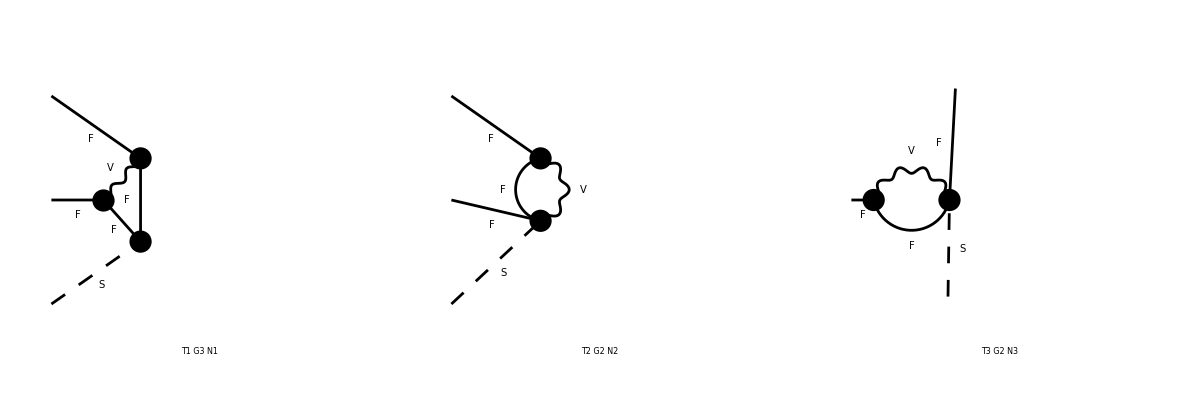

FeynArtsGraphics[{F,F,S}→{}][([T1 G3 N1] | [T2 G2 N2] | [T3 G2 N3]
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[INTopo,PaintLevel->Generic]
```

```mathematica
Length[Ampl]
```

3

```mathematica
Ampl[[1,4]]
```

{Mass[F[Gen1],External],Mass[F[Gen2],External],Mass[F[Gen5],Loop],Mass[F[Gen6],Loop],Mass[V[Gen4],Loop],G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])],G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])],G_FFV^(0)[ga[KI1[3]].(omSubscript[-])],G_FFV^(0)[ga[KI1[3]].(omSubscript[+])],G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])],G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])],G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])],G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])],G_FFS^(0)[omSubscript[-]],G_FFS^(0)[omSubscript[+]],G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])],G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])],G_FFV^(0)[ga[KI1[3]].(omSubscript[-])],G_FFV^(0)[ga[KI1[3]].(omSubscript[+])],G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])],G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])],G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])],G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])],RelativeCF}→Insertions[Classes][{0,0,0,MT,0,0,0,ⅈ gc129 SUNT[Glu4,Col1,Col4],ⅈ gc129 SUNT[Glu4,Col1,Col4],0,0,0,0,0,ⅈ gc59R,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,MT,0,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,ⅈ gc44,0,0,0,ⅈ gc129 SUNT[Glu4,Col4,Col2],ⅈ gc129 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,0,MT,0,0,0,ⅈ gc129 SUNT[Glu4,Col1,Col4],ⅈ gc129 SUNT[Glu4,Col1,Col4],0,0,0,0,0,ⅈ gc59R,0,0,ⅈ gc128 SUNT[Glu4,Col4,Col2],ⅈ gc128 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,MT,0,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,ⅈ gc44,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,0,MT,0,0,0,-ⅈ gc129 SUNT[Glu4,Col4,Col1],-ⅈ gc129 SUNT[Glu4,Col4,Col1],0,0,0,0,ⅈ gc44,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,MT,0,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,ⅈ gc59R,0,0,-ⅈ gc129 SUNT[Glu4,Col2,Col4],-ⅈ gc129 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,0,MT,0,0,0,-ⅈ gc129 SUNT[Glu4,Col4,Col1],-ⅈ gc129 SUNT[Glu4,Col4,Col1],0,0,0,0,ⅈ gc44,0,0,0,-ⅈ gc128 SUNT[Glu4,Col2,Col4],-ⅈ gc128 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,MT,0,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,ⅈ gc59R,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col2,Col4])/Lambda^2,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,0,MT,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,0,ⅈ gc59R,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,MT,0,0,0,0,ⅈ gc128 SUNT[Glu4,Col1,Col4],ⅈ gc128 SUNT[Glu4,Col1,Col4],0,0,0,0,ⅈ gc44,0,0,0,ⅈ gc129 SUNT[Glu4,Col4,Col2],ⅈ gc129 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,MT,0,MT,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,0,ⅈ gc59R,0,0,ⅈ gc128 SUNT[Glu4,Col4,Col2],ⅈ gc128 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,MT,MT,0,0,0,0,ⅈ gc128 SUNT[Glu4,Col1,Col4],ⅈ gc128 SUNT[Glu4,Col1,Col4],0,0,0,0,ⅈ gc44,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,0,MT,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col4,Col1])/Lambda^2,ⅈ gc44,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,MT,0,0,0,0,-ⅈ gc128 SUNT[Glu4,Col4,Col1],-ⅈ gc128 SUNT[Glu4,Col4,Col1],0,0,0,0,0,ⅈ gc59R,0,0,-ⅈ gc129 SUNT[Glu4,Col2,Col4],-ⅈ gc129 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,MT,0,MT,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col4,Col1])/Lambda^2,ⅈ gc44,0,0,0,-ⅈ gc128 SUNT[Glu4,Col2,Col4],-ⅈ gc128 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,MT,MT,0,0,0,0,-ⅈ gc128 SUNT[Glu4,Col4,Col1],-ⅈ gc128 SUNT[Glu4,Col4,Col1],0,0,0,0,0,ⅈ gc59R,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col2,Col4])/Lambda^2,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,MT,MT,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,ⅈ gc42,ⅈ gc42,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,MT,MT,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,gc41L,gc41R,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,MT,MT,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,ⅈ gc42,ⅈ gc42,0,0,ⅈ gc128 SUNT[Glu4,Col4,Col2],ⅈ gc128 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,MT,MT,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,gc41L,gc41R,0,0,ⅈ gc128 SUNT[Glu4,Col4,Col2],ⅈ gc128 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,MT,MT,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,ⅈ gc42,ⅈ gc42,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,MT,MT,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,gc41L,gc41R,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,MT,MT,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,ⅈ gc42,ⅈ gc42,0,0,-ⅈ gc128 SUNT[Glu4,Col2,Col4],-ⅈ gc128 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,MT,MT,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,gc41L,gc41R,0,0,-ⅈ gc128 SUNT[Glu4,Col2,Col4],-ⅈ gc128 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,MT,MT,0,0,0,ⅈ gc128 SUNT[Glu4,Col1,Col4],ⅈ gc128 SUNT[Glu4,Col1,Col4],0,0,0,0,ⅈ gc42,ⅈ gc42,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,MT,MT,0,0,0,ⅈ gc128 SUNT[Glu4,Col1,Col4],ⅈ gc128 SUNT[Glu4,Col1,Col4],0,0,0,0,gc41L,gc41R,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,MT,MT,MT,0,0,0,ⅈ gc128 SUNT[Glu4,Col1,Col4],ⅈ gc128 SUNT[Glu4,Col1,Col4],0,0,0,0,ⅈ gc42,ⅈ gc42,0,0,ⅈ gc128 SUNT[Glu4,Col4,Col2],ⅈ gc128 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,MT,MT,MT,0,0,0,ⅈ gc128 SUNT[Glu4,Col1,Col4],ⅈ gc128 SUNT[Glu4,Col1,Col4],0,0,0,0,gc41L,gc41R,0,0,ⅈ gc128 SUNT[Glu4,Col4,Col2],ⅈ gc128 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,MT,MT,0,0,0,-ⅈ gc128 SUNT[Glu4,Col4,Col1],-ⅈ gc128 SUNT[Glu4,Col4,Col1],0,0,0,0,ⅈ gc42,ⅈ gc42,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,MT,MT,0,0,0,-ⅈ gc128 SUNT[Glu4,Col4,Col1],-ⅈ gc128 SUNT[Glu4,Col4,Col1],0,0,0,0,gc41L,gc41R,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,MT,MT,MT,0,0,0,-ⅈ gc128 SUNT[Glu4,Col4,Col1],-ⅈ gc128 SUNT[Glu4,Col4,Col1],0,0,0,0,ⅈ gc42,ⅈ gc42,0,0,-ⅈ gc128 SUNT[Glu4,Col2,Col4],-ⅈ gc128 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,MT,MT,MT,0,0,0,-ⅈ gc128 SUNT[Glu4,Col4,Col1],-ⅈ gc128 SUNT[Glu4,Col4,Col1],0,0,0,0,gc41L,gc41R,0,0,-ⅈ gc128 SUNT[Glu4,Col2,Col4],-ⅈ gc128 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,MT,0,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col1,Col4])/Lambda^2,0,0,gc43,0,0,0,ⅈ gc139 SUNT[Glu4,Col4,Col2],ⅈ gc139 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,MT,0,0,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col1])/Lambda^2,0,0,gc70R,0,0,-ⅈ gc139 SUNT[Glu4,Col2,Col4],-ⅈ gc139 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,MT,0,0,0,0,ⅈ gc128 SUNT[Glu4,Col1,Col4],ⅈ gc128 SUNT[Glu4,Col1,Col4],0,0,0,0,gc43,0,0,0,ⅈ gc139 SUNT[Glu4,Col4,Col2],ⅈ gc139 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{MT,0,MT,0,0,0,0,-ⅈ gc128 SUNT[Glu4,Col4,Col1],-ⅈ gc128 SUNT[Glu4,Col4,Col1],0,0,0,0,0,gc70R,0,0,-ⅈ gc139 SUNT[Glu4,Col2,Col4],-ⅈ gc139 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,0,MT,0,0,0,ⅈ gc139 SUNT[Glu4,Col1,Col4],ⅈ gc139 SUNT[Glu4,Col1,Col4],0,0,0,0,0,gc70R,(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,-(2 ⅈ √2 GS vev (CtGSuperscript[*]) SUNT[Glu4,Col4,Col2])/Lambda^2,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,0,MT,0,0,0,ⅈ gc139 SUNT[Glu4,Col1,Col4],ⅈ gc139 SUNT[Glu4,Col1,Col4],0,0,0,0,0,gc70R,0,0,ⅈ gc128 SUNT[Glu4,Col4,Col2],ⅈ gc128 SUNT[Glu4,Col4,Col2],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,0,0,MT,0,0,0,-ⅈ gc139 SUNT[Glu4,Col4,Col1],-ⅈ gc139 SUNT[Glu4,Col4,Col1],0,0,0,0,gc43,0,0,(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,0,0,0,0,0,-(2 ⅈ √2 CtG GS vev SUNT[Glu4,Col2,Col4])/Lambda^2,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]},{0,MT,0,MT,0,0,0,-ⅈ gc139 SUNT[Glu4,Col4,Col1],-ⅈ gc139 SUNT[Glu4,Col4,Col1],0,0,0,0,gc43,0,0,0,-ⅈ gc128 SUNT[Glu4,Col2,Col4],-ⅈ gc128 SUNT[Glu4,Col2,Col4],0,0,0,0,SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External]}]

```mathematica
Ampl[[1,3]]/.rep
```

-1/(16 π^4)RelativeCF v̄[p1,Mass[F[Gen1],External]].(ga[Lor1].(omSubscript[-]) G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+ga[Lor1].(omSubscript[+]) G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]).(gs[p2+p3+q1]+Mass[F[Gen5],Loop]).((omSubscript[-]) G_FFS^(0)[omSubscript[-]]+(omSubscript[+]) G_FFS^(0)[omSubscript[+]]).(gs[p2+q1]+Mass[F[Gen6],Loop]).(ga[Lor2].(omSubscript[-]) G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+ga[Lor2].(omSubscript[+]) G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]).u[p2,Mass[F[Gen2],External]] FeynAmpDenominator[1/((q1)^2-Mass[V[Gen4],Loop]^2),1/((p2+q1)^2-Mass[F[Gen6],Loop]^2),1/((p2+p3+q1)^2-Mass[F[Gen5],Loop]^2)] g[Lor1,Lor2]

```mathematica
rep=Union[(Rule[#,0]&)/@Cases[Ampl[[1,3,4,2]],G[-1][0][x__][z__?(Not[FreeQ[#,Mom]]&)],∞],(Rule[#,0]&)/@Cases[Ampl[[1,3,4,6]],G[-1][0][x__][z__?(Not[FreeQ[#,Mom]]&)],∞]]
```

{G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]→0,G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]→0,G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]→0,G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]→0,G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])]→0,G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]→0,G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]→0,G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]→0,G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]→0,G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]→0,G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])]→0,G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]→0}

```mathematica
test=GetR2[Ampl[[1]],3]
```

after total expand

2238

-1/(96 FR$Eps π^2)ⅈ RelativeCF (4 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]-3 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]-12 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]+2 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]+6 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]+4 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]-3 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]-12 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]+2 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+6 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+20 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+24 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]-16 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]-12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+3 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+24 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+48 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-18 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-24 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-2 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-6 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+2 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+6 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+3 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-24 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-48 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+10 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+20 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+24 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+24 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]+48 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-14 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-24 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-16 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-18 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-24 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]-2 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]+18 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]+24 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]+14 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]+24 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]-2 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]+18 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]+24 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]+10 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])]+2 v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] (-((FR$Eps FR$R2+3 FR$UV) G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[+])]-(5 FR$Eps FR$R2+6 FR$UV) G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[+])]+(7 FR$Eps FR$R2+12 FR$UV) G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]) G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] ((FR$Eps FR$R2+3 FR$UV) G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]+(7 FR$Eps FR$R2+12 FR$UV) G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]-(5 FR$Eps FR$R2+6 FR$UV) G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])]))-3 v̄[p1,Mass[F[Gen1],External]].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] (8 (FR$Eps FR$R2+2 FR$UV) G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+Mass[F[Gen6],Loop] (-((FR$Eps FR$R2+4 FR$UV) G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]+8 (FR$Eps FR$R2+2 FR$UV) G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]-2 (3 FR$Eps FR$R2+4 FR$UV) G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])]) G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] ((FR$Eps FR$R2+4 FR$UV) G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]-2 (3 FR$Eps FR$R2+4 FR$UV) G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]+8 (FR$Eps FR$R2+2 FR$UV) G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])]))+Mass[F[Gen5],Loop] (-((FR$Eps FR$R2+4 FR$UV) G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]+8 (FR$Eps FR$R2+2 FR$UV) G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]-2 (3 FR$Eps FR$R2+4 FR$UV) G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])]) G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[+]] ((FR$Eps FR$R2+4 FR$UV) G_FFV^(0)[Mom[3][KI1[3]] (omSubscript[-])]-2 (3 FR$Eps FR$R2+4 FR$UV) G_FFV^(0)[ga[KI1[3]].gs[Mom[3]].(omSubscript[-])]+8 (FR$Eps FR$R2+2 FR$UV) G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[-])])))-24 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]-48 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen5],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]-10 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]-12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p2].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]+10 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]+12 FR$UV v̄[p1,Mass[F[Gen1],External]].gs[p3].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]-24 FR$Eps FR$R2 v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])]-48 FR$UV v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] Mass[F[Gen6],Loop] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[gs[Mom[3]].ga[KI1[3]].(omSubscript[+])])

```mathematica
Simplify[Coefficient[test,FR$UV]/.rep]/.FR$Eps->-2FR$Eps
```

-1/(4 FR$Eps π^2)ⅈ RelativeCF (v̄[p1,Mass[F[Gen1],External]].(omSubscript[-]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFS^(0)[omSubscript[-]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+v̄[p1,Mass[F[Gen1],External]].(omSubscript[+]).u[p2,Mass[F[Gen2],External]] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFS^(0)[omSubscript[+]] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])])

```mathematica
r2=R2atClass[Ampl,INTopo,{F,F,S},False,{},True];
```

after total expand

2238

after total expand

168

after total expand

76

```mathematica
Coefficient[Normal[Series[Coefficient[r2/.CtG->0,FR$UV],{Lambda,∞,2}]]/.Lambda->1/invL,invL,2]
```

1/(4 FR$Eps π^2)(√2 Ctphi GS^2 vev^2 v̄[p1,0].(omSubscript[+]).u[p2,MT] SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External] SUNT[Glu4,Col1,Col4] SUNT[Glu4,Col4,Col2] SWF[S[1],3]+√2 GS^2 vev^2 (CtphiSuperscript[*]) v̄[p1,MT].(omSubscript[-]).u[p2,0] SumOver[Col4,3] SumOver[Glu4,8] SumOver[Col1,3,External] SumOver[Col2,3,External] SUNT[Glu4,Col1,Col4] SUNT[Glu4,Col4,Col2] SWF[S[1],3])

```mathematica
Cases[r2,G[__][__][__][__],∞]
```

{}

```mathematica
vertlist=R2vertlist[ExpandAll[r2]];
```

```mathematica
vertlist[[28,1]]
```

{{-F[7,{ColExt[1]}],1},{F[9,{ColExt[2]}],2},{V[4,{GluExt[3]}],3}}

```mathematica
res=ExpandAll[vertlist[[1,2]]/.{SUNF->SUF,SUNT->SUT}];
```

```mathematica
Simplify[res/.yd[__]->0]
```

1/(128 π^2)GS^2 IndexDelta[GluExt[1],GluExt[2]] SumOver[GluExt[1],8,External] SumOver[GluExt[2],8,External] (-22 GH (p2)[LorExt[1]] (p2)[LorExt[2]]+4 GH (-(p1))[LorExt[2]] (p3)[LorExt[1]]+GH (-(p2))[LorExt[2]] (p3)[LorExt[1]]-33 GH (p2)[LorExt[1]] (p3)[LorExt[2]]-12 GH (-(p3))[LorExt[1]] (p3)[LorExt[2]]-10 GH (p3)[LorExt[1]] (p3)[LorExt[2]]-4 GH g[LorExt[1],LorExt[2]] SP[p1,p2]+4 GH g[LorExt[1],LorExt[2]] SP[p1,p3]+41 GH g[LorExt[1],LorExt[2]] SP[p2,p2]+45 GH g[LorExt[1],LorExt[2]] SP[p2,p3]+17 GH g[LorExt[1],LorExt[2]] SP[p3,p3]+4 √2 (yu[Gen4,Gen4]Superscript[*]) g[LorExt[1],LorExt[2]] Mu[Gen4,Col4] SumOver[Gen4,3]-8 √2 (yu[Gen4,Gen4]Superscript[*]) g[LorExt[1],LorExt[2]] Mu[Gen4,Col5] SumOver[Gen4,3]+4 √2 g[LorExt[1],LorExt[2]] Mu[Gen4,Col4] SumOver[Gen4,3] yu[Gen4,Gen4]-8 √2 g[LorExt[1],LorExt[2]] Mu[Gen4,Col5] SumOver[Gen4,3] yu[Gen4,Gen4]-36 ⅈ g[LorExt[1],LorExt[2]] SP[p3,p3] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+28 ⅈ (-(p1))[LorExt[2]] (p2)[LorExt[1]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]-4 ⅈ (-(p1))[LorExt[1]] (p2)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]-4 ⅈ (p1)[LorExt[1]] (p2)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]-16 ⅈ (p2)[LorExt[1]] (p2)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]-4 ⅈ (-(p1))[LorExt[2]] (p3)[LorExt[1]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]-20 ⅈ (-(p2))[LorExt[2]] (p3)[LorExt[1]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]-30 ⅈ (p2)[LorExt[2]] (p3)[LorExt[1]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+4 ⅈ (-(p1))[LorExt[1]] (p3)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+4 ⅈ (p1)[LorExt[1]] (p3)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+14 ⅈ (p2)[LorExt[1]] (p3)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+20 ⅈ (-(p3))[LorExt[1]] (p3)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+12 ⅈ (p3)[LorExt[1]] (p3)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+36 ⅈ g[LorExt[1],LorExt[2]] SP[p1,p2] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+22 ⅈ g[LorExt[1],LorExt[2]] SP[p2,p2] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+22 ⅈ g[LorExt[1],LorExt[2]] SP[p2,p3] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+66 ⅈ g[LorExt[1],LorExt[2]] SP[p3,p3] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]+4 (p1)[LorExt[2]] ((p2)[LorExt[1]] (GH-2 ⅈ G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]])-ⅈ (p3)[LorExt[1]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]])+4 (-(p2))[LorExt[1]] (2 (p2)[LorExt[2]] (GH-ⅈ G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]])+3 ⅈ (p3)[LorExt[2]] G_SVV^(0)[g[KI1[2],KI1[3]] SP[Mom[2],Mom[3]]]))

## Test

```mathematica
Quit[]
```

```mathematica
SetDirectory["~/celine/FeynArts-3.7"];
<< FeynArts`
SetDirectory["~/celine/feynrules/trunk/feynrules-development/R2"];
<< R2EFT`
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 11 Jul 12

- R2 -

Version: 0.2.1

Authors: C. Degrande

```mathematica
WriteR2["TopFCNC/TopFCNC","TopFCNC/TopFCNC","TopFCNC",LabelInternal->True,QCDonly->True,KeptIndices->{}]//Timing
```

1

loading generic model file /Users/omatt/celine/FeynArts-3.7/Models/TopFCNC/TopFCNC.gen

> $SVMixing is OFF

generic model {TopFCNC/TopFCNC} initialized

loading classes model file /Users/omatt/celine/FeynArts-3.7/Models/TopFCNC/TopFCNC.mod

> 43 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 163 vertices

> 297 counter terms of order 1

classes model {TopFCNC/TopFCNC} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 4 Generic, 14 Classes insertions

in total: 4 Generic, 14 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

FA finished after 0.783283

R2atClass finished after 0.783446

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

R2vertlist finished after 0.787297

Expand finished after 0.787405

SU3 finished after 0.787832

length tmp = 0

Simplify finished after 0.787906

{S} finished after 0.787994

2

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 16 Classes insertions

> Top. 2: 2 Generic, 114 Classes insertions

in total: 4 Generic, 130 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 4 Classes amplitudes

> Top. 2: 1 Generic, 24 Classes amplitudes

in total: 2 Generic, 28 Classes amplitudes

FA finished after 1.455118

after total expand

6

after total expand

162

R2atClass finished after 6.963909

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes insertions

in total: 1 Generic, 36 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes amplitudes

in total: 1 Generic, 36 Classes amplitudes

R2vertlist finished after 7.504338

Expand finished after 7.632010

SU3 finished after 7.653178

before CTSol

1 is {{-F[7, {ColExt[1]}], 1}, {F[7, {ColExt[2]}], 2}}

ToSolve[{(12*FR$Eps*Pi^2*FR$deltaZ[{u, u}, {{}}, "L"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[7, {}], V[4, {}]}])/FR$Eps == 0, True, (6*FR$Eps*Pi^2*FR$deltaZ[{u, u}, {{}}, "L"] + 6*FR$Eps*Pi^2*FR$deltaZ[{u, u}, {{}}, "R"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[7, {}], V[4, {}]}])/FR$Eps == 0}, {FR$deltaZ[{u, u}, {{}}, "L"], FR$deltaZ[{u, u}, {{}}, "R"]}]

solve done

2 is {{-F[7, {ColExt[1]}], 1}, {F[8, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{c, u}, {{}}, "L"]] + FR$deltaZ[{u, c}, {{}}, "L"] == 0, True}, {FR$deltaZ[{c, u}, {{}}, "L"], FR$deltaZ[{u, c}, {{}}, "L"]}]

solve done

3 is {{-F[8, {ColExt[1]}], 1}, {F[7, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{c, u}, {{}}, "L"]] + FR$deltaZ[{u, c}, {{}}, "L"] == 0, True, Conjugate[FR$deltaZ[{u, c}, {{}}, "L"]] + FR$deltaZ[{c, u}, {{}}, "L"] == 0, True}, {FR$deltaZ[{c, u}, {{}}, "L"], FR$deltaZ[{u, c}, {{}}, "L"]}]

Solve::svars: Equations may not give solutions for all "solve" variables.

solve done

4 is {{-F[9, {ColExt[1]}], 1}, {F[7, {ColExt[2]}], 2}}

Simplify::time: Time spent on a transformation exceeded 0.02 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

ToSolve[{(MT*(12*Lambda^2*Pi^2*Conjugate[FR$deltaZ[{u, t}, {{}}, "L"]] + 12*Lambda^2*Pi^2*FR$deltaZ[{t, u}, {{}}, "L"] - 12*Lambda^2*Pi^2*FR$deltaZ[{t, u}, {{}}, "R"] + Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}] + (12*Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}])/FR$Eps + 12*Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}]*ReInt$1592[Log[MT/FR$MU]]))/(4*Lambda) == 0, (MT*(6*FR$Eps*Lambda^2*Pi^2*Conjugate[FR$deltaZ[{u, t}, {{}}, "R"]] - 6*FR$Eps*Lambda^2*Pi^2*FR$deltaZ[{t, u}, {{}}, "L"] + 6*FR$Eps*Lambda^2*Pi^2*FR$deltaZ[{t, u}, {{}}, "R"] - 6*Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[7, {}], V[4, {}]}] + 4*Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*IPL[{F[7, {}], V[4, {}]}] + 6*Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}] - Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}] + 6*Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}]*ReInt$1592[Log[MT/FR$MU]] - 3*Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*Cond$1592[Element[MT^2, Reals], 0, 1]*IPL[{F[7, {}], V[4, {}]}]*ReInt$1592[Log[-(MT^2/FR$MU^2)]] - 3*Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*Cond$1592[Element[MT^2, Reals], 1, 0]*IPL[{F[7, {}], V[4, {}]}]*ReInt$1592[Log[MT^2/FR$MU^2]]))/(FR$Eps*Lambda) == 0}, {FR$deltaZ[{t, u}, {{}}, "L"], FR$deltaZ[{t, u}, {{}}, "R"], FR$deltaZ[{u, t}, {{}}, "L"], FR$deltaZ[{u, t}, {{}}, "R"]}]

solve done

5 is {{-F[7, {ColExt[1]}], 1}, {F[9, {ColExt[2]}], 2}}

Simplify::time: Time spent on a transformation exceeded 0.02 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: time will be suppressed during this calculation.

ToSolve[{(MT*(12*Lambda^2*Pi^2*Conjugate[FR$deltaZ[{u, t}, {{}}, "L"]] + 12*Lambda^2*Pi^2*FR$deltaZ[{t, u}, {{}}, "L"] - 12*Lambda^2*Pi^2*FR$deltaZ[{t, u}, {{}}, "R"] + Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}] + (12*Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}])/FR$Eps + 12*Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}]*ReInt$1592[Log[MT/FR$MU]]))/(4*Lambda) == 0, (MT*(6*FR$Eps*Lambda^2*Pi^2*Conjugate[FR$deltaZ[{u, t}, {{}}, "R"]] - 6*FR$Eps*Lambda^2*Pi^2*FR$deltaZ[{t, u}, {{}}, "L"] + 6*FR$Eps*Lambda^2*Pi^2*FR$deltaZ[{t, u}, {{}}, "R"] - 6*Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[7, {}], V[4, {}]}] + 4*Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*IPL[{F[7, {}], V[4, {}]}] + 6*Sqrt[2]*CtG*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}] - Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}] + 6*Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*IPL[{F[9, {}], V[4, {}]}]*ReInt$1592[Log[MT/FR$MU]] - 3*Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*Cond$1592[Element[MT^2, Reals], 0, 1]*IPL[{F[7, {}], V[4, {}]}]*ReInt$1592[Log[-(MT^2/FR$MU^2)]] - 3*Sqrt[2]*CtG*FR$Eps*gs^2*MT*vev*Cond$1592[Element[MT^2, Reals], 1, 0]*IPL[{F[7, {}], V[4, {}]}]*ReInt$1592[Log[MT^2/FR$MU^2]]))/(FR$Eps*Lambda) == 0, (MT*(6*FR$Eps*Lambda^2*Pi^2*Conjugate[FR$deltaZ[{t, u}, {{}}, "L"]] + Sqrt[2]*CtG*gs^2*MT*vev*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*ReInt$1592[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*Cond$1592[Element[MT^2, Reals], 0, 1]*ReInt$1592[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*Cond$1592[Element[MT^2, Reals], 1, 0]*ReInt$1592[Log[MT^2/FR$MU^2]]))))/(FR$Eps*Lambda) == 0, MT*Conjugate[FR$deltaZ[{t, u}, {{}}, "R"]] == 0}, {FR$deltaZ[{t, u}, {{}}, "L"], FR$deltaZ[{t, u}, {{}}, "R"], FR$deltaZ[{u, t}, {{}}, "L"], FR$deltaZ[{u, t}, {{}}, "R"]}]

solve done

6 is {{-F[8, {ColExt[1]}], 1}, {F[8, {ColExt[2]}], 2}}

ToSolve[{(12*FR$Eps*Pi^2*FR$deltaZ[{c, c}, {{}}, "L"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[8, {}], V[4, {}]}])/FR$Eps == 0, True, (6*FR$Eps*Pi^2*FR$deltaZ[{c, c}, {{}}, "L"] + 6*FR$Eps*Pi^2*FR$deltaZ[{c, c}, {{}}, "R"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[8, {}], V[4, {}]}])/FR$Eps == 0}, {FR$deltaZ[{c, c}, {{}}, "L"], FR$deltaZ[{c, c}, {{}}, "R"]}]

solve done

7 is {{-F[9, {ColExt[1]}], 1}, {F[8, {ColExt[2]}], 2}}

ToSolve[{MT*(Conjugate[FR$deltaZ[{c, t}, {{}}, "L"]] + FR$deltaZ[{t, c}, {{}}, "L"] - FR$deltaZ[{t, c}, {{}}, "R"]) == 0, MT*(Conjugate[FR$deltaZ[{c, t}, {{}}, "R"]] - FR$deltaZ[{t, c}, {{}}, "L"] + FR$deltaZ[{t, c}, {{}}, "R"]) == 0}, {FR$deltaZ[{c, t}, {{}}, "L"], FR$deltaZ[{c, t}, {{}}, "R"], FR$deltaZ[{t, c}, {{}}, "L"], FR$deltaZ[{t, c}, {{}}, "R"]}]

solve done

8 is {{-F[8, {ColExt[1]}], 1}, {F[9, {ColExt[2]}], 2}}

ToSolve[{MT*(Conjugate[FR$deltaZ[{c, t}, {{}}, "L"]] + FR$deltaZ[{t, c}, {{}}, "L"] - FR$deltaZ[{t, c}, {{}}, "R"]) == 0, MT*(Conjugate[FR$deltaZ[{c, t}, {{}}, "R"]] - FR$deltaZ[{t, c}, {{}}, "L"] + FR$deltaZ[{t, c}, {{}}, "R"]) == 0, MT*Conjugate[FR$deltaZ[{t, c}, {{}}, "L"]] == 0, MT*Conjugate[FR$deltaZ[{t, c}, {{}}, "R"]] == 0}, {FR$deltaZ[{c, t}, {{}}, "L"], FR$deltaZ[{c, t}, {{}}, "R"], FR$deltaZ[{t, c}, {{}}, "L"], FR$deltaZ[{t, c}, {{}}, "R"]}]

solve done

9 is {{-F[9, {ColExt[1]}], 1}, {F[9, {ColExt[2]}], 2}}

ToSolve[{(6*FR$Eps*Pi^2*FR$delta[{MT}, {}] + MT*(-3*FR$Eps*Pi^2*FR$deltaZ[{t, t}, {{}}, "L"] + 3*FR$Eps*Pi^2*FR$deltaZ[{t, t}, {{}}, "R"] + gs^2*IPL[{F[9, {}], V[4, {}]}]*(-3 + 2*FR$Eps - 3*FR$Eps*ReInt$1592[Log[MT/FR$MU]])))/FR$Eps == 0, (6*FR$Eps*Pi^2*FR$delta[{MT}, {}] + MT*(3*FR$Eps*Pi^2*FR$deltaZ[{t, t}, {{}}, "L"] - 3*FR$Eps*Pi^2*FR$deltaZ[{t, t}, {{}}, "R"] + gs^2*IPL[{F[9, {}], V[4, {}]}]*(-3 + 2*FR$Eps - 3*FR$Eps*ReInt$1592[Log[MT/FR$MU]])))/FR$Eps == 0, (3*FR$Eps*Pi^2*(FR$deltaZ[{t, t}, {{}}, "L"] + FR$deltaZ[{t, t}, {{}}, "R"])*ReInt$1592[MT^2] - gs^2*IPL[{F[9, {}], V[4, {}]}]*(2*FR$IR*MT^2 + ReInt$1592[MT^2]*(1 - FR$Eps + FR$Eps*MT^2*ReInt$1592[(3 + 2*Log[FR$MU] - 2*Log[MT])/MT^2] - 4*FR$Eps*MT^2*ReInt$1592[(1 + Log[FR$MU] - Log[MT])/MT^2] + FR$Eps*ReInt$1592[Log[MT/FR$MU]])))/(FR$Eps*ReInt$1592[MT^2]) == 0}, {FR$delta[{MT}, {}], FR$deltaZ[{t, t}, {{}}, "L"], FR$deltaZ[{t, t}, {{}}, "R"]}]

solve done

10 is {{-F[10, {ColExt[1]}], 1}, {F[10, {ColExt[2]}], 2}}

ToSolve[{(12*FR$Eps*Pi^2*FR$deltaZ[{d, d}, {{}}, "L"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[10, {}], V[4, {}]}])/FR$Eps == 0, True, (6*FR$Eps*Pi^2*FR$deltaZ[{d, d}, {{}}, "L"] + 6*FR$Eps*Pi^2*FR$deltaZ[{d, d}, {{}}, "R"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[10, {}], V[4, {}]}])/FR$Eps == 0}, {FR$deltaZ[{d, d}, {{}}, "L"], FR$deltaZ[{d, d}, {{}}, "R"]}]

solve done

11 is {{-F[11, {ColExt[1]}], 1}, {F[10, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{d, s}, {{}}, "L"]] + FR$deltaZ[{s, d}, {{}}, "L"] == 0, True}, {FR$deltaZ[{d, s}, {{}}, "L"], FR$deltaZ[{s, d}, {{}}, "L"]}]

solve done

12 is {{-F[10, {ColExt[1]}], 1}, {F[11, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{d, s}, {{}}, "L"]] + FR$deltaZ[{s, d}, {{}}, "L"] == 0, True, Conjugate[FR$deltaZ[{s, d}, {{}}, "L"]] + FR$deltaZ[{d, s}, {{}}, "L"] == 0, True}, {FR$deltaZ[{d, s}, {{}}, "L"], FR$deltaZ[{s, d}, {{}}, "L"]}]

Solve::svars: Equations may not give solutions for all "solve" variables.

solve done

13 is {{-F[10, {ColExt[1]}], 1}, {F[12, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{b, d}, {{}}, "L"]] + FR$deltaZ[{d, b}, {{}}, "L"] == 0, True}, {FR$deltaZ[{b, d}, {{}}, "L"], FR$deltaZ[{d, b}, {{}}, "L"]}]

solve done

14 is {{-F[12, {ColExt[1]}], 1}, {F[10, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{b, d}, {{}}, "L"]] + FR$deltaZ[{d, b}, {{}}, "L"] == 0, True, Conjugate[FR$deltaZ[{d, b}, {{}}, "L"]] + FR$deltaZ[{b, d}, {{}}, "L"] == 0, True}, {FR$deltaZ[{b, d}, {{}}, "L"], FR$deltaZ[{d, b}, {{}}, "L"]}]

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve :: svars will be suppressed during this calculation.

solve done

15 is {{-F[11, {ColExt[1]}], 1}, {F[11, {ColExt[2]}], 2}}

ToSolve[{(12*FR$Eps*Pi^2*FR$deltaZ[{s, s}, {{}}, "L"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[11, {}], V[4, {}]}])/FR$Eps == 0, True, (6*FR$Eps*Pi^2*FR$deltaZ[{s, s}, {{}}, "L"] + 6*FR$Eps*Pi^2*FR$deltaZ[{s, s}, {{}}, "R"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[11, {}], V[4, {}]}])/FR$Eps == 0}, {FR$deltaZ[{s, s}, {{}}, "L"], FR$deltaZ[{s, s}, {{}}, "R"]}]

solve done

16 is {{-F[11, {ColExt[1]}], 1}, {F[12, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{b, s}, {{}}, "L"]] + FR$deltaZ[{s, b}, {{}}, "L"] == 0, True}, {FR$deltaZ[{b, s}, {{}}, "L"], FR$deltaZ[{s, b}, {{}}, "L"]}]

solve done

17 is {{-F[12, {ColExt[1]}], 1}, {F[11, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{b, s}, {{}}, "L"]] + FR$deltaZ[{s, b}, {{}}, "L"] == 0, True, Conjugate[FR$deltaZ[{s, b}, {{}}, "L"]] + FR$deltaZ[{b, s}, {{}}, "L"] == 0, True}, {FR$deltaZ[{b, s}, {{}}, "L"], FR$deltaZ[{s, b}, {{}}, "L"]}]

solve done

18 is {{-F[12, {ColExt[1]}], 1}, {F[12, {ColExt[2]}], 2}}

ToSolve[{(12*FR$Eps*Pi^2*FR$deltaZ[{b, b}, {{}}, "L"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[12, {}], V[4, {}]}])/FR$Eps == 0, True, (6*FR$Eps*Pi^2*FR$deltaZ[{b, b}, {{}}, "L"] + 6*FR$Eps*Pi^2*FR$deltaZ[{b, b}, {{}}, "R"] + (2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[12, {}], V[4, {}]}])/FR$Eps == 0}, {FR$deltaZ[{b, b}, {{}}, "L"], FR$deltaZ[{b, b}, {{}}, "R"]}]

solve done

end of the for

before last simplification

end lenght tmp not 0

Simplify finished after 60.852156

{F, F} finished after 60.852630

3

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 22 Classes insertions

> Top. 2: 5 Generic, 57 Classes insertions

in total: 7 Generic, 79 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

FA finished after 61.112665

R2atClass finished after 61.112855

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

R2vertlist finished after 61.121977

Expand finished after 61.122098

SU3 finished after 61.122309

length tmp = 0

Simplify finished after 61.122378

{S, S} finished after 61.122813

4

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 23 Classes insertions

> Top. 2: 5 Generic, 133 Classes insertions

in total: 7 Generic, 156 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

> Top. 2: 3 Generic, 34 Classes amplitudes

in total: 4 Generic, 35 Classes amplitudes

FA finished after 62.007117

after total expand

3

after total expand

190

after total expand

35

after total expand

137

R2atClass finished after 74.429712

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

R2vertlist finished after 74.618909

Expand finished after 74.652147

SU3 finished after 74.661756

before CTSol

1 is {{V[4, {GluExt[1]}], 1}, {V[4, {GluExt[2]}], 2}}

ToSolve[{(IndexDelta[Index[Gluon, Ext[1]], Index[Gluon, Ext[2]]]*(192*FR$Eps*Pi^2*FR$deltaZ[{G, G}, {}] + gs^2*(16*(-1 + FR$IR)*IPL[{F[7, {}]}] + 16*(-1 + FR$IR)*IPL[{F[8, {}]}] - 16*IPL[{F[9, {}]}] - 16*IPL[{F[10, {}]}] + 16*FR$IR*IPL[{F[10, {}]}] - 16*IPL[{F[11, {}]}] + 16*FR$IR*IPL[{F[11, {}]}] - 16*IPL[{F[12, {}]}] + 16*FR$IR*IPL[{F[12, {}]}] + 6*IPL[{U[5, {}]}] - 3*FR$Eps*IPL[{U[5, {}]}] - 6*FR$IR*IPL[{U[5, {}]}] + 3*FR$Eps*FR$IR*IPL[{U[5, {}]}] + 114*IPL[{V[4, {}]}] + 9*FR$Eps*IPL[{V[4, {}]}] - 114*FR$IR*IPL[{V[4, {}]}] - 9*FR$Eps*FR$IR*IPL[{V[4, {}]}] - 16*FR$Eps*IPL[{F[9, {}]}]*ReInt$6980[Log[MT/FR$MU]])))/FR$Eps == 0}, {FR$deltaZ[{G, G}, {}]}]

solve done

end of the for

before last simplification

end lenght tmp not 0

Simplify finished after 76.354516

{V, V} finished after 76.355042

5

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 420 Classes insertions

> Top. 2: 2 Generic, 46 Classes insertions

> Top. 3: 2 Generic, 46 Classes insertions

> Top. 4: 1 Generic, 20 Classes insertions

in total: 11 Generic, 532 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 40 Classes amplitudes

> Top. 2: 1 Generic, 22 Classes amplitudes

> Top. 3: 1 Generic, 22 Classes amplitudes

in total: 3 Generic, 84 Classes amplitudes

FA finished after 84.599631

after total expand

2238

after total expand

168

after total expand

76

R2atClass finished after 179.284799

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 46 Classes insertions

in total: 1 Generic, 46 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 46 Classes amplitudes

in total: 1 Generic, 46 Classes amplitudes

R2vertlist finished after 180.076794

Expand finished after 180.218213

SU3 finished after 180.241168

end lenght tmp not 0

Simplify finished after 182.274708

{F, F, S} finished after 182.275786

6

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 678 Classes insertions

> Top. 2: 2 Generic, 18 Classes insertions

> Top. 3: 2 Generic, 18 Classes insertions

> Top. 4: 2 Generic, 20 Classes insertions

in total: 12 Generic, 734 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 3 Generic, 204 Classes amplitudes

> Top. 2: 2 Generic, 18 Classes amplitudes

> Top. 3: 2 Generic, 18 Classes amplitudes

> Top. 4: 1 Generic, 4 Classes amplitudes

in total: 8 Generic, 244 Classes amplitudes

FA finished after 195.693999

after total expand

406

after total expand

5370

after total expand

7832

after total expand

26

after total expand

44

after total expand

18

after total expand

32

after total expand

72

R2atClass finished after 1269.531093

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 144 Classes insertions

in total: 1 Generic, 144 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 144 Classes amplitudes

in total: 1 Generic, 144 Classes amplitudes

R2vertlist finished after 1272.500277

Expand finished after 1287.005361

SU3 finished after 1287.080531

end lenght tmp not 0

Simplify finished after 1295.051375

{F, F, V} finished after 1295.054281

7

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 979 Classes insertions

> Top. 2: 3 Generic, 59 Classes insertions

> Top. 3: 3 Generic, 59 Classes insertions

> Top. 4: 3 Generic, 59 Classes insertions

in total: 19 Generic, 1156 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 3 Generic, 303 Classes amplitudes

> Top. 2: 2 Generic, 3 Classes amplitudes

> Top. 3: 2 Generic, 3 Classes amplitudes

> Top. 4: 2 Generic, 3 Classes amplitudes

in total: 9 Generic, 312 Classes amplitudes

FA finished after 1303.471348

after total expand

7266

after total expand

1064

after total expand

7974

after total expand

184

after total expand

54

after total expand

102

after total expand

36

after total expand

102

after total expand

36

R2atClass finished after 5732.933004

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

R2vertlist finished after 5735.413667

Expand finished after 5741.977260

SU3 finished after 5742.271770

end lenght tmp not 0

Simplify finished after 5749.351005

{V, V, V} finished after 5749.359651

8

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 494 Classes insertions

> Top. 2: 2 Generic, 49 Classes insertions

> Top. 3: 2 Generic, 49 Classes insertions

> Top. 4: 3 Generic, 46 Classes insertions

in total: 17 Generic, 638 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 56 Classes amplitudes

> Top. 2: 1 Generic, 4 Classes amplitudes

> Top. 3: 1 Generic, 4 Classes amplitudes

> Top. 4: 1 Generic, 2 Classes amplitudes

in total: 4 Generic, 66 Classes amplitudes

FA finished after 5758.436665

after total expand

3178

after total expand

126

after total expand

102

after total expand

48

R2atClass finished after 6147.623492

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

R2vertlist finished after 6147.807886

Expand finished after 6147.840924

SU3 finished after 6147.845054

end lenght tmp not 0

Simplify finished after 6148.337520

{V, V, S} finished after 6148.342276

9

inserting at level(s) {Generic,Classes}

> Top. 1: 4 Generic, 472 Classes insertions

> Top. 2: 5 Generic, 340 Classes insertions

> Top. 3: 4 Generic, 98 Classes insertions

> Top. 4: 5 Generic, 340 Classes insertions

> Top. 5: 4 Generic, 98 Classes insertions

> Top. 6: 2 Generic, 172 Classes insertions

> Top. 7: 10 Generic, 2334 Classes insertions

> Top. 8: 10 Generic, 2334 Classes insertions

> Top. 9: 8 Generic, 1442 Classes insertions

> Top. 10: 0 Generic, 0 Classes insertions

> Top. 11: 2 Generic, 34 Classes insertions

> Top. 12: 2 Generic, 34 Classes insertions

in total: 56 Generic, 7698 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 88 Classes amplitudes

> Top. 2: 3 Generic, 166 Classes amplitudes

> Top. 3: 4 Generic, 98 Classes amplitudes

> Top. 4: 3 Generic, 166 Classes amplitudes

> Top. 5: 4 Generic, 98 Classes amplitudes

> Top. 6: 2 Generic, 296 Classes amplitudes

> Top. 7: 2 Generic, 296 Classes amplitudes

> Top. 8: 5 Generic, 296 Classes amplitudes

> Top. 9: 2 Generic, 34 Classes amplitudes

> Top. 10: 2 Generic, 34 Classes amplitudes

in total: 29 Generic, 1572 Classes amplitudes

FA finished after 6472.389559

after total expand

456

after total expand

1310

after total expand

98

after total expand

4440

after total expand

7438

after total expand

240

after total expand

58

after total expand

396

after total expand

346

after total expand

48

after total expand

1280

after total expand

2272

after total expand

120

after total expand

30

after total expand

204

after total expand

150

after total expand

6900

after total expand

123218

after total expand

6612

after total expand

121492

after total expand

662

after total expand

29036

after total expand

32548

after total expand

16862

after total expand

179034

after total expand

0

after total expand

0

after total expand

0

after total expand

0

R2atClass finished after 12663.878862

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 52 Classes insertions

in total: 1 Generic, 52 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 52 Classes amplitudes

in total: 1 Generic, 52 Classes amplitudes

R2vertlist finished after 12672.378899

Expand finished after 12728.842784

SU3 finished after 12729.048608

end lenght tmp not 0

Simplify finished after 12743.668389

{F, F, V, S} finished after 12743.675017

{FR$deltaZ[{u, u}, {{}}, "L"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[7, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{u, u}, {{}}, "R"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[7, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{c, u}, {{}}, "L"] -> 0, FR$deltaZ[{u, c}, {{}}, "L"] -> 0, FR$deltaZ[{c, u}, {{}}, "R"] -> 0, FR$deltaZ[{u, c}, {{}}, "R"] -> 0, FR$deltaZ[{t, u}, {{}}, "L"] -> -(Conjugate[gs]^2*Conjugate[CtG*MT*vev*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*Re[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*If[Element[MT^2, Reals], 0, 1]*Re[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*If[Element[MT^2, Reals], 1, 0]*Re[Log[MT^2/FR$MU^2]]))])/(3*Sqrt[2]*Pi^2*Conjugate[FR$Eps]*Conjugate[Lambda]^2), FR$deltaZ[{t, u}, {{}}, "R"] -> 0, FR$deltaZ[{u, t}, {{}}, "L"] -> (-(FR$Eps*Lambda^2*Conjugate[gs]^2*Conjugate[CtG*MT*vev*IPL[{F[9, {}], V[4, {}]}]]*(12 + Conjugate[FR$Eps] + 12*Conjugate[FR$Eps]*Re[Log[MT/FR$MU]])) + 2*CtG*gs^2*MT*vev*Conjugate[FR$Eps]*Conjugate[Lambda]^2*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*Re[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*If[Element[MT^2, Reals], 0, 1]*Re[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*If[Element[MT^2, Reals], 1, 0]*Re[Log[MT^2/FR$MU^2]])))/(6*Sqrt[2]*FR$Eps*Lambda^2*Pi^2*Conjugate[FR$Eps]*Conjugate[Lambda]^2), FR$deltaZ[{u, t}, {{}}, "R"] -> (FR$Eps*Lambda^2*Conjugate[gs]^2*Conjugate[CtG*MT*vev*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*Re[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*If[Element[MT^2, Reals], 0, 1]*Re[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*If[Element[MT^2, Reals], 1, 0]*Re[Log[MT^2/FR$MU^2]]))] - CtG*gs^2*MT*vev*Conjugate[FR$Eps]*Conjugate[Lambda]^2*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*Re[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*If[Element[MT^2, Reals], 0, 1]*Re[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*If[Element[MT^2, Reals], 1, 0]*Re[Log[MT^2/FR$MU^2]])))/(3*Sqrt[2]*FR$Eps*Lambda^2*Pi^2*Conjugate[FR$Eps]*Conjugate[Lambda]^2), FR$deltaZ[{c, c}, {{}}, "L"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[8, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{c, c}, {{}}, "R"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[8, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{c, t}, {{}}, "L"] -> 0, FR$deltaZ[{c, t}, {{}}, "R"] -> 0, FR$deltaZ[{t, c}, {{}}, "L"] -> 0, FR$deltaZ[{t, c}, {{}}, "R"] -> 0, FR$delta[{MT}, {}] -> (gs^2*MT*IPL[{F[9, {}], V[4, {}]}]*(3 - 2*FR$Eps + 3*FR$Eps*Re[Log[MT/FR$MU]]))/(6*FR$Eps*Pi^2), FR$deltaZ[{t, t}, {{}}, "L"] -> (gs^2*IPL[{F[9, {}], V[4, {}]}]*(2*FR$IR*MT^2 + Re[MT^2]*(1 - FR$Eps + FR$Eps*MT^2*Re[(3 + 2*Log[FR$MU] - 2*Log[MT])/MT^2] - 4*FR$Eps*MT^2*Re[(1 + Log[FR$MU] - Log[MT])/MT^2] + FR$Eps*Re[Log[MT/FR$MU]])))/(6*FR$Eps*Pi^2*Re[MT^2]), FR$deltaZ[{t, t}, {{}}, "R"] -> (gs^2*IPL[{F[9, {}], V[4, {}]}]*(2*FR$IR*MT^2 + Re[MT^2]*(1 - FR$Eps + FR$Eps*MT^2*Re[(3 + 2*Log[FR$MU] - 2*Log[MT])/MT^2] - 4*FR$Eps*MT^2*Re[(1 + Log[FR$MU] - Log[MT])/MT^2] + FR$Eps*Re[Log[MT/FR$MU]])))/(6*FR$Eps*Pi^2*Re[MT^2]), FR$deltaZ[{d, d}, {{}}, "L"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[10, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{d, d}, {{}}, "R"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[10, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{d, s}, {{}}, "L"] -> 0, FR$deltaZ[{s, d}, {{}}, "L"] -> 0, FR$deltaZ[{d, s}, {{}}, "R"] -> 0, FR$deltaZ[{s, d}, {{}}, "R"] -> 0, FR$deltaZ[{b, d}, {{}}, "L"] -> 0, FR$deltaZ[{d, b}, {{}}, "L"] -> 0, FR$deltaZ[{b, d}, {{}}, "R"] -> 0, FR$deltaZ[{d, b}, {{}}, "R"] -> 0, FR$deltaZ[{s, s}, {{}}, "L"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[11, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{s, s}, {{}}, "R"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[11, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{b, s}, {{}}, "L"] -> 0, FR$deltaZ[{s, b}, {{}}, "L"] -> 0, FR$deltaZ[{b, s}, {{}}, "R"] -> 0, FR$deltaZ[{s, b}, {{}}, "R"] -> 0, FR$deltaZ[{b, b}, {{}}, "L"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[12, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{b, b}, {{}}, "R"] -> -((2 + FR$Eps)*(-1 + FR$IR)*gs^2*IPL[{F[12, {}], V[4, {}]}])/(12*FR$Eps*Pi^2), FR$deltaZ[{G, G}, {}] -> -(gs^2*(16*(-1 + FR$IR)*IPL[{F[7, {}]}] + 16*(-1 + FR$IR)*IPL[{F[8, {}]}] - 16*IPL[{F[9, {}]}] - 16*IPL[{F[10, {}]}] + 16*FR$IR*IPL[{F[10, {}]}] - 16*IPL[{F[11, {}]}] + 16*FR$IR*IPL[{F[11, {}]}] - 16*IPL[{F[12, {}]}] + 16*FR$IR*IPL[{F[12, {}]}] + 6*IPL[{U[5, {}]}] - 3*FR$Eps*IPL[{U[5, {}]}] - 6*FR$IR*IPL[{U[5, {}]}] + 3*FR$Eps*FR$IR*IPL[{U[5, {}]}] + 114*IPL[{V[4, {}]}] + 9*FR$Eps*IPL[{V[4, {}]}] - 114*FR$IR*IPL[{V[4, {}]}] - 9*FR$Eps*FR$IR*IPL[{V[4, {}]}] - 16*FR$Eps*IPL[{F[9, {}]}]*Re[Log[MT/FR$MU]]))/(192*FR$Eps*Pi^2)}

before merge

105

141

merging done

Writing R2 from TopFCNC/TopFCNC in TopFCNC.nlo

done

{10826.7,Null}

```mathematica
test=FullSimplify[{FR$deltaZ[{t, u}, {{}}, "L"] -> -(Conjugate[gs]^2*Conjugate[CtG*MT*vev*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*Re[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*If[Element[MT^2, Reals], 0, 1]*Re[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*If[Element[MT^2, Reals], 1, 0]*Re[Log[MT^2/FR$MU^2]]))])/(3*Sqrt[2]*Pi^2*Conjugate[FR$Eps]*Conjugate[Lambda]^2), FR$deltaZ[{t, u}, {{}}, "R"] -> 0, FR$deltaZ[{u, t}, {{}}, "L"] -> (-(FR$Eps*Lambda^2*Conjugate[gs]^2*Conjugate[CtG*MT*vev*IPL[{F[9, {}], V[4, {}]}]]*(12 + Conjugate[FR$Eps] + 12*Conjugate[FR$Eps]*Re[Log[MT/FR$MU]])) + 2*CtG*gs^2*MT*vev*Conjugate[FR$Eps]*Conjugate[Lambda]^2*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*Re[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*If[Element[MT^2, Reals], 0, 1]*Re[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*If[Element[MT^2, Reals], 1, 0]*Re[Log[MT^2/FR$MU^2]])))/(6*Sqrt[2]*FR$Eps*Lambda^2*Pi^2*Conjugate[FR$Eps]*Conjugate[Lambda]^2), FR$deltaZ[{u, t}, {{}}, "R"] -> (FR$Eps*Lambda^2*Conjugate[gs]^2*Conjugate[CtG*MT*vev*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*Re[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*If[Element[MT^2, Reals], 0, 1]*Re[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*If[Element[MT^2, Reals], 1, 0]*Re[Log[MT^2/FR$MU^2]]))] - CtG*gs^2*MT*vev*Conjugate[FR$Eps]*Conjugate[Lambda]^2*(IPL[{F[9, {}], V[4, {}]}]*(-6 + FR$Eps - 6*FR$Eps*Re[Log[MT/FR$MU]]) + IPL[{F[7, {}], V[4, {}]}]*(6 - 4*FR$Eps + 3*FR$Eps*If[Element[MT^2, Reals], 0, 1]*Re[Log[-(MT^2/FR$MU^2)]] + 3*FR$Eps*If[Element[MT^2, Reals], 1, 0]*Re[Log[MT^2/FR$MU^2]])))/(3*Sqrt[2]*FR$Eps*Lambda^2*Pi^2*Conjugate[FR$Eps]*Conjugate[Lambda]^2)}/.IPL[__]->1,Assumptions->{MT>0,Lambda>0,FR$MU>0,gs>0,FR$Eps≥0,vev>0}]
```

{(δZ_{t,u}^L)_{}→(g_s^2 MT vev C_tG^*)/(√2 Λ^2 π^2),(δZ_{t,u}^R)_{}→0,(δZ_{u,t}^L)_{}→-(g_s^2 MT vev (6 C_tG FR$Eps+C_tG^* (12+FR$Eps+12 FR$Eps Log[MT/FR$MU])))/(6 √2 FR$Eps Λ^2 π^2),(δZ_{u,t}^R)_{}→(ⅈ √2 g_s^2 MT vev Im[C_tG])/(Λ^2 π^2)}

```mathematica
InputForm[test]
```

{FR$deltaZ[{t, u}, {{}}, "L"] -> (gs^2*MT*vev*Conjugate[CtG])/(Sqrt[2]*Lambda^2*Pi^2), 
 FR$deltaZ[{t, u}, {{}}, "R"] -> 0, FR$deltaZ[{u, t}, {{}}, "L"] -> 
  -(gs^2*MT*vev*(6*CtG*FR$Eps + Conjugate[CtG]*(12 + FR$Eps + 12*FR$Eps*Log[MT/FR$MU])))/
   (6*Sqrt[2]*FR$Eps*Lambda^2*Pi^2), FR$deltaZ[{u, t}, {{}}, "R"] -> 
  (I*Sqrt[2]*gs^2*MT*vev*Im[CtG])/(Lambda^2*Pi^2)}

```mathematica
WriteR2["SMrenoL/SMrenoL","Lorentz","SMtest",LabelInternal->False,QCDonly->True]//Timing
```

1

loading generic model file /Users/omatt/celine/FeynArts-3.7/Models/Lorentz.gen

> $SVMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/omatt/celine/FeynArts-3.7/Models/SMrenoL/SMrenoL.mod

> 43 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 113 vertices

> 281 counter terms of order 1

classes model {SMrenoL/SMrenoL} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 4 Generic, 12 Classes insertions

in total: 4 Generic, 12 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

FA finished after 0.476012

in R2atClass

R2atClass finished after 0.476160

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

R2vertlist finished after 0.479266

Expand finished after 0.479377

SU3 finished after 0.479713

Simplify finished after 0.479773

{S} finished after 0.479833

2

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 2 Generic, 86 Classes insertions

in total: 2 Generic, 86 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 12 Classes amplitudes

in total: 1 Generic, 12 Classes amplitudes

FA finished after 0.937290

in R2atClass

before getR2

start getR2

before switch

end switch

after total expand

10

before mom integration

before last switch

end GetR2

after getR2

in for at kk1

before if ordered

after if ordered

test

t2

time1

teime2

in for at kk1

before if ordered

in for at kk1

before if ordered

after if ordered

test

t2

time1

teime2

in for at kk1

before if ordered

in for at kk1

before if ordered

after if ordered

test

t2

time1

teime2

in for at kk1

before if ordered

in for at kk1

before if ordered

after if ordered

test

t2

time1

teime2

in for at kk1

before if ordered

in for at kk1

before if ordered

after if ordered

test

t2

time1

teime2

in for at kk1

before if ordered

in for at kk1

before if ordered

after if ordered

test

t2

time1

teime2

in for at kk1

before if ordered

R2atClass finished after 1.033308

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 72 Classes insertions

in total: 1 Generic, 72 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 72 Classes amplitudes

in total: 1 Generic, 72 Classes amplitudes

R2vertlist finished after 1.415755

Expand finished after 1.421277

SU3 finished after 1.425241

1 is {{-F[4], 1}, {F[4], 2}}

ToSolve[{FR$deltaZ[{e, e}, {{}}, "L"] == 0, True, FR$deltaZ[{e, e}, {{}}, "L"] + FR$deltaZ[{e, e}, {{}}, "R"] == 0}, {FR$deltaZ[{e, e}, {{}}, "L"], FR$deltaZ[{e, e}, {{}}, "R"]}]

solve done

2 is {{-F[4], 1}, {F[5], 2}}

ToSolve[{Conjugate[FR$deltaZ[{mu, e}, {{}}, "L"]] + FR$deltaZ[{e, mu}, {{}}, "L"] == 0, True}, {FR$deltaZ[{e, mu}, {{}}, "L"], FR$deltaZ[{mu, e}, {{}}, "L"]}]

Solve::svars: Equations may not give solutions for all "solve" variables.

solve done

3 is {{-F[4], 1}, {F[6], 2}}

ToSolve[{Conjugate[FR$deltaZ[{ta, e}, {{}}, "L"]] + FR$deltaZ[{e, ta}, {{}}, "L"] == 0, True}, {FR$deltaZ[{e, ta}, {{}}, "L"], FR$deltaZ[{ta, e}, {{}}, "L"]}]

Solve::svars: Equations may not give solutions for all "solve" variables.

solve done

4 is {{-F[5], 1}, {F[4], 2}}

ToSolve[{Conjugate[FR$deltaZ[{e, mu}, {{}}, "L"]] + FR$deltaZ[{mu, e}, {{}}, "L"] == 0, True}, {FR$deltaZ[{e, mu}, {{}}, "L"], FR$deltaZ[{mu, e}, {{}}, "L"]}]

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve :: svars will be suppressed during this calculation.

solve done

5 is {{-F[5], 1}, {F[5], 2}}

ToSolve[{FR$deltaZ[{mu, mu}, {{}}, "L"] == 0, True, FR$deltaZ[{mu, mu}, {{}}, "L"] + FR$deltaZ[{mu, mu}, {{}}, "R"] == 0}, {FR$deltaZ[{mu, mu}, {{}}, "L"], FR$deltaZ[{mu, mu}, {{}}, "R"]}]

solve done

6 is {{-F[5], 1}, {F[6], 2}}

ToSolve[{Conjugate[FR$deltaZ[{ta, mu}, {{}}, "L"]] + FR$deltaZ[{mu, ta}, {{}}, "L"] == 0, True}, {FR$deltaZ[{mu, ta}, {{}}, "L"], FR$deltaZ[{ta, mu}, {{}}, "L"]}]

solve done

7 is {{-F[6], 1}, {F[4], 2}}

ToSolve[{Conjugate[FR$deltaZ[{e, ta}, {{}}, "L"]] + FR$deltaZ[{ta, e}, {{}}, "L"] == 0, True}, {FR$deltaZ[{e, ta}, {{}}, "L"], FR$deltaZ[{ta, e}, {{}}, "L"]}]

solve done

8 is {{-F[6], 1}, {F[5], 2}}

ToSolve[{Conjugate[FR$deltaZ[{mu, ta}, {{}}, "L"]] + FR$deltaZ[{ta, mu}, {{}}, "L"] == 0, True}, {FR$deltaZ[{mu, ta}, {{}}, "L"], FR$deltaZ[{ta, mu}, {{}}, "L"]}]

solve done

9 is {{-F[6], 1}, {F[6], 2}}

ToSolve[{FR$deltaZ[{ta, ta}, {{}}, "L"] == 0, True, FR$deltaZ[{ta, ta}, {{}}, "L"] + FR$deltaZ[{ta, ta}, {{}}, "R"] == 0}, {FR$deltaZ[{ta, ta}, {{}}, "L"], FR$deltaZ[{ta, ta}, {{}}, "R"]}]

solve done

10 is {{-F[1], 1}, {F[1], 2}}

ToSolve[{FR$deltaZ[{ve, ve}, {{}}, "L"] == 0, True, FR$deltaZ[{ve, ve}, {{}}, "L"] == 0}, {FR$deltaZ[{ve, ve}, {{}}, "L"]}]

solve done

11 is {{-F[1], 1}, {F[2], 2}}

ToSolve[{Conjugate[FR$deltaZ[{vm, ve}, {{}}, "L"]] + FR$deltaZ[{ve, vm}, {{}}, "L"] == 0, True}, {FR$deltaZ[{ve, vm}, {{}}, "L"], FR$deltaZ[{vm, ve}, {{}}, "L"]}]

solve done

12 is {{-F[1], 1}, {F[3], 2}}

ToSolve[{Conjugate[FR$deltaZ[{vt, ve}, {{}}, "L"]] + FR$deltaZ[{ve, vt}, {{}}, "L"] == 0, True}, {FR$deltaZ[{ve, vt}, {{}}, "L"], FR$deltaZ[{vt, ve}, {{}}, "L"]}]

solve done

13 is {{-F[2], 1}, {F[1], 2}}

ToSolve[{Conjugate[FR$deltaZ[{ve, vm}, {{}}, "L"]] + FR$deltaZ[{vm, ve}, {{}}, "L"] == 0, True}, {FR$deltaZ[{ve, vm}, {{}}, "L"], FR$deltaZ[{vm, ve}, {{}}, "L"]}]

solve done

14 is {{-F[2], 1}, {F[2], 2}}

ToSolve[{FR$deltaZ[{vm, vm}, {{}}, "L"] == 0, True, FR$deltaZ[{vm, vm}, {{}}, "L"] == 0}, {FR$deltaZ[{vm, vm}, {{}}, "L"]}]

solve done

15 is {{-F[2], 1}, {F[3], 2}}

ToSolve[{Conjugate[FR$deltaZ[{vt, vm}, {{}}, "L"]] + FR$deltaZ[{vm, vt}, {{}}, "L"] == 0, True}, {FR$deltaZ[{vm, vt}, {{}}, "L"], FR$deltaZ[{vt, vm}, {{}}, "L"]}]

solve done

16 is {{-F[3], 1}, {F[1], 2}}

ToSolve[{Conjugate[FR$deltaZ[{ve, vt}, {{}}, "L"]] + FR$deltaZ[{vt, ve}, {{}}, "L"] == 0, True}, {FR$deltaZ[{ve, vt}, {{}}, "L"], FR$deltaZ[{vt, ve}, {{}}, "L"]}]

solve done

17 is {{-F[3], 1}, {F[2], 2}}

ToSolve[{Conjugate[FR$deltaZ[{vm, vt}, {{}}, "L"]] + FR$deltaZ[{vt, vm}, {{}}, "L"] == 0, True}, {FR$deltaZ[{vm, vt}, {{}}, "L"], FR$deltaZ[{vt, vm}, {{}}, "L"]}]

solve done

18 is {{-F[3], 1}, {F[3], 2}}

ToSolve[{FR$deltaZ[{vt, vt}, {{}}, "L"] == 0, True, FR$deltaZ[{vt, vt}, {{}}, "L"] == 0}, {FR$deltaZ[{vt, vt}, {{}}, "L"]}]

solve done

19 is {{-F[7, {ColExt[1]}], 1}, {F[9, {ColExt[2]}], 2}}

ToSolve[{MT*Conjugate[FR$deltaZ[{t, u}, {{}}, "L"]] == 0, MT*Conjugate[FR$deltaZ[{t, u}, {{}}, "R"]] == 0}, {FR$deltaZ[{t, u}, {{}}, "L"], FR$deltaZ[{t, u}, {{}}, "R"]}]

solve done

20 is {{-F[8, {ColExt[1]}], 1}, {F[9, {ColExt[2]}], 2}}

ToSolve[{MT*Conjugate[FR$deltaZ[{t, c}, {{}}, "L"]] == 0, MT*Conjugate[FR$deltaZ[{t, c}, {{}}, "R"]] == 0}, {FR$deltaZ[{t, c}, {{}}, "L"], FR$deltaZ[{t, c}, {{}}, "R"]}]

solve done

21 is {{-F[12, {ColExt[1]}], 1}, {F[12, {ColExt[2]}], 2}}

ToSolve[{FR$deltaZ[{b, b}, {{}}, "L"] == 0, True, FR$deltaZ[{b, b}, {{}}, "L"] + FR$deltaZ[{b, b}, {{}}, "R"] == 0}, {FR$deltaZ[{b, b}, {{}}, "L"], FR$deltaZ[{b, b}, {{}}, "R"]}]

solve done

22 is {{-F[12, {ColExt[1]}], 1}, {F[10, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{d, b}, {{}}, "L"]] + FR$deltaZ[{b, d}, {{}}, "L"] == 0, True}, {FR$deltaZ[{b, d}, {{}}, "L"], FR$deltaZ[{d, b}, {{}}, "L"]}]

solve done

23 is {{-F[12, {ColExt[1]}], 1}, {F[11, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{s, b}, {{}}, "L"]] + FR$deltaZ[{b, s}, {{}}, "L"] == 0, True}, {FR$deltaZ[{b, s}, {{}}, "L"], FR$deltaZ[{s, b}, {{}}, "L"]}]

solve done

24 is {{-F[8, {ColExt[1]}], 1}, {F[8, {ColExt[2]}], 2}}

ToSolve[{FR$deltaZ[{c, c}, {{}}, "L"] == 0, True, FR$deltaZ[{c, c}, {{}}, "L"] + FR$deltaZ[{c, c}, {{}}, "R"] == 0}, {FR$deltaZ[{c, c}, {{}}, "L"], FR$deltaZ[{c, c}, {{}}, "R"]}]

solve done

25 is {{-F[8, {ColExt[1]}], 1}, {F[7, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{u, c}, {{}}, "L"]] + FR$deltaZ[{c, u}, {{}}, "L"] == 0, True}, {FR$deltaZ[{c, u}, {{}}, "L"], FR$deltaZ[{u, c}, {{}}, "L"]}]

solve done

26 is {{-F[10, {ColExt[1]}], 1}, {F[12, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{b, d}, {{}}, "L"]] + FR$deltaZ[{d, b}, {{}}, "L"] == 0, True}, {FR$deltaZ[{b, d}, {{}}, "L"], FR$deltaZ[{d, b}, {{}}, "L"]}]

solve done

27 is {{-F[10, {ColExt[1]}], 1}, {F[10, {ColExt[2]}], 2}}

ToSolve[{FR$deltaZ[{d, d}, {{}}, "L"] == 0, True, FR$deltaZ[{d, d}, {{}}, "L"] + FR$deltaZ[{d, d}, {{}}, "R"] == 0}, {FR$deltaZ[{d, d}, {{}}, "L"], FR$deltaZ[{d, d}, {{}}, "R"]}]

solve done

28 is {{-F[10, {ColExt[1]}], 1}, {F[11, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{s, d}, {{}}, "L"]] + FR$deltaZ[{d, s}, {{}}, "L"] == 0, True}, {FR$deltaZ[{d, s}, {{}}, "L"], FR$deltaZ[{s, d}, {{}}, "L"]}]

solve done

29 is {{-F[11, {ColExt[1]}], 1}, {F[12, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{b, s}, {{}}, "L"]] + FR$deltaZ[{s, b}, {{}}, "L"] == 0, True}, {FR$deltaZ[{b, s}, {{}}, "L"], FR$deltaZ[{s, b}, {{}}, "L"]}]

solve done

30 is {{-F[11, {ColExt[1]}], 1}, {F[10, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{d, s}, {{}}, "L"]] + FR$deltaZ[{s, d}, {{}}, "L"] == 0, True}, {FR$deltaZ[{d, s}, {{}}, "L"], FR$deltaZ[{s, d}, {{}}, "L"]}]

solve done

31 is {{-F[11, {ColExt[1]}], 1}, {F[11, {ColExt[2]}], 2}}

ToSolve[{FR$deltaZ[{s, s}, {{}}, "L"] == 0, True, FR$deltaZ[{s, s}, {{}}, "L"] + FR$deltaZ[{s, s}, {{}}, "R"] == 0}, {FR$deltaZ[{s, s}, {{}}, "L"], FR$deltaZ[{s, s}, {{}}, "R"]}]

solve done

32 is {{-F[9, {ColExt[1]}], 1}, {F[8, {ColExt[2]}], 2}}

ToSolve[{MT*(Conjugate[FR$deltaZ[{c, t}, {{}}, "L"]] + FR$deltaZ[{t, c}, {{}}, "L"] - FR$deltaZ[{t, c}, {{}}, "R"]) == 0, MT*(Conjugate[FR$deltaZ[{c, t}, {{}}, "R"]] - FR$deltaZ[{t, c}, {{}}, "L"] + FR$deltaZ[{t, c}, {{}}, "R"]) == 0}, {FR$deltaZ[{c, t}, {{}}, "L"], FR$deltaZ[{c, t}, {{}}, "R"], FR$deltaZ[{t, c}, {{}}, "L"], FR$deltaZ[{t, c}, {{}}, "R"]}]

solve done

33 is {{-F[9, {ColExt[1]}], 1}, {F[9, {ColExt[2]}], 2}}

ToSolve[{2*FR$delta[{MT}, {}] + MT*FR$deltaZ[{t, t}, {{}}, "R"] == MT*FR$deltaZ[{t, t}, {{}}, "L"], 2*FR$delta[{MT}, {}] + MT*FR$deltaZ[{t, t}, {{}}, "L"] == MT*FR$deltaZ[{t, t}, {{}}, "R"], FR$deltaZ[{t, t}, {{}}, "L"] + FR$deltaZ[{t, t}, {{}}, "R"] == 0}, {FR$delta[{MT}, {}], FR$deltaZ[{t, t}, {{}}, "L"], FR$deltaZ[{t, t}, {{}}, "R"]}]

solve done

34 is {{-F[9, {ColExt[1]}], 1}, {F[7, {ColExt[2]}], 2}}

ToSolve[{MT*(Conjugate[FR$deltaZ[{u, t}, {{}}, "L"]] + FR$deltaZ[{t, u}, {{}}, "L"] - FR$deltaZ[{t, u}, {{}}, "R"]) == 0, MT*(Conjugate[FR$deltaZ[{u, t}, {{}}, "R"]] - FR$deltaZ[{t, u}, {{}}, "L"] + FR$deltaZ[{t, u}, {{}}, "R"]) == 0}, {FR$deltaZ[{t, u}, {{}}, "L"], FR$deltaZ[{t, u}, {{}}, "R"], FR$deltaZ[{u, t}, {{}}, "L"], FR$deltaZ[{u, t}, {{}}, "R"]}]

solve done

35 is {{-F[7, {ColExt[1]}], 1}, {F[8, {ColExt[2]}], 2}}

ToSolve[{Conjugate[FR$deltaZ[{c, u}, {{}}, "L"]] + FR$deltaZ[{u, c}, {{}}, "L"] == 0, True}, {FR$deltaZ[{c, u}, {{}}, "L"], FR$deltaZ[{u, c}, {{}}, "L"]}]

solve done

36 is {{-F[7, {ColExt[1]}], 1}, {F[7, {ColExt[2]}], 2}}

ToSolve[{FR$deltaZ[{u, u}, {{}}, "L"] == 0, True, FR$deltaZ[{u, u}, {{}}, "L"] + FR$deltaZ[{u, u}, {{}}, "R"] == 0}, {FR$deltaZ[{u, u}, {{}}, "L"], FR$deltaZ[{u, u}, {{}}, "R"]}]

solve done

end of the for

before last simplification

Join::heads: Heads List and Rule at positions 1 and 2 are expected to be the same.

Simplify finished after 2.379143

{F, F} finished after 2.379415

ReplaceAll::reps: {Join[{}, FR$deltaZ[{e, e}, {{}}, "L"] → 0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Delete::partw: Part {3} of Transpose[{{{{-F[« 1 »], 1}, {F[4], 2}}, 0, -FR$deltaZ[{« 2 »}, {« 1 »}, "L"]\ TensDot[SlashedP[« 1 »], ProjM][Index[« 2 »], Index[« 2 »]] + FR$deltaZ[{« 2 »}, {« 1 »}, "R"]\ TensDot[SlashedP[« 1 »], ProjP][Index[« 2 »], Index[« 2 »]]}, « 34 », {« 1 »}}/. Join[{}, FR$deltaZ[{e, e}, {{}}, "L"] → 0]] does not exist.

Delete::partw: Part {2} of Transpose[{{{{-F[« 1 »], 1}, {F[4], 2}}, 0, -FR$deltaZ[{« 2 »}, {« 1 »}, "L"]\ TensDot[SlashedP[« 1 »], ProjM][Index[« 2 »], Index[« 2 »]] + FR$deltaZ[{« 2 »}, {« 1 »}, "R"]\ TensDot[SlashedP[« 1 »], ProjP][Index[« 2 »], Index[« 2 »]]}, « 34 », {« 1 »}}/. Join[{}, FR$deltaZ[{e, e}, {{}}, "L"] → 0]] does not exist.

Delete::partw: Part {2} of Transpose[{{{{anti[e], 1}, {F[4], 2}}, 0, -FR$deltaZ[{« 2 »}, {« 1 »}, "L"]\ TensDot[SlashedP[« 1 »], ProjM][Index[« 2 »], Index[« 2 »]] + FR$deltaZ[{« 2 »}, {« 1 »}, "R"]\ TensDot[SlashedP[« 1 »], ProjP][Index[« 2 »], Index[« 2 »]]}, « 34 », {« 1 »}}/. Join[{}, FR$deltaZ[{e, e}, {{}}, "L"] → 0]] does not exist.

General::stop: Further output of Delete :: partw will be suppressed during this calculation.

Writing R2 from SMrenoL/SMrenoL in SMtest.nlo

done

{2.15326,Null}

```mathematica
Quit[]
```

```mathematica
SetDirectory["~/celine/FeynArts-3.7"];
<< FeynArts`
SetDirectory["~/celine/feynrules/trunk/feynrules-development/R2"];
<< R2`
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 11 Jul 12

- R2 -

Version: 0.2

Authors: C. Degrande

```mathematica
WriteR2["SMrenoL/SMrenoL","Lorentz","SMtest",LabelInternal->False,QCDonly->True]//Timing
```

1/(48 π^2)FR$R2 RelativeCF ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] ((-3 ⅈ LeviCivita[Lor1,Lor2,Lor3,Lor4]-5 g[Lor1,Lor4] g[Lor2,Lor3]+3 g[Lor1,Lor3] g[Lor2,Lor4]+3 g[Lor1,Lor2] g[Lor3,Lor4]) G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+(3 ⅈ LeviCivita[Lor1,Lor2,Lor3,Lor4]-5 g[Lor1,Lor4] g[Lor2,Lor3]+3 g[Lor1,Lor3] g[Lor2,Lor4]+3 g[Lor1,Lor2] g[Lor3,Lor4]) G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])])

-1/(48 π^2)FR$R2 RelativeCF ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] (3 ⅈ LeviCivita[Lor1,Lor2,Lor3,Lor4] (G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]-G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])])+(5 g[Lor1,Lor4] g[Lor2,Lor3]-3 (g[Lor1,Lor3] g[Lor2,Lor4]+g[Lor1,Lor2] g[Lor3,Lor4])) (G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]))

0

-1/(12 π^2)FR$R2 RelativeCF (g[Lor1,Lor4] g[Lor2,Lor3]+2 g[Lor1,Lor3] g[Lor2,Lor4]+2 g[Lor1,Lor2] g[Lor3,Lor4]) ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]]

1/(48 π^2)FR$R2 RelativeCF ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] (-3 ⅈ LeviCivita[Lor1,Lor2,Lor3,Lor4] (G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]-G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])])+(3 g[Lor1,Lor4] g[Lor2,Lor3]-5 g[Lor1,Lor3] g[Lor2,Lor4]+3 g[Lor1,Lor2] g[Lor3,Lor4]) (G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]))

0

-1/(12 π^2)FR$R2 RelativeCF (2 g[Lor1,Lor4] g[Lor2,Lor3]+g[Lor1,Lor3] g[Lor2,Lor4]+2 g[Lor1,Lor2] g[Lor3,Lor4]) ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]]

1/(48 π^2)FR$R2 RelativeCF ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] (3 ⅈ LeviCivita[Lor1,Lor2,Lor3,Lor4] (G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]-G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])])+(3 g[Lor1,Lor4] g[Lor2,Lor3]+3 g[Lor1,Lor3] g[Lor2,Lor4]-5 g[Lor1,Lor2] g[Lor3,Lor4]) (G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])] G_FFV^(0)[ga[KI1[3]].(omSubscript[-])]+G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])] G_FFV^(0)[ga[KI1[3]].(omSubscript[+])]))

0

-1/(12 π^2)FR$R2 RelativeCF (2 g[Lor1,Lor4] g[Lor2,Lor3]+2 g[Lor1,Lor3] g[Lor2,Lor4]+g[Lor1,Lor2] g[Lor3,Lor4]) ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]] G_VVV^(0)[((-Mom[1])[KI1[3]]+Mom[2][KI1[3]]) g[KI1[1],KI1[2]]+(Mom[1][KI1[2]]+(-Mom[3])[KI1[2]]) g[KI1[1],KI1[3]]+((-Mom[2])[KI1[1]]+Mom[3][KI1[1]]) g[KI1[2],KI1[3]]]

1/(16 π^2)FR$R2 RelativeCF g[Lor1,Lor2] g[Lor3,Lor4] ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] G_VVVV^(0)[g[KI1[1],KI1[2]] g[KI1[3],KI1[4]]] G_VVVV^(0)[g[KI1[1],KI1[2]] g[KI1[3],KI1[4]]]

1/(16 π^2)FR$R2 RelativeCF g[Lor1,Lor3] g[Lor2,Lor4] ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] G_VVVV^(0)[g[KI1[1],KI1[2]] g[KI1[3],KI1[4]]] G_VVVV^(0)[g[KI1[1],KI1[2]] g[KI1[3],KI1[4]]]

1/(16 π^2)FR$R2 RelativeCF g[Lor1,Lor4] g[Lor2,Lor3] ep[V[Gen1],p1,Lor1] ep[V[Gen2],p2,Lor2] ep[V[Gen3],p3,Lor3] ep[V[Gen4],p4,Lor4] G_VVVV^(0)[g[KI1[1],KI1[2]] g[KI1[3],KI1[4]]] G_VVVV^(0)[g[KI1[1],KI1[2]] g[KI1[3],KI1[4]]]

R2atClass finished after 120.525807

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 55 Classes insertions

in total: 1 Generic, 55 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 55 Classes amplitudes

in total: 1 Generic, 55 Classes amplitudes

R2vertlist finished after 121.183688

Expand finished after 123.919908

SU3 finished after 123.985399

Simplify finished after 128.142490

{V, V, V, V} finished after 128.176501

Writing R2 from SMrenoL/SMrenoL in SMtest.nlo

done

{125.706,Null}

```mathematica
SP[FourMomentum[Internal,1],PW[FourMomentum[Internal,1],1]]
```

SP[q1,PW[q1,1]]

```mathematica
Quit[]
```

```mathematica
SetDirectory["~/celine/FeynArts-3.7"];
<< FeynArts`
SetDirectory["~/celine/feynrules/trunk/feynrules-development/R2"];
<< R2`
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 11 Jul 12

- R2 -

Version: 0.2

Authors: C. Degrande

```mathematica
WriteR2["SMrenoL/SMrenoL","Lorentz","SMtest2",LabelInternal->False,QCDonly->True]//Timing
```

1

loading generic model file /Users/omatt/celine/FeynArts-3.7/Models/Lorentz.gen

> $SVMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/omatt/celine/FeynArts-3.7/Models/SMrenoL/SMrenoL.mod

> 43 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 139 vertices

> 189 counter terms of order 1

classes model {SMrenoL/SMrenoL} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 4 Generic, 16 Classes insertions

in total: 4 Generic, 16 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

FA finished after 1.102242

R2atClass finished after 1.102393

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

R2vertlist finished after 1.105421

Expand finished after 1.105526

SU3 finished after 1.115704

Simplify finished after 1.115840

{S} finished after 1.115910

2

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 2 Generic, 234 Classes insertions

in total: 2 Generic, 234 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 12 Classes amplitudes

in total: 1 Generic, 12 Classes amplitudes

FA finished after 2.829673

R2atClass finished after 4.834953

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 24 Classes insertions

in total: 1 Generic, 24 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 24 Classes amplitudes

in total: 1 Generic, 24 Classes amplitudes

R2vertlist finished after 5.141063

Expand finished after 5.182269

SU3 finished after 5.187709

Simplify finished after 6.542070

{F, F} finished after 6.572958

3

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 22 Classes insertions

> Top. 2: 5 Generic, 67 Classes insertions

in total: 7 Generic, 89 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

FA finished after 6.885632

R2atClass finished after 6.885763

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 6 Classes insertions

in total: 1 Generic, 6 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 6 Classes amplitudes

in total: 1 Generic, 6 Classes amplitudes

R2vertlist finished after 6.928404

Expand finished after 6.928910

SU3 finished after 6.929279

Simplify finished after 7.074665

{S, S} finished after 7.075209

4

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 23 Classes insertions

> Top. 2: 5 Generic, 143 Classes insertions

in total: 7 Generic, 166 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

> Top. 2: 3 Generic, 32 Classes amplitudes

in total: 4 Generic, 33 Classes amplitudes

FA finished after 7.788882

R2atClass finished after 16.988089

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 7 Classes insertions

in total: 1 Generic, 7 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 7 Classes amplitudes

in total: 1 Generic, 7 Classes amplitudes

R2vertlist finished after 17.171705

Expand finished after 17.202346

SU3 finished after 17.206045

Simplify finished after 20.005322

{V, V} finished after 20.005975

5

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 1132 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 6 Generic, 1132 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 28 Classes amplitudes

in total: 1 Generic, 28 Classes amplitudes

FA finished after 32.273968

R2atClass finished after 32.555305

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes insertions

in total: 1 Generic, 36 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes amplitudes

in total: 1 Generic, 36 Classes amplitudes

R2vertlist finished after 32.883546

Expand finished after 32.910528

SU3 finished after 32.917727

Simplify finished after 35.695598

{F, F, S} finished after 35.696696

6

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 1762 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 6 Generic, 1762 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 3 Generic, 268 Classes amplitudes

in total: 3 Generic, 268 Classes amplitudes

FA finished after 52.072849

R2atClass finished after 52.934208

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 108 Classes insertions

in total: 1 Generic, 108 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 108 Classes amplitudes

in total: 1 Generic, 108 Classes amplitudes

R2vertlist finished after 53.827750

Expand finished after 54.887122

SU3 finished after 54.908968

Simplify finished after 59.262927

{F, F, V} finished after 59.265443

7

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 1159 Classes insertions

> Top. 2: 2 Generic, 57 Classes insertions

> Top. 3: 2 Generic, 57 Classes insertions

> Top. 4: 2 Generic, 57 Classes insertions

in total: 16 Generic, 1330 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 3 Generic, 339 Classes amplitudes

> Top. 2: 1 Generic, 1 Classes amplitudes

> Top. 3: 1 Generic, 1 Classes amplitudes

> Top. 4: 1 Generic, 1 Classes amplitudes

in total: 6 Generic, 342 Classes amplitudes

FA finished after 65.908243

R2atClass finished after 253.665135

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 13 Classes insertions

in total: 1 Generic, 13 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 13 Classes amplitudes

in total: 1 Generic, 13 Classes amplitudes

R2vertlist finished after 253.826624

Expand finished after 253.990451

SU3 finished after 254.026972

Simplify finished after 254.653623

{V, V, V} finished after 254.658955

8

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 618 Classes insertions

> Top. 2: 1 Generic, 45 Classes insertions

> Top. 3: 1 Generic, 45 Classes insertions

> Top. 4: 2 Generic, 44 Classes insertions

in total: 14 Generic, 752 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 80 Classes amplitudes

in total: 1 Generic, 80 Classes amplitudes

FA finished after 258.737168

R2atClass finished after 260.299978

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 16 Classes insertions

in total: 1 Generic, 16 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 16 Classes amplitudes

in total: 1 Generic, 16 Classes amplitudes

R2vertlist finished after 260.492305

Expand finished after 260.495736

SU3 finished after 260.497014

Simplify finished after 260.971304

{V, V, S} finished after 260.988718

9

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 534 Classes insertions

> Top. 2: 2 Generic, 42 Classes insertions

> Top. 3: 1 Generic, 54 Classes insertions

> Top. 4: 1 Generic, 54 Classes insertions

in total: 14 Generic, 684 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes amplitudes

in total: 1 Generic, 36 Classes amplitudes

FA finished after 264.290194

R2atClass finished after 283.969856

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 16 Classes insertions

in total: 1 Generic, 16 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 16 Classes amplitudes

in total: 1 Generic, 16 Classes amplitudes

R2vertlist finished after 284.074002

Expand finished after 284.075460

SU3 finished after 284.076736

Simplify finished after 284.076827

{V, S, S} finished after 284.084888

10

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 473 Classes insertions

> Top. 2: 2 Generic, 42 Classes insertions

> Top. 3: 2 Generic, 42 Classes insertions

> Top. 4: 2 Generic, 42 Classes insertions

in total: 16 Generic, 599 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

FA finished after 287.407802

R2atClass finished after 287.407961

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 20 Classes insertions

in total: 1 Generic, 20 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 20 Classes amplitudes

in total: 1 Generic, 20 Classes amplitudes

R2vertlist finished after 287.498566

Expand finished after 287.499473

SU3 finished after 287.500111

Simplify finished after 287.500187

{S, S, S} finished after 287.502931

11

Excluding 26 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 343 Classes insertions

> Top. 2: 2 Generic, 343 Classes insertions

> Top. 3: 2 Generic, 343 Classes insertions

> Top. 4: 2 Generic, 343 Classes insertions

> Top. 5: 2 Generic, 343 Classes insertions

> Top. 6: 2 Generic, 343 Classes insertions

> Top. 7: 4 Generic, 4087 Classes insertions

> Top. 8: 4 Generic, 4087 Classes insertions

> Top. 9: 4 Generic, 4087 Classes insertions

> Top. 10: 2 Generic, 233 Classes insertions

> Top. 11: 2 Generic, 233 Classes insertions

> Top. 12: 2 Generic, 233 Classes insertions

Restoring 26 field point(s)

in total: 30 Generic, 15018 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

> Top. 2: 1 Generic, 1 Classes amplitudes

> Top. 3: 1 Generic, 1 Classes amplitudes

> Top. 4: 1 Generic, 1 Classes amplitudes

> Top. 5: 1 Generic, 1 Classes amplitudes

> Top. 6: 1 Generic, 1 Classes amplitudes

> Top. 7: 3 Generic, 1863 Classes amplitudes

> Top. 8: 3 Generic, 1863 Classes amplitudes

> Top. 9: 3 Generic, 1863 Classes amplitudes

> Top. 10: 1 Generic, 1 Classes amplitudes

> Top. 11: 1 Generic, 1 Classes amplitudes

> Top. 12: 1 Generic, 1 Classes amplitudes

in total: 18 Generic, 5598 Classes amplitudes

FA finished after 412.666213

R2atClass finished after 438.604070

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 55 Classes insertions

in total: 1 Generic, 55 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 55 Classes amplitudes

in total: 1 Generic, 55 Classes amplitudes

R2vertlist finished after 439.506786

Expand finished after 442.909814

SU3 finished after 443.012908

Simplify finished after 448.355345

{V, V, V, V} finished after 448.362531

12

Excluding 26 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 264 Classes insertions

> Top. 2: 2 Generic, 326 Classes insertions

> Top. 3: 2 Generic, 326 Classes insertions

> Top. 4: 2 Generic, 326 Classes insertions

> Top. 5: 2 Generic, 326 Classes insertions

> Top. 6: 2 Generic, 378 Classes insertions

> Top. 7: 4 Generic, 1412 Classes insertions

> Top. 8: 4 Generic, 1412 Classes insertions

> Top. 9: 4 Generic, 1340 Classes insertions

> Top. 10: 2 Generic, 184 Classes insertions

> Top. 11: 1 Generic, 178 Classes insertions

> Top. 12: 1 Generic, 178 Classes insertions

Restoring 26 field point(s)

in total: 28 Generic, 6650 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 276 Classes amplitudes

> Top. 2: 1 Generic, 276 Classes amplitudes

> Top. 3: 1 Generic, 276 Classes amplitudes

in total: 3 Generic, 828 Classes amplitudes

FA finished after 499.972315

R2atClass finished after 500.939258

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 60 Classes insertions

in total: 1 Generic, 60 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 60 Classes amplitudes

in total: 1 Generic, 60 Classes amplitudes

R2vertlist finished after 501.291928

Expand finished after 501.308336

SU3 finished after 501.312657

Simplify finished after 502.974338

{V, V, S, S} finished after 502.989202

13

Excluding 1 Generic, 10 Classes, and 10 Particles fields

Excluding 26 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 308 Classes insertions

> Top. 2: 2 Generic, 308 Classes insertions

> Top. 3: 2 Generic, 308 Classes insertions

> Top. 4: 2 Generic, 308 Classes insertions

> Top. 5: 2 Generic, 308 Classes insertions

> Top. 6: 2 Generic, 308 Classes insertions

> Top. 7: 3 Generic, 800 Classes insertions

> Top. 8: 3 Generic, 800 Classes insertions

> Top. 9: 3 Generic, 800 Classes insertions

> Top. 10: 2 Generic, 174 Classes insertions

> Top. 11: 2 Generic, 174 Classes insertions

> Top. 12: 2 Generic, 174 Classes insertions

Restoring 1 Generic, 10 Classes, and 10 Particles fields

Restoring 26 field point(s)

in total: 27 Generic, 4770 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

FA finished after 532.844171

R2atClass finished after 532.844402

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 70 Classes insertions

in total: 1 Generic, 70 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 70 Classes amplitudes

in total: 1 Generic, 70 Classes amplitudes

R2vertlist finished after 533.111340

Expand finished after 533.112658

SU3 finished after 533.113722

Simplify finished after 533.113796

{S, S, S, S} finished after 533.117278

Writing R2 from SMrenoL/SMrenoL in SMtest2.nlo

done

{439.745,Null}

```mathematica
topo = CreateTopologies[1,2->0,Adjacencies->{3,4},ExcludeTopologies->{Internal}];
```

```mathematica
INTopo = InsertFields[topo,{F,F}->{},Model->"RS_FA/RS_FA",GenericModel->"RS_FA/RS_FA"];
```

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 2 Generic, 8 Classes insertions

in total: 2 Generic, 8 Classes insertions

```mathematica
Ampl= CreateFeynAmp[INTopo];
```

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 8 Classes amplitudes

in total: 2 Generic, 8 Classes amplitudes

```mathematica
Ampl[[1,3]]
```

1/(16 π^4)ⅈ RelativeCF v̄(p2,Mass(F(Gen2),External)).(g(Lor2,Lor4) (omSubscript[-]) G_FFT^(0)(g(KI1(3),KI2(3)) (omSubscript[-]))+g(Lor2,Lor4) (omSubscript[+]) G_FFT^(0)(g(KI1(3),KI2(3)) (omSubscript[+]))+(p2)(Lor4) ga(Lor2).(omSubscript[-]) G_FFT^(0)(Mom(1)(KI2(3)) ga(KI1(3)).(omSubscript[-]))+(q1)(Lor4) ga(Lor2).(omSubscript[-]) G_FFT^(0)(Mom(2)(KI2(3)) ga(KI1(3)).(omSubscript[-]))+(p2)(Lor4) ga(Lor2).(omSubscript[+]) G_FFT^(0)(Mom(1)(KI2(3)) ga(KI1(3)).(omSubscript[+]))+(q1)(Lor4) ga(Lor2).(omSubscript[+]) G_FFT^(0)(Mom(2)(KI2(3)) ga(KI1(3)).(omSubscript[+]))+(p2)(Lor2) ga(Lor4).(omSubscript[-]) G_FFT^(0)(Mom(1)(KI1(3)) ga(KI2(3)).(omSubscript[-]))+(q1)(Lor2) ga(Lor4).(omSubscript[-]) G_FFT^(0)(Mom(2)(KI1(3)) ga(KI2(3)).(omSubscript[-]))+(p2)(Lor2) ga(Lor4).(omSubscript[+]) G_FFT^(0)(Mom(1)(KI1(3)) ga(KI2(3)).(omSubscript[+]))+(q1)(Lor2) ga(Lor4).(omSubscript[+]) G_FFT^(0)(Mom(2)(KI1(3)) ga(KI2(3)).(omSubscript[+]))+g(Lor2,Lor4) gs(p2).(omSubscript[-]) G_FFT^(0)(g(KI1(3),KI2(3)) gs(Mom(1)).(omSubscript[-]))+g(Lor2,Lor4) gs(p2).(omSubscript[+]) G_FFT^(0)(g(KI1(3),KI2(3)) gs(Mom(1)).(omSubscript[+]))+g(Lor2,Lor4) gs(q1).(omSubscript[-]) G_FFT^(0)(g(KI1(3),KI2(3)) gs(Mom(2)).(omSubscript[-]))+g(Lor2,Lor4) gs(q1).(omSubscript[+]) G_FFT^(0)(g(KI1(3),KI2(3)) gs(Mom(2)).(omSubscript[+]))).(gs(q1)+Mass(F(Gen3),Loop)).(g(Lor1,Lor3) (omSubscript[-]) G_FFT^(0)(g(KI1(3),KI2(3)) (omSubscript[-]))+g(Lor1,Lor3) (omSubscript[+]) G_FFT^(0)(g(KI1(3),KI2(3)) (omSubscript[+]))+(-(q1))(Lor3) ga(Lor1).(omSubscript[-]) G_FFT^(0)(Mom(1)(KI2(3)) ga(KI1(3)).(omSubscript[-]))+(p1)(Lor3) ga(Lor1).(omSubscript[-]) G_FFT^(0)(Mom(2)(KI2(3)) ga(KI1(3)).(omSubscript[-]))+(-(q1))(Lor3) ga(Lor1).(omSubscript[+]) G_FFT^(0)(Mom(1)(KI2(3)) ga(KI1(3)).(omSubscript[+]))+(p1)(Lor3) ga(Lor1).(omSubscript[+]) G_FFT^(0)(Mom(2)(KI2(3)) ga(KI1(3)).(omSubscript[+]))+(-(q1))(Lor1) ga(Lor3).(omSubscript[-]) G_FFT^(0)(Mom(1)(KI1(3)) ga(KI2(3)).(omSubscript[-]))+(p1)(Lor1) ga(Lor3).(omSubscript[-]) G_FFT^(0)(Mom(2)(KI1(3)) ga(KI2(3)).(omSubscript[-]))+(-(q1))(Lor1) ga(Lor3).(omSubscript[+]) G_FFT^(0)(Mom(1)(KI1(3)) ga(KI2(3)).(omSubscript[+]))+(p1)(Lor1) ga(Lor3).(omSubscript[+]) G_FFT^(0)(Mom(2)(KI1(3)) ga(KI2(3)).(omSubscript[+]))+g(Lor1,Lor3) gs(-(q1)).(omSubscript[-]) G_FFT^(0)(g(KI1(3),KI2(3)) gs(Mom(1)).(omSubscript[-]))+g(Lor1,Lor3) gs(-(q1)).(omSubscript[+]) G_FFT^(0)(g(KI1(3),KI2(3)) gs(Mom(1)).(omSubscript[+]))+g(Lor1,Lor3) gs(p1).(omSubscript[-]) G_FFT^(0)(g(KI1(3),KI2(3)) gs(Mom(2)).(omSubscript[-]))+g(Lor1,Lor3) gs(p1).(omSubscript[+]) G_FFT^(0)(g(KI1(3),KI2(3)) gs(Mom(2)).(omSubscript[+]))).u(p1,Mass(F(Gen1),External)) FeynAmpDenominator(1/((q1)^2-(Mass(F(Gen3),Loop))^2),1/((p2+q1)^2-(Mass(T(Gen4),Loop))^2)) (1/2 (((-(p2)-q1)(Lor4) (p2+q1)(Lor1))/(Mass(T(Gen4),Loop))^2+g(Lor1,Lor4)) (((-(p2)-q1)(Lor2) (p2+q1)(Lor3))/(Mass(T(Gen4),Loop))^2+g(Lor2,Lor3))-1/3 (((-(p2)-q1)(Lor3) (p2+q1)(Lor1))/(Mass(T(Gen4),Loop))^2+g(Lor1,Lor3)) (((-(p2)-q1)(Lor4) (p2+q1)(Lor2))/(Mass(T(Gen4),Loop))^2+g(Lor2,Lor4))+1/2 (((-(p2)-q1)(Lor2) (p2+q1)(Lor1))/(Mass(T(Gen4),Loop))^2+g(Lor1,Lor2)) (((-(p2)-q1)(Lor4) (p2+q1)(Lor3))/(Mass(T(Gen4),Loop))^2+g(Lor3,Lor4)))

```mathematica
R2atClass[Ampl,INTopo,{F,F},False,{},True]
```

(1/(16 π^2)v̄(p2,Md(Gen2,Col2)).gs(p2).(omSubscript[-]).u(p1,Md(Gen1,Col1)) IndexDelta(Gen1,Gen2) SumOver(Col3,3) SumOver(Glu3,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SUNT(Glu3,Col1,Col3) SUNT(Glu3,Col3,Col2)+1/(16 π^2)v̄(p2,Md(Gen2,Col2)).gs(p2).(omSubscript[+]).u(p1,Md(Gen1,Col1)) IndexDelta(Gen1,Gen2) SumOver(Col3,3) SumOver(Glu3,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SUNT(Glu3,Col1,Col3) SUNT(Glu3,Col3,Col2)+1/(8 π^2)v̄(p2,Md(Gen2,Col2)).(omSubscript[-]).u(p1,Md(Gen1,Col1)) IndexDelta(Gen1,Gen2) Md(Gen1,Col3) SumOver(Col3,3) SumOver(Glu3,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SUNT(Glu3,Col1,Col3) SUNT(Glu3,Col3,Col2)+1/(8 π^2)v̄(p2,Md(Gen2,Col2)).(omSubscript[+]).u(p1,Md(Gen1,Col1)) IndexDelta(Gen1,Gen2) Md(Gen1,Col3) SumOver(Col3,3) SumOver(Glu3,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SUNT(Glu3,Col1,Col3) SUNT(Glu3,Col3,Col2)) GS^2+(1/(16 π^2)v̄(p2,Mu(Gen2,Col2)).gs(p2).(omSubscript[-]).u(p1,Mu(Gen1,Col1)) IndexDelta(Gen1,Gen2) SumOver(Col3,3) SumOver(Glu3,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SUNT(Glu3,Col1,Col3) SUNT(Glu3,Col3,Col2)+1/(16 π^2)v̄(p2,Mu(Gen2,Col2)).gs(p2).(omSubscript[+]).u(p1,Mu(Gen1,Col1)) IndexDelta(Gen1,Gen2) SumOver(Col3,3) SumOver(Glu3,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SUNT(Glu3,Col1,Col3) SUNT(Glu3,Col3,Col2)+1/(8 π^2)v̄(p2,Mu(Gen2,Col2)).(omSubscript[-]).u(p1,Mu(Gen1,Col1)) IndexDelta(Gen1,Gen2) Mu(Gen1,Col3) SumOver(Col3,3) SumOver(Glu3,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SUNT(Glu3,Col1,Col3) SUNT(Glu3,Col3,Col2)+1/(8 π^2)v̄(p2,Mu(Gen2,Col2)).(omSubscript[+]).u(p1,Mu(Gen1,Col1)) IndexDelta(Gen1,Gen2) Mu(Gen1,Col3) SumOver(Col3,3) SumOver(Glu3,8) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SUNT(Glu3,Col1,Col3) SUNT(Glu3,Col3,Col2)) GS^2

## Load R2

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=SetDirectory["~/celine/feynrules/trunk/feynrules-development"];
<<FeynRules`
```

- FeynRules -

Version: 1.7.199 ( 26 July 2013).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite: Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

```mathematica
LoadModel["~/celine/trunk/feynrules-development/Models/SM/SM.fr","~/celine/trunk/models/HEFT/HiggsEffective.fr"]
```

```mathematica
LoadModel["~/celine/feynrules/trunk/feynrules-development/Models/SM/SM.fr","~/celine/feynrules/trunk/models/TopEffTh/TopEFTFCNC.fr"]
```

IntOrder::Overwrite: Warning: Conflicting definitions for InteractionOrder "Hierachy" found for QCD. Last definition is kept.

IntOrder::Overwrite: Warning: Conflicting definitions for InteractionOrder "Hierachy" found for QED. Last definition is kept.

Merging model-files...

IntOrder::Overwrite: Warning: Conflicting definitions for InteractionOrder "Hierachy" found for QCD. Last definition is kept.

IntOrder::Overwrite: Warning: Conflicting definitions for InteractionOrder "Hierachy" found for QED. Last definition is kept.

This model implementation was created by

C. Degrande

Model Version: 1

http://feynrules.phys.ucl.ac.be

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model TopEFTFCNC loaded.

```mathematica
SetDirectory["~/celine/feynrules/trunk/feynrules-development/R2"]
Get["TopFCNC.nlo"]
```

/Users/omatt/celine/feynrules/trunk/feynrules-development/R2

```mathematica
UV$vertlist
```

{{{{G,1},{G,2},{H,3}},1/(24 FR$Eps Λ^4 π^2)ⅈ g_s^2 vev^3 δ_(a_1,a_2) IPL[{u,t}] (C_tG C_tϕ^* (4 ⅈ ϵ_(FourMomentum[Incoming,1],FourMomentum[Incoming,2],μ_1,μ_2)-4 ⅈ ϵ_(FourMomentum[Incoming,1],FourMomentum[Incoming,3],μ_1,μ_2)-ⅈ ϵ_(FourMomentum[Incoming,1],lcind$127,μ_1,μ_2) FourVector[FourMomentum[Incoming,2],lcind$127]-ⅈ ϵ_(FourMomentum[Incoming,2],lcind$127,μ_1,μ_2) FourVector[FourMomentum[Incoming,2],lcind$127]-2 ⅈ ϵ_(FourMomentum[Incoming,3],lcind$127,μ_1,μ_2) FourVector[FourMomentum[Incoming,2],lcind$127]-ⅈ ϵ_(FourMomentum[Incoming,1],lcind$127,μ_1,μ_2) FourVector[-FourMomentum[Incoming,3],lcind$127]-6 p_1^μ_2 p_2^μ_1+p_1^μ_2 p_3^μ_1+3 p_2^μ_1 p_3^μ_2-2 p_3^μ_1 p_3^μ_2-η_(μ_1,μ_2) η_(FourMomentum[Incoming,1],FourMomentum[Incoming,2])+η_(μ_1,μ_2) η_(FourMomentum[Incoming,1],FourMomentum[Incoming,3])+2 η_(μ_1,μ_2) η_(FourMomentum[Incoming,2],FourMomentum[Incoming,3])+η_(μ_1,μ_2) ScalarProduct[b,FourMomentum[Incoming,2]]+4 η_(μ_1,μ_2) p_1.p_2-4 η_(μ_1,μ_2) p_1.p_3-4 η_(μ_1,μ_2) p_2.p_2-8 η_(μ_1,μ_2) p_2.p_3)+C_tϕ C_tG^* (-4 ⅈ ϵ_(FourMomentum[Incoming,1],FourMomentum[Incoming,2],μ_1,μ_2)+4 ⅈ ϵ_(FourMomentum[Incoming,1],FourMomentum[Incoming,3],μ_1,μ_2)+ⅈ ϵ_(FourMomentum[Incoming,1],lcind$127,μ_1,μ_2) FourVector[FourMomentum[Incoming,2],lcind$127]+ⅈ ϵ_(FourMomentum[Incoming,2],lcind$127,μ_1,μ_2) FourVector[FourMomentum[Incoming,2],lcind$127]+2 ⅈ ϵ_(FourMomentum[Incoming,3],lcind$127,μ_1,μ_2) FourVector[FourMomentum[Incoming,2],lcind$127]+ⅈ ϵ_(FourMomentum[Incoming,1],lcind$127,μ_1,μ_2) FourVector[-FourMomentum[Incoming,3],lcind$127]-6 p_1^μ_2 p_2^μ_1+p_1^μ_2 p_3^μ_1+3 p_2^μ_1 p_3^μ_2-2 p_3^μ_1 p_3^μ_2-η_(μ_1,μ_2) η_(FourMomentum[Incoming,1],FourMomentum[Incoming,2])+η_(μ_1,μ_2) η_(FourMomentum[Incoming,1],FourMomentum[Incoming,3])+2 η_(μ_1,μ_2) η_(FourMomentum[Incoming,2],FourMomentum[Incoming,3])+η_(μ_1,μ_2) ScalarProduct[b,FourMomentum[Incoming,2]]+4 η_(μ_1,μ_2) p_1.p_2-4 η_(μ_1,μ_2) p_1.p_3-4 η_(μ_1,μ_2) p_2.p_2-8 η_(μ_1,μ_2) p_2.p_3))}}

```mathematica
SetDirectory["~/celine/FeynArts-3.7/Models"];
WriteFeynArtsOutput[LSM+LCPEven,Output->"HEFT",FlavorExpand->{SU2W}]
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2011

Counterterms: B. Fuks, 2012

Calculating Feynman rules for L1

Starting Feynman rule calculation for L1.

Collecting the different structures that enter the vertex...

Found 102 possible non zero vertices.

Start calculating vertices...

$Aborted

```mathematica
FeynmanRules[LtG,MaxParticles->3]
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Neglecting all terms with more than 3 particles.

Collecting the different structures that enter the vertex.

2 possible non-zero vertices have been found -> starting the computation:  / 2.

2 vertices obtained.

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 1

Particle 1 : Dirac , u^-

Particle 2 : Dirac , t

Particle 3 : Vector , G

Vertex:

(2 ⅈ √2 C_tG g_s vev p_3^μ_3 (P_+)_(s_1,s_2) T_(m_1,m_2)^a_3)/Λ^2-(2 ⅈ √2 C_tG g_s vev T_(m_1,m_2)^a_3 (γ^μ_3.SlashedP[3].P_+)_(s_1,s_2))/Λ^2

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 2

Particle 1 : Dirac , t^-

Particle 2 : Dirac , u

Particle 3 : Vector , G

Vertex:

(2 ⅈ √2 g_s vev C_tG^* p_3^μ_3 (P_-)_(s_1,s_2) T_(m_1,m_2)^a_3)/Λ^2-(2 ⅈ √2 g_s vev C_tG^* T_(m_1,m_2)^a_3 (γ^μ_3.SlashedP[3].P_-)_(s_1,s_2))/Λ^2

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

{{{{u^-,1},{t,2},{G,3}},(2 ⅈ √2 C_tG g_s vev p_3^μ_3 (P_+)_(s_1,s_2) T_(m_1,m_2)^a_3)/Λ^2-(2 ⅈ √2 C_tG g_s vev T_(m_1,m_2)^a_3 (γ^μ_3.SlashedP[3].P_+)_(s_1,s_2))/Λ^2},{{{t^-,1},{u,2},{G,3}},(2 ⅈ √2 g_s vev C_tG^* p_3^μ_3 (P_-)_(s_1,s_2) T_(m_1,m_2)^a_3)/Λ^2-(2 ⅈ √2 g_s vev C_tG^* T_(m_1,m_2)^a_3 (γ^μ_3.SlashedP[3].P_-)_(s_1,s_2))/Λ^2}}

```mathematica
test=Normal[Series[R2$vertlist,{Lambda,∞,2}]];Cases[test,_?(Not[FreeQ[#,Lambda]]&)][[All,1]]
```

{{{t^-,1},{u,2}},{{u^-,1},{t,2}},{{u^-,1},{t,2},{H,3}},{{t^-,1},{u,2},{H,3}},{{u^-,1},{t,2},{G0,3}},{{t^-,1},{u,2},{G0,3}},{{d^-,1},{t,2},{GP^†,3}},{{s^-,1},{t,2},{GP^†,3}},{{b^-,1},{t,2},{GP^†,3}},{{t^-,1},{d,2},{GP,3}},{{t^-,1},{s,2},{GP,3}},{{t^-,1},{b,2},{GP,3}},{{u^-,1},{t,2},{A,3}},{{t^-,1},{u,2},{A,3}},{{u^-,1},{t,2},{Z,3}},{{t^-,1},{u,2},{Z,3}},{{d^-,1},{u,2},{W^†,3}},{{d^-,1},{t,2},{W^†,3}},{{s^-,1},{u,2},{W^†,3}},{{s^-,1},{t,2},{W^†,3}},{{b^-,1},{u,2},{W^†,3}},{{b^-,1},{t,2},{W^†,3}},{{u^-,1},{d,2},{W,3}},{{u^-,1},{s,2},{W,3}},{{u^-,1},{b,2},{W,3}},{{t^-,1},{d,2},{W,3}},{{t^-,1},{s,2},{W,3}},{{t^-,1},{b,2},{W,3}},{{u^-,1},{t,2},{G,3}},{{t^-,1},{u,2},{G,3}},{{u^-,1},{t,2},{A,3},{H,4}},{{t^-,1},{u,2},{A,3},{H,4}},{{u^-,1},{t,2},{Z,3},{H,4}},{{t^-,1},{u,2},{Z,3},{H,4}},{{d^-,1},{u,2},{W^†,3},{H,4}},{{s^-,1},{u,2},{W^†,3},{H,4}},{{b^-,1},{u,2},{W^†,3},{H,4}},{{d^-,1},{t,2},{W^†,3},{H,4}},{{s^-,1},{t,2},{W^†,3},{H,4}},{{b^-,1},{t,2},{W^†,3},{H,4}},{{u^-,1},{d,2},{W,3},{H,4}},{{u^-,1},{s,2},{W,3},{H,4}},{{u^-,1},{b,2},{W,3},{H,4}},{{t^-,1},{d,2},{W,3},{H,4}},{{t^-,1},{s,2},{W,3},{H,4}},{{t^-,1},{b,2},{W,3},{H,4}},{{u^-,1},{t,2},{G,3},{H,4}},{{t^-,1},{u,2},{G,3},{H,4}},{{u^-,1},{t,2},{A,3},{G0,4}},{{t^-,1},{u,2},{A,3},{G0,4}},{{u^-,1},{t,2},{Z,3},{G0,4}},{{t^-,1},{u,2},{Z,3},{G0,4}},{{d^-,1},{u,2},{W^†,3},{G0,4}},{{s^-,1},{u,2},{W^†,3},{G0,4}},{{b^-,1},{u,2},{W^†,3},{G0,4}},{{d^-,1},{t,2},{W^†,3},{G0,4}},{{s^-,1},{t,2},{W^†,3},{G0,4}},{{b^-,1},{t,2},{W^†,3},{G0,4}},{{u^-,1},{d,2},{W,3},{G0,4}},{{u^-,1},{s,2},{W,3},{G0,4}},{{u^-,1},{b,2},{W,3},{G0,4}},{{t^-,1},{d,2},{W,3},{G0,4}},{{t^-,1},{s,2},{W,3},{G0,4}},{{t^-,1},{b,2},{W,3},{G0,4}},{{u^-,1},{t,2},{G,3},{G0,4}},{{t^-,1},{u,2},{G,3},{G0,4}},{{d^-,1},{t,2},{A,3},{GP^†,4}},{{s^-,1},{t,2},{A,3},{GP^†,4}},{{b^-,1},{t,2},{A,3},{GP^†,4}},{{d^-,1},{t,2},{Z,3},{GP^†,4}},{{s^-,1},{t,2},{Z,3},{GP^†,4}},{{b^-,1},{t,2},{Z,3},{GP^†,4}},{{u^-,1},{t,2},{W,3},{GP^†,4}},{{c^-,1},{t,2},{W,3},{GP^†,4}},{{t^-,1},{t,2},{W,3},{GP^†,4}},{{d^-,1},{d,2},{W,3},{GP^†,4}},{{d^-,1},{s,2},{W,3},{GP^†,4}},{{d^-,1},{b,2},{W,3},{GP^†,4}},{{s^-,1},{d,2},{W,3},{GP^†,4}},{{s^-,1},{s,2},{W,3},{GP^†,4}},{{s^-,1},{b,2},{W,3},{GP^†,4}},{{b^-,1},{d,2},{W,3},{GP^†,4}},{{b^-,1},{s,2},{W,3},{GP^†,4}},{{b^-,1},{b,2},{W,3},{GP^†,4}},{{d^-,1},{t,2},{G,3},{GP^†,4}},{{s^-,1},{t,2},{G,3},{GP^†,4}},{{b^-,1},{t,2},{G,3},{GP^†,4}},{{t^-,1},{d,2},{A,3},{GP,4}},{{t^-,1},{s,2},{A,3},{GP,4}},{{t^-,1},{b,2},{A,3},{GP,4}},{{t^-,1},{d,2},{Z,3},{GP,4}},{{t^-,1},{s,2},{Z,3},{GP,4}},{{t^-,1},{b,2},{Z,3},{GP,4}},{{t^-,1},{u,2},{W^†,3},{GP,4}},{{t^-,1},{c,2},{W^†,3},{GP,4}},{{t^-,1},{t,2},{W^†,3},{GP,4}},{{d^-,1},{d,2},{W^†,3},{GP,4}},{{s^-,1},{d,2},{W^†,3},{GP,4}},{{b^-,1},{d,2},{W^†,3},{GP,4}},{{d^-,1},{s,2},{W^†,3},{GP,4}},{{s^-,1},{s,2},{W^†,3},{GP,4}},{{b^-,1},{s,2},{W^†,3},{GP,4}},{{d^-,1},{b,2},{W^†,3},{GP,4}},{{s^-,1},{b,2},{W^†,3},{GP,4}},{{b^-,1},{b,2},{W^†,3},{GP,4}},{{t^-,1},{d,2},{G,3},{GP,4}},{{t^-,1},{s,2},{G,3},{GP,4}},{{t^-,1},{b,2},{G,3},{GP,4}}}

```mathematica
t2=Cases[Cases[Cases[test,_?(Not[FreeQ[#,Lambda]]&)],_?(Not[FreeQ[#,t]&&FreeQ[#,tbar]]&)],_?((FreeQ[#,A]&&FreeQ[#,W]&&FreeQ[#,GP]&&FreeQ[#,Z]&&FreeQ[#,Wbar]&&FreeQ[#,GPbar]&&FreeQ[#,G0])&)]/.{yup->MU/vev*Sqrt[2],yt->MT/vev*Sqrt[2]}
```

{{{{t^-,1},{u,2}},(ⅈ g_s^2 vev C_tG^* SUNT[m_1,m_2] ((P_-)_(s_1,s_2) (7 (MT^2+MU^2)-6 p_2.p_2)+2 (MT (SlashedP[2].P_-)_(s_1,s_2)+MU (SlashedP[2].P_+)_(s_1,s_2))))/(6 √2 Λ^2 π^2)},{{{u^-,1},{t,2}},(ⅈ C_tG g_s^2 vev SUNT[m_1,m_2] ((P_+)_(s_1,s_2) (7 (MT^2+MU^2)-6 p_2.p_2)+2 (MT (SlashedP[2].P_-)_(s_1,s_2)+MU (SlashedP[2].P_+)_(s_1,s_2))))/(6 √2 Λ^2 π^2)},{{{u^-,1},{t,2},{H,3}},1/(36 Λ^2 π^2)ⅈ g_s^2 SUNT[m_1,m_2] ((P_+)_(s_1,s_2) (63 √2 C_tG MT^2+63 √2 C_tG MU^2-6 √2 C_tϕ vev^2-18 √2 C_tG p_2.p_2-14 √2 C_tG p_2.p_3-9 √2 C_tG p_3.p_3)+2 C_tG (9 √2 MT (SlashedP[2].P_-)_(s_1,s_2)+9 √2 MU (SlashedP[2].P_+)_(s_1,s_2)+9 √2 MT (SlashedP[3].P_-)_(s_1,s_2)-√2 (SlashedP[2].SlashedP[3].P_+)_(s_1,s_2)-√2 (SlashedP[3].SlashedP[2].P_+)_(s_1,s_2)))},{{{t^-,1},{u,2},{H,3}},1/(36 Λ^2 π^2)ⅈ g_s^2 SUNT[m_1,m_2] (-6 √2 vev^2 C_tϕ^* (P_-)_(s_1,s_2)+C_tG^* ((P_-)_(s_1,s_2) (63 √2 MT^2+63 √2 MU^2-18 √2 p_2.p_2-14 √2 p_2.p_3-9 √2 p_3.p_3)+2 (9 √2 MT (SlashedP[2].P_-)_(s_1,s_2)+9 √2 MU (SlashedP[2].P_+)_(s_1,s_2)+9 √2 MU (SlashedP[3].P_+)_(s_1,s_2)-√2 (SlashedP[2].SlashedP[3].P_-)_(s_1,s_2)-√2 (SlashedP[3].SlashedP[2].P_-)_(s_1,s_2))))},{{{u^-,1},{t,2},{G,3}},1/(144 √2 Λ^2 π^2)ⅈ C_tG g_s^3 vev SUNT[a_3,m_1,m_2] (-108 p_1^μ_3 (P_+)_(s_1,s_2)-360 p_2^μ_3 (P_+)_(s_1,s_2)-237 p_3^μ_3 (P_+)_(s_1,s_2)+21 MT (γ^μ_3.P_-)_(s_1,s_2)+21 MU (γ^μ_3.P_+)_(s_1,s_2)-2 (SlashedP[2].P_+)_(s_1,s_2)+8 (SlashedP[3].P_+)_(s_1,s_2)+15 (γ^μ_3.SlashedP[2].P_+)_(s_1,s_2)+168 (γ^μ_3.SlashedP[3].P_+)_(s_1,s_2)+13 (SlashedP[2].γ^μ_3.P_+)_(s_1,s_2)-142 (SlashedP[3].γ^μ_3.P_+)_(s_1,s_2))},{{{t^-,1},{u,2},{G,3}},1/(144 √2 Λ^2 π^2)ⅈ g_s^3 vev C_tG^* SUNT[a_3,m_1,m_2] (-108 p_1^μ_3 (P_-)_(s_1,s_2)-360 p_2^μ_3 (P_-)_(s_1,s_2)-237 p_3^μ_3 (P_-)_(s_1,s_2)+21 MT (γ^μ_3.P_-)_(s_1,s_2)+21 MU (γ^μ_3.P_+)_(s_1,s_2)-2 (SlashedP[2].P_-)_(s_1,s_2)+8 (SlashedP[3].P_-)_(s_1,s_2)+15 (γ^μ_3.SlashedP[2].P_-)_(s_1,s_2)+168 (γ^μ_3.SlashedP[3].P_-)_(s_1,s_2)+13 (SlashedP[2].γ^μ_3.P_-)_(s_1,s_2)-142 (SlashedP[3].γ^μ_3.P_-)_(s_1,s_2))},{{{u^-,1},{t,2},{G,3},{H,4}},1/(576 Λ^2 π^2)ⅈ C_tG g_s^3 SUNT[a_3,m_1,m_2] (126 √2 p_1^μ_3 (P_+)_(s_1,s_2)-378 √2 p_2^μ_3 (P_+)_(s_1,s_2)-132 √2 p_3^μ_3 (P_+)_(s_1,s_2)-108 √2 p_4^μ_3 (P_+)_(s_1,s_2)-57 √2 MT (γ^μ_3.P_-)_(s_1,s_2)-57 √2 MU (γ^μ_3.P_+)_(s_1,s_2)+12 √2 (SlashedP[3].P_+)_(s_1,s_2)+142 √2 (γ^μ_3.SlashedP[2].P_+)_(s_1,s_2)+332 √2 (γ^μ_3.SlashedP[3].P_+)_(s_1,s_2)-24 √2 (γ^μ_3.SlashedP[4].P_+)_(s_1,s_2)+138 √2 (SlashedP[2].γ^μ_3.P_+)_(s_1,s_2)-180 √2 (SlashedP[3].γ^μ_3.P_+)_(s_1,s_2)+148 √2 (SlashedP[4].γ^μ_3.P_+)_(s_1,s_2))},{{{t^-,1},{u,2},{G,3},{H,4}},1/(576 Λ^2 π^2)ⅈ g_s^3 C_tG^* SUNT[a_3,m_1,m_2] (126 √2 p_1^μ_3 (P_-)_(s_1,s_2)-378 √2 p_2^μ_3 (P_-)_(s_1,s_2)-132 √2 p_3^μ_3 (P_-)_(s_1,s_2)-108 √2 p_4^μ_3 (P_-)_(s_1,s_2)-57 √2 MT (γ^μ_3.P_-)_(s_1,s_2)-57 √2 MU (γ^μ_3.P_+)_(s_1,s_2)+12 √2 (SlashedP[3].P_-)_(s_1,s_2)+142 √2 (γ^μ_3.SlashedP[2].P_-)_(s_1,s_2)+332 √2 (γ^μ_3.SlashedP[3].P_-)_(s_1,s_2)-24 √2 (γ^μ_3.SlashedP[4].P_-)_(s_1,s_2)+138 √2 (SlashedP[2].γ^μ_3.P_-)_(s_1,s_2)-180 √2 (SlashedP[3].γ^μ_3.P_-)_(s_1,s_2)+148 √2 (SlashedP[4].γ^μ_3.P_-)_(s_1,s_2))}}

```mathematica
vert2=t2[[1;;2]]
```

{{{{t^-,1},{u,2}},(ⅈ g_s^2 vev C_tG^* SUNT[m_1,m_2] ((P_-)_(s_1,s_2) (7 (MT^2+MU^2)-6 p_2.p_2)+2 (MT (SlashedP[2].P_-)_(s_1,s_2)+MU (SlashedP[2].P_+)_(s_1,s_2))))/(6 √2 Λ^2 π^2)},{{{u^-,1},{t,2}},(ⅈ C_tG g_s^2 vev SUNT[m_1,m_2] ((P_+)_(s_1,s_2) (7 (MT^2+MU^2)-6 p_2.p_2)+2 (MT (SlashedP[2].P_-)_(s_1,s_2)+MU (SlashedP[2].P_+)_(s_1,s_2))))/(6 √2 Λ^2 π^2)}}

```mathematica
vert3=FullSimplify[t2[[3;;6]]//.{TensDot[a___,SlashedP[3],b___][s__]->-TensDot[a,SlashedP[2],b][s]-TensDot[a,SlashedP[1],b][s],SP[x_,3]->-SP[x,2]-SP[x,1],FV[3,x_]->-FV[2,x]-FV[1,x],TensDot[a___,SlashedP[x_],SlashedP[x_],b___][s__]->SP[x,x]TensDot[a,b][s],TensDot[a___,Ga[ind_],SlashedP[x_],b___][s__]->2FV[x,ind]TensDot[a,b][s]-TensDot[a,SlashedP[x],Ga[ind],b][s],TensDot[a___,SlashedP[x_],SlashedP[x2_],b___][s__]:>2SP[x,x2]TensDot[a,b][s]-TensDot[a,SlashedP[x2],SlashedP[x],b][s]/;x2<x}]
```

{{{{u^-,1},{t,2},{H,3}},(ⅈ g_s^2 SUNT[m_1,m_2] ((P_+)_(s_1,s_2) (-2 C_tϕ vev^2+3 C_tG (7 MT^2+7 MU^2-p_1.p_1-p_2.p_2))-6 C_tG MT (SlashedP[1].P_-)_(s_1,s_2)+6 C_tG MU (SlashedP[2].P_+)_(s_1,s_2)))/(6 √2 Λ^2 π^2)},{{{t^-,1},{u,2},{H,3}},(ⅈ g_s^2 SUNT[m_1,m_2] (-2 vev^2 C_tϕ^* (P_-)_(s_1,s_2)+3 C_tG^* ((P_-)_(s_1,s_2) (7 MT^2+7 MU^2-p_1.p_1-p_2.p_2)-2 MU (SlashedP[1].P_+)_(s_1,s_2)+2 MT (SlashedP[2].P_-)_(s_1,s_2))))/(6 √2 Λ^2 π^2)},{{{u^-,1},{t,2},{G,3}},-1/(144 √2 Λ^2 π^2)ⅈ C_tG g_s^3 vev SUNT[a_3,m_1,m_2] (3 (69 p_1^μ_3+143 p_2^μ_3) (P_+)_(s_1,s_2)-21 MT (γ^μ_3.P_-)_(s_1,s_2)-21 MU (γ^μ_3.P_+)_(s_1,s_2)+8 (SlashedP[1].P_+)_(s_1,s_2)+10 (SlashedP[2].P_+)_(s_1,s_2)-310 (SlashedP[1].γ^μ_3.P_+)_(s_1,s_2)-308 (SlashedP[2].γ^μ_3.P_+)_(s_1,s_2))},{{{t^-,1},{u,2},{G,3}},-1/(144 √2 Λ^2 π^2)ⅈ g_s^3 vev C_tG^* SUNT[a_3,m_1,m_2] (3 (69 p_1^μ_3+143 p_2^μ_3) (P_-)_(s_1,s_2)-21 MT (γ^μ_3.P_-)_(s_1,s_2)-21 MU (γ^μ_3.P_+)_(s_1,s_2)+8 (SlashedP[1].P_-)_(s_1,s_2)+10 (SlashedP[2].P_-)_(s_1,s_2)-310 (SlashedP[1].γ^μ_3.P_-)_(s_1,s_2)-308 (SlashedP[2].γ^μ_3.P_-)_(s_1,s_2))}}

```mathematica
vert4=Simplify[t2[[7;;8]]//.{TensDot[a___,SlashedP[4],b___][s__]->-TensDot[a,SlashedP[3],b][s]-TensDot[a,SlashedP[2],b][s]-TensDot[a,SlashedP[1],b][s],SP[x_,4]->-SP[x,3]-SP[x,2]-SP[x,1],FV[4,x_]->-FV[3,x]-FV[2,x]-FV[1,x],TensDot[a___,SlashedP[x_],SlashedP[x_],b___][s__]->SP[x,x]TensDot[a,b][s],TensDot[a___,Ga[ind_],SlashedP[x_],b___][s__]->2FV[x,ind]TensDot[a,b][s]-TensDot[a,SlashedP[x],Ga[ind],b][s],TensDot[a___,SlashedP[x_],SlashedP[x2_],b___][s__]:>2SP[x,x2]TensDot[a,b][s]-TensDot[a,SlashedP[x2],SlashedP[x],b][s]/;x2<x}]
```

{{{{u^-,1},{t,2},{G,3},{H,4}},1/(288 √2 Λ^2 π^2)ⅈ C_tG g_s^3 SUNT[a_3,m_1,m_2] (282 p_1^μ_3 (P_+)_(s_1,s_2)+62 p_2^μ_3 (P_+)_(s_1,s_2)+688 p_3^μ_3 (P_+)_(s_1,s_2)-57 MT (γ^μ_3.P_-)_(s_1,s_2)-57 MU (γ^μ_3.P_+)_(s_1,s_2)+12 (SlashedP[3].P_+)_(s_1,s_2)-172 (SlashedP[1].γ^μ_3.P_+)_(s_1,s_2)-176 (SlashedP[2].γ^μ_3.P_+)_(s_1,s_2)-684 (SlashedP[3].γ^μ_3.P_+)_(s_1,s_2))},{{{t^-,1},{u,2},{G,3},{H,4}},1/(288 √2 Λ^2 π^2)ⅈ g_s^3 C_tG^* SUNT[a_3,m_1,m_2] (282 p_1^μ_3 (P_-)_(s_1,s_2)+62 p_2^μ_3 (P_-)_(s_1,s_2)+688 p_3^μ_3 (P_-)_(s_1,s_2)-57 MT (γ^μ_3.P_-)_(s_1,s_2)-57 MU (γ^μ_3.P_+)_(s_1,s_2)+12 (SlashedP[3].P_-)_(s_1,s_2)-172 (SlashedP[1].γ^μ_3.P_-)_(s_1,s_2)-176 (SlashedP[2].γ^μ_3.P_-)_(s_1,s_2)-684 (SlashedP[3].γ^μ_3.P_-)_(s_1,s_2))}}

```mathematica
vert=Join[vert2,vert3,vert4];
InputForm[vert]
```

{{{{tbar, 1}, {u, 2}}, ((I/6)*gs^2*vev*Conjugate[CtG]*SUNT[Index[Colour, Ext[1]], 
     Index[Colour, Ext[2]]]*(ProjM[Index[Spin, Ext[1]], Index[Spin, Ext[2]]]*
      (7*(MT^2 + MU^2) - 6*SP[2, 2]) + 
     2*(MT*TensDot[SlashedP[2], ProjM][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
       MU*TensDot[SlashedP[2], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]])))/
   (Sqrt[2]*Lambda^2*Pi^2)}, {{{ubar, 1}, {t, 2}}, 
  ((I/6)*CtG*gs^2*vev*SUNT[Index[Colour, Ext[1]], Index[Colour, Ext[2]]]*
    (ProjP[Index[Spin, Ext[1]], Index[Spin, Ext[2]]]*(7*(MT^2 + MU^2) - 6*SP[2, 2]) + 
     2*(MT*TensDot[SlashedP[2], ProjM][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
       MU*TensDot[SlashedP[2], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]])))/
   (Sqrt[2]*Lambda^2*Pi^2)}, {{{ubar, 1}, {t, 2}, {H, 3}}, 
  ((I/6)*gs^2*SUNT[Index[Colour, Ext[1]], Index[Colour, Ext[2]]]*
    (ProjP[Index[Spin, Ext[1]], Index[Spin, Ext[2]]]*(-2*Ctphi*vev^2 + 
       3*CtG*(7*MT^2 + 7*MU^2 - SP[1, 1] - SP[2, 2])) - 
     6*CtG*MT*TensDot[SlashedP[1], ProjM][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     6*CtG*MU*TensDot[SlashedP[2], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]]))/
   (Sqrt[2]*Lambda^2*Pi^2)}, {{{tbar, 1}, {u, 2}, {H, 3}}, 
  ((I/6)*gs^2*SUNT[Index[Colour, Ext[1]], Index[Colour, Ext[2]]]*
    (-2*vev^2*Conjugate[Ctphi]*ProjM[Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     3*Conjugate[CtG]*(ProjM[Index[Spin, Ext[1]], Index[Spin, Ext[2]]]*
        (7*MT^2 + 7*MU^2 - SP[1, 1] - SP[2, 2]) - 2*MU*TensDot[SlashedP[1], ProjP][
         Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 2*MT*TensDot[SlashedP[2], ProjM][
         Index[Spin, Ext[1]], Index[Spin, Ext[2]]])))/(Sqrt[2]*Lambda^2*Pi^2)}, 
 {{{ubar, 1}, {t, 2}, {G, 3}}, ((-I/144)*CtG*gs^3*vev*SUNT[Index[Gluon, Ext[3]], 
     Index[Colour, Ext[1]], Index[Colour, Ext[2]]]*
    (3*(69*FV[1, Index[Lorentz, Ext[3]]] + 143*FV[2, Index[Lorentz, Ext[3]]])*
      ProjP[Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     21*MT*TensDot[Ga[Index[Lorentz, Ext[3]]], ProjM][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     21*MU*TensDot[Ga[Index[Lorentz, Ext[3]]], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     8*TensDot[SlashedP[1], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     10*TensDot[SlashedP[2], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     310*TensDot[SlashedP[1], Ga[Index[Lorentz, Ext[3]]], ProjP][Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] - 308*TensDot[SlashedP[2], Ga[Index[Lorentz, Ext[3]]], ProjP][
       Index[Spin, Ext[1]], Index[Spin, Ext[2]]]))/(Sqrt[2]*Lambda^2*Pi^2)}, 
 {{{tbar, 1}, {u, 2}, {G, 3}}, ((-I/144)*gs^3*vev*Conjugate[CtG]*
    SUNT[Index[Gluon, Ext[3]], Index[Colour, Ext[1]], Index[Colour, Ext[2]]]*
    (3*(69*FV[1, Index[Lorentz, Ext[3]]] + 143*FV[2, Index[Lorentz, Ext[3]]])*
      ProjM[Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     21*MT*TensDot[Ga[Index[Lorentz, Ext[3]]], ProjM][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     21*MU*TensDot[Ga[Index[Lorentz, Ext[3]]], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     8*TensDot[SlashedP[1], ProjM][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     10*TensDot[SlashedP[2], ProjM][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     310*TensDot[SlashedP[1], Ga[Index[Lorentz, Ext[3]]], ProjM][Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] - 308*TensDot[SlashedP[2], Ga[Index[Lorentz, Ext[3]]], ProjM][
       Index[Spin, Ext[1]], Index[Spin, Ext[2]]]))/(Sqrt[2]*Lambda^2*Pi^2)}, 
 {{{ubar, 1}, {t, 2}, {G, 3}, {H, 4}}, 
  ((I/288)*CtG*gs^3*SUNT[Index[Gluon, Ext[3]], Index[Colour, Ext[1]], Index[Colour, Ext[2]]]*
    (282*FV[1, Index[Lorentz, Ext[3]]]*ProjP[Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     62*FV[2, Index[Lorentz, Ext[3]]]*ProjP[Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     688*FV[3, Index[Lorentz, Ext[3]]]*ProjP[Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     57*MT*TensDot[Ga[Index[Lorentz, Ext[3]]], ProjM][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     57*MU*TensDot[Ga[Index[Lorentz, Ext[3]]], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] + 
     12*TensDot[SlashedP[3], ProjP][Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     172*TensDot[SlashedP[1], Ga[Index[Lorentz, Ext[3]]], ProjP][Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] - 176*TensDot[SlashedP[2], Ga[Index[Lorentz, Ext[3]]], ProjP][
       Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     684*TensDot[SlashedP[3], Ga[Index[Lorentz, Ext[3]]], ProjP][Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]]))/(Sqrt[2]*Lambda^2*Pi^2)}, {{{tbar, 1}, {u, 2}, {G, 3}, {H, 4}}, 
  ((I/288)*gs^3*Conjugate[CtG]*SUNT[Index[Gluon, Ext[3]], Index[Colour, Ext[1]], 
     Index[Colour, Ext[2]]]*(282*FV[1, Index[Lorentz, Ext[3]]]*ProjM[Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] + 62*FV[2, Index[Lorentz, Ext[3]]]*ProjM[Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] + 688*FV[3, Index[Lorentz, Ext[3]]]*ProjM[Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] - 57*MT*TensDot[Ga[Index[Lorentz, Ext[3]]], ProjM][Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] - 57*MU*TensDot[Ga[Index[Lorentz, Ext[3]]], ProjP][Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] + 12*TensDot[SlashedP[3], ProjM][Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] - 172*TensDot[SlashedP[1], Ga[Index[Lorentz, Ext[3]]], ProjM][
       Index[Spin, Ext[1]], Index[Spin, Ext[2]]] - 
     176*TensDot[SlashedP[2], Ga[Index[Lorentz, Ext[3]]], ProjM][Index[Spin, Ext[1]], 
       Index[Spin, Ext[2]]] - 684*TensDot[SlashedP[3], Ga[Index[Lorentz, Ext[3]]], ProjM][
       Index[Spin, Ext[1]], Index[Spin, Ext[2]]]))/(Sqrt[2]*Lambda^2*Pi^2)}}

```mathematica
Length[R2$vertlist]
```

151

```mathematica
SetDirectory["~/celine/feynrules/trunk/feynrules-development/R2"];
Get["SMtest2.nlo"];
```

```mathematica
R2$vertlistchek=R2$vertlist;
SetDirectory["~/Dropbox/Tensor"];
Get["SMtest.nlo"];
```

```mathematica
Length[R2$vertlist]
```

69

```mathematica
R2$vertlist[[All,1]]
```

{{{G,1},{G,2},{G,3},{G,4}},{{W^†,1},{W,2},{G,3},{G,4}},{{A,1},{A,2},{G,3},{G,4}},{{A,1},{Z,2},{G,3},{G,4}},{{Z,1},{Z,2},{G,3},{G,4}},{{A,1},{G,2},{G,3},{G,4}},{{Z,1},{G,2},{G,3},{G,4}}}

```mathematica
ntest=1;;61;
Simplify[R2$vertlistchek[[ntest]]-R2$vertlist[[ntest]]/.{SumOver[Index[Colour,3],3]->3,SumOver[Index[Colour,4],3]->3}]
```

{{{{0,0},{0,0}},0},{{{0,0},{0,0}},0},{{{0,0},{0,0}},0},{{{0,0},{0,0}},0},{{{0,0},{0,0}},0},{{{0,0},{0,0}},0},{{{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0}},0},{{{0,0},{0,0},{0,0},{0,0}},0}}

```mathematica
Simplify[R2$vertlist[[69]]]
```

{{{G,1},{G,2},{GP^†,3},{GP,4}},-(ⅈ g_s^2 (CKM1x3^2 MB^2+CKM2x3^2 MB^2+CKM3x3^2 MB^2+CKM3x1^2 MT^2+CKM3x2^2 MT^2+CKM3x3^2 MT^2) δ_(a_1,a_2) η_(μ_1,μ_2))/(8 π^2 vev^2)}

```mathematica
Simplify[R2$vertlistchek[[69]]]
```

{{{G,1},{G,2},{GP^†,3},{GP,4}},-(ⅈ g_s^2 (CKM1x3^2 MB^2+CKM2x3^2 MB^2+CKM3x3^2 MB^2+CKM3x1^2 MT^2+CKM3x2^2 MT^2+CKM3x3^2 MT^2) δ_(a_1,a_2) η_(μ_1,μ_2))/(8 π^2 vev^2)}

```mathematica
R2$vertlistchek[[62;;69,1]]
```

{{{A,1},{Z,2},{G,3},{G,4}},{{Z,1},{Z,2},{G,3},{G,4}},{{A,1},{A,2},{G,3},{G,4}},{{Z,1},{G,2},{G,3},{G,4}},{{A,1},{G,2},{G,3},{G,4}},{{G,1},{G,2},{H,3},{H,4}},{{G,1},{G,2},{G0,3},{G0,4}},{{G,1},{G,2},{GP^†,3},{GP,4}}}

```mathematica
Simplify[R2$vertlistchek[[59,2]]+R2$vertlist[[59,2]]/9]
```

-1/(48 π^2)ⅈ g_s^4 (η_(μ_1,μ_2) η_(μ_3,μ_4) (26 SUNF[a_1,a_2,a_3,a_4]-57 SUNF[a_1,a_3,a_2,a_4]-5 SUNF[a_1,a_4,a_2,a_3]-12 SUNT[a_1,a_3,a_2,a_4]-12 SUNT[a_1,a_4,a_2,a_3])+η_(μ_1,μ_3) η_(μ_2,μ_4) (-51 SUNF[a_1,a_2,a_3,a_4]+20 SUNF[a_1,a_3,a_2,a_4]+5 SUNF[a_1,a_4,a_2,a_3]-12 SUNT[a_1,a_3,a_2,a_4]-12 SUNT[a_1,a_4,a_2,a_3])+η_(μ_1,μ_4) η_(μ_2,μ_3) (31 SUNF[a_1,a_2,a_3,a_4]+25 SUNF[a_1,a_3,a_2,a_4]-12 (SUNT[a_1,a_3,a_2,a_4]+SUNT[a_1,a_4,a_2,a_3])))

```mathematica
Simplify[R2$vertlist[[58]]/.{FV[3,Index[Lorentz,Ext[3]]]->-FV[1,Index[Lorentz,Ext[3]]]-FV[2,Index[Lorentz,Ext[3]]],FV[1,Index[Lorentz,Ext[1]]]->-FV[3,Index[Lorentz,Ext[1]]]-FV[2,Index[Lorentz,Ext[1]]],FV[2,Index[Lorentz,Ext[2]]]->-FV[1,Index[Lorentz,Ext[2]]]-FV[3,Index[Lorentz,Ext[2]]]}]
```

{{{V[4,{a_1}],1},{V[4,{a_2}],2},{V[4,{a_3}],3}},-(27 g_s^3 (p_1^μ_3 η_(μ_1,μ_2)-p_2^μ_3 η_(μ_1,μ_2)-p_1^μ_2 η_(μ_1,μ_3)+p_3^μ_2 η_(μ_1,μ_3)+p_2^μ_1 η_(μ_2,μ_3)-p_3^μ_1 η_(μ_2,μ_3)) SUNF[a_1,a_2,a_3])/(64 π^2)}

```mathematica
ntest=;
Simplify[R2$vertlistchek[[ntest]]]
R2$vertlist[[ntest]]
```

{{{b^-,1},{b,2}},(ⅈ g_s^2 δ_(i_1,i_2) (2 MB (P_-)_(s_1,s_2)+2 MB (P_+)_(s_1,s_2)-(SlashedP[2].P_-)_(s_1,s_2)-(SlashedP[2].P_+)_(s_1,s_2)))/(12 π^2)}

{{{-F[9,{i_1}],1},{F[9,{i_2}],2}},(ⅈ g_s^2 δ_(i_1,i_2) (2 MT (P_-)_(s_1,s_2)+2 MT (P_+)_(s_1,s_2)-(SlashedP[2].P_-)_(s_1,s_2)-(SlashedP[2].P_+)_(s_1,s_2)))/(12 π^2)}

```mathematica
InputForm[Cases[R2$vertlist[[ntest,2]],SumOver[a__],∞]]
```

{SumOver[Index[Colour, 3], 3]}

```mathematica
Simplify[(R2$vertlistchek/.{SUNTr[SUNT[a_],SUNT[b_],SUNT[c_],SUNT[d_]]->SUNT[a,b,c,d],SUNTr[SUNT[a_],SUNT[b_],SUNT[c_]]->SUNT[a,b,c]})-Simplify[R2$vertlist]]/.{-ProjM[aa_,bb_]-ProjP[aa_,bb_]->-IndexDelta[aa,bb]}
```

((0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0
(0 | 0
0 | 0
0 | 0
0 | 0) | 0)

```mathematica
Length[R2$vertlist]
```

105

## FF

```mathematica
test=Simplify[R2$vertlist[[4]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2],SlashedP[2]->-SlashedP[1]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(-F(3,{f_1,i_1}) | 1
F(3,{f_2,i_2}) | 2),1/(96 π^2 c_w^2 (c_w^2-1))ⅈ δ_(i_1,i_2) (2 δ_(f_1,f_2) ((SlashedP(1).P_-)_(s_1,s_2) (c_w^2 (3 e^2 Qu (Qu-2 Iu)-4 g_s^2)+4 c_w^4 g_s^2-3 e^2 (Iu-Qu)^2)+(c_w^2-1) (SlashedP(1).P_+)_(s_1,s_2) (4 c_w^2 g_s^2+3 e^2 Qu^2)+2 (c_w^2-1) δ_(s_1,s_2) (4 c_w^2 g_s^2 Mu(f_1,3)+3 e^2 Qu (Qu-Iu) Mu(f_1,i_1)))-3 e^2 c_w^2 (CKM_(f_1,1) Conjugate[CKM_(f_2,1)]+CKM_(f_1,2) Conjugate[CKM_(f_2,2)]+CKM_(f_1,3) Conjugate[CKM_(f_2,3)]) (SlashedP(1).P_-)_(s_1,s_2))}

```mathematica
FullSimplify[Coefficient[test[[2]],TensDot[SlashedP[1],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]]/ⅈ/ee^2*π^2/.{1-cw^2->sw^2,cw^2-1->-sw^2,gs->0}
```

(Qu^2 δ_(f_1,f_2) δ_(i_1,i_2))/(16 c_w^2)

```mathematica
FullSimplify[Coefficient[test[[2]],TensDot[SlashedP[1],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]/ⅈ/ee^2*π^2/.gs->0]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-(δ_(i_1,i_2) (c_w^2 (-(CKM_(f_1,1) Conjugate[CKM_(f_2,1)]+CKM_(f_1,2) Conjugate[CKM_(f_2,2)]+CKM_(f_1,3) Conjugate[CKM_(f_2,3)]))-2 δ_(f_1,f_2) (Iu^2-2 Iu Qu s_w^2+Qu^2 s_w^2)))/(32 c_w^2 s_w^2)

```mathematica
FullSimplify[Coefficient[test[[2]],IndexDelta[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]]/ⅈ/ee^2*π^2/.{1-cw^2->sw^2,cw^2-1->-sw^2,gs->0}
```

(Qu (Qu-Iu) δ_(f_1,f_2) δ_(i_1,i_2) Mu(f_1,i_1))/(8 c_w^2)

```mathematica
FullSimplify[Coefficient[test[[2]],gs,2]]
```

(ⅈ δ_(f_1,f_2) δ_(i_1,i_2) (SlashedP(1)(s_1,s_2)+2 Mu(f_1,3) δ_(s_1,s_2)))/(12 π^2)

## SS

```mathematica
test=Simplify[R2$vertlist[[6]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2],SP[2,2]->SP[1,1]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(S(1) | 1
S(1) | 2),1/(384 π^2 c_w^4 (c_w^2-1) M_W^2)e^2 (-2 c_w^4 (-p_1.p_1 M_W^2-30 M_W^4+36 MB^4-6 MB^2 p_1.p_1+36 MC^4-6 MC^2 p_1.p_1+36 MD^4-6 MD^2 p_1.p_1+12 Me^4-2 Me^2 p_1.p_1+12 MM^4-2 MM^2 p_1.p_1+36 MS^4-6 MS^2 p_1.p_1+36 MT^4-6 MT^2 p_1.p_1+12 MTA^4-2 MTA^2 p_1.p_1+36 MU^4-6 MU^2 p_1.p_1)+p_1.p_1 c_w^2 M_W^2+30 M_W^4)}

```mathematica
FullSimplify[test[[2]]]/ee^2*π^2*16/.{1-cw^2->sw^2,cw^2-1->-sw^2,gs->0}
```

-1/(24 c_w^4 M_W^2 s_w^2)(2 c_w^4 (p_1.p_1 (M_W^2+6 MB^2+2 (3 MC^2+3 MD^2+Me^2+MM^2+3 MS^2+3 MT^2+MTA^2+3 MU^2))+30 M_W^4-12 (3 MB^4+3 MC^4+3 MD^4+Me^4+MM^4+3 MS^4+3 MT^4+MTA^4+3 MU^4))+p_1.p_1 c_w^2 M_W^2+30 M_W^4)

## VV

```mathematica
test=Simplify[R2$vertlist[[9]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2],SP[2,2]->SP[1,1]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(V(1) | 1
V(1) | 2),-1/(48 π^2)e^2 (3 η_(μ_1,μ_2) (2 M_W^2+2 (6 MB^2 Qd^2+6 MC^2 Qu^2+6 MD^2 Qd^2+2 Me^2 Ql^2+2 MM^2 Ql^2+6 MS^2 Qd^2+6 MT^2 Qu^2+2 MTA^2 Ql^2+6 MU^2 Qu^2-3 p_1.p_1 Qd^2-p_1.p_1 Ql^2-3 p_1.p_1 Qu^2)-p_1.p_1)+2 p_2^μ_1 p_2^μ_2)}

```mathematica
test2=FullSimplify[Coefficient[test[[2]],ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]]]/ee^2*π^2/.{1-cw^2->sw^2,cw^2-1->-sw^2,gs->0}
```

1/16 (-2 M_W^2-12 Qd^2 (MB^2+MD^2+MS^2)-12 Qu^2 (MC^2+MT^2+MU^2)-4 Ql^2 (Me^2+MM^2+MTA^2)+p_1.p_1 (6 Qd^2+2 Ql^2+6 Qu^2+1))

```mathematica
FullSimplify[Coefficient[test2,SP[1,1]]/.{cw->Sqrt[1-sw^2]}]/.{1-sw^2->cw^2,sw^2-1->-cw^2,gs->0}
```

1/16 (6 Qd^2+2 Ql^2+6 Qu^2+1)

```mathematica
Simplify[Coefficient[Coefficient[test2,SP[1,1],0],MW,2]]/.{1-cw^2->sw^2,cw^2-1->-sw^2,gs->0}
```

-1/8

```mathematica
FullSimplify[Coefficient[test[[2]],ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]],0]]/ee^2*π^2/.{1-cw^2->sw^2,cw^2-1->-sw^2,gs->0}
```

-1/24 p_2^μ_1 p_2^μ_2

## FFS

```mathematica
test=Simplify[R2$vertlist[[20]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(-F(2,{f_1}) | 1
F(1,{f_2}) | 2
-S(3) | 3),(e^3 Ml(f_1) δ_(f_1,f_2) (P_-)_(s_1,s_2) (c_w^2 (2 Iv (8 Ql+1)+Ql+1)-Iv (16 Ql+1)-Ql))/(64 π^2 c_w^2 √(2-2 c_w^2) (c_w^2-1) M_W)}

```mathematica
If[test[[1,3,1]]===S[3],I,1]If[test[[1,3,1]]===-S[3],-I,1]*FullSimplify[Coefficient[test[[2]],ProjM[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]/ee^3*π^2/.gs->0]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-(Mu(f_1) δ_(i_1,i_2) (c_w^2 (CKM_(f_1,3) (M_W^2+MB^2) Conjugate[CKM_(f_2,3)]+CKM_(f_1,1) (M_W^2+MD^2) Conjugate[CKM_(f_2,1)]+CKM_(f_1,2) (M_W^2+MS^2) Conjugate[CKM_(f_2,2)])+M_W^2 δ_(f_1,f_2) (-16 Iu Qu s_w^2+Iu+16 Qu^2 s_w^2)))/(128 c_w^2 M_W^3 (s_w^2)^(3/2))

```mathematica
If[test[[1,3,1]]===S[3],I,1]If[test[[1,3,1]]===-S[3],-I,1]*FullSimplify[Coefficient[test[[2]],ProjP[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]/ee^3*π^2/.gs->0]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

(δ_(i_1,i_2) (c_w^2 Mu(f_2) (CKM_(f_1,3) (M_W^2+MB^2) Conjugate[CKM_(f_2,3)]+CKM_(f_1,1) (M_W^2+MD^2) Conjugate[CKM_(f_2,1)]+CKM_(f_1,2) (M_W^2+MS^2) Conjugate[CKM_(f_2,2)])+Mu(f_1) M_W^2 δ_(f_1,f_2) (-16 Iu Qu s_w^2+Iu+16 Qu^2 s_w^2)))/(128 c_w^2 M_W^3 (s_w^2)^(3/2))

```mathematica
FullSimplify[Coefficient[test[[2]],IndexDelta[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]/ee^3*π^2/.gs->0]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

0

```mathematica
-FullSimplify[Coefficient[test[[2]],Ga[5,Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]/ee^3*π^2/.gs->0]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

0

```mathematica
FullSimplify[Coefficient[test[[2]],gs,2]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

(e Mu(f_1) δ_(f_1,f_2) δ_(i_1,i_2) γ_(s_1,s_2)^5)/(6 π^2 M_W √(s_w^2))

## FFV

```mathematica
test=Simplify[R2$vertlist[[36]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(-F(3,{f_1,i_1}) | 1
F(3,{f_2,i_2}) | 2
V(4,{a_3}) | 3),-1/(192 c_w^2 (c_w^2-1) M_W^2 π^2)ⅈ g_s SUNT(a_3,i_1,i_2) (32 g_s^2 M_W^2 δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2) c_w^4+32 g_s^2 M_W^2 δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2) c_w^4-3 e^2 δ_(f_1,f_2) (Mu(f_1))^2 (γ^μ_3.P_-)_(s_1,s_2) c_w^2-3 e^2 MB^2 CKM_(f_1,3) Conjugate[CKM_(f_2,3)] (γ^μ_3.P_-)_(s_1,s_2) c_w^2-12 e^2 M_W^2 CKM_(f_1,3) Conjugate[CKM_(f_2,3)] (γ^μ_3.P_-)_(s_1,s_2) c_w^2-32 g_s^2 M_W^2 δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2) c_w^2+24 e^2 M_W^2 Qu^2 δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2) c_w^2-48 e^2 Iu M_W^2 Qu δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2) c_w^2-3 e^2 δ_(f_1,f_2) (Mu(f_1))^2 (γ^μ_3.P_+)_(s_1,s_2) c_w^2-32 g_s^2 M_W^2 δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2) c_w^2+24 e^2 M_W^2 Qu^2 δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2) c_w^2-3 e^2 CKM_(f_1,3) Conjugate[CKM_(f_2,3)] Mu(f_1) Mu(f_2) (γ^μ_3.P_+)_(s_1,s_2) c_w^2-3 e^2 CKM_(f_1,1) Conjugate[CKM_(f_2,1)] ((MD^2+4 M_W^2) (γ^μ_3.P_-)_(s_1,s_2)+Mu(f_1) Mu(f_2) (γ^μ_3.P_+)_(s_1,s_2)) c_w^2-3 e^2 CKM_(f_1,2) Conjugate[CKM_(f_2,2)] ((MS^2+4 M_W^2) (γ^μ_3.P_-)_(s_1,s_2)+Mu(f_1) Mu(f_2) (γ^μ_3.P_+)_(s_1,s_2)) c_w^2-24 e^2 Iu^2 M_W^2 δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2)-24 e^2 M_W^2 Qu^2 δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2)+48 e^2 Iu M_W^2 Qu δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2)-24 e^2 M_W^2 Qu^2 δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2))}

```mathematica
FullSimplify[Coefficient[test[[2]],TensDot[Ga[Index[Lorentz,Ext[3]]],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]/ⅈ/ee^3*π^2/.gs->0]/.{1-cw^2->sw^2,cw^2-1->-sw^2,gs->0}
```

0

```mathematica
FullSimplify[Coefficient[test[[2]],TensDot[Ga[Index[Lorentz,Ext[3]]],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]/ⅈ/ee^3*π^2/.gs->0]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

0

```mathematica
FullSimplify[Coefficient[test[[2]],Ga[Index[Lorentz,Ext[3]],Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]/ⅈ/ee^3*π^2]/.{1-cw^2->sw^2,cw^2-1->-sw^2,gs->0}
```

0

```mathematica
FullSimplify[Coefficient[test[[2]],gs,2]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

0

```mathematica
test2=FullSimplify[Coefficient[test[[2]],gs,1]/ee^2*π^2/ⅈ/SUNT[Index[Gluon,Ext[3]],Index[Colour,Ext[1]],Index[Colour,Ext[2]]]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-1/(64 c_w^2 M_W^2 s_w^2)((γ^μ_3.P_-)_(s_1,s_2) (c_w^2 CKM_(f_1,3) (4 M_W^2+MB^2) Conjugate[CKM_(f_2,3)]+c_w^2 CKM_(f_1,1) (4 M_W^2+MD^2) Conjugate[CKM_(f_2,1)]+c_w^2 CKM_(f_1,2) (4 M_W^2+MS^2) Conjugate[CKM_(f_2,2)]+δ_(f_1,f_2) (c_w^2 (Mu(f_1))^2+8 M_W^2 (Iu^2-2 Iu Qu s_w^2+Qu^2 s_w^2)))+(γ^μ_3.P_+)_(s_1,s_2) (c_w^2 Mu(f_1) Mu(f_2) (CKM_(f_1,1) Conjugate[CKM_(f_2,1)]+CKM_(f_1,2) Conjugate[CKM_(f_2,2)]+CKM_(f_1,3) Conjugate[CKM_(f_2,3)])+δ_(f_1,f_2) (c_w^2 (Mu(f_1))^2+8 Qu^2 M_W^2 s_w^2)))

```mathematica
FullSimplify[Coefficient[test2,TensDot[Ga[Index[Lorentz,Ext[3]]],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]]
```

-(c_w^2 Mu(f_1) Mu(f_2) (CKM_(f_1,1) Conjugate[CKM_(f_2,1)]+CKM_(f_1,2) Conjugate[CKM_(f_2,2)]+CKM_(f_1,3) Conjugate[CKM_(f_2,3)])+δ_(f_1,f_2) (c_w^2 (Mu(f_1))^2+8 Qu^2 M_W^2 s_w^2))/(64 c_w^2 M_W^2 s_w^2)

```mathematica
FullSimplify[Coefficient[test2,TensDot[Ga[Index[Lorentz,Ext[3]]],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]]
```

-1/(64 c_w^2 M_W^2 s_w^2)(c_w^2 CKM_(f_1,3) (4 M_W^2+MB^2) Conjugate[CKM_(f_2,3)]+c_w^2 CKM_(f_1,1) (4 M_W^2+MD^2) Conjugate[CKM_(f_2,1)]+c_w^2 CKM_(f_1,2) (4 M_W^2+MS^2) Conjugate[CKM_(f_2,2)]+δ_(f_1,f_2) (c_w^2 (Mu(f_1))^2+8 M_W^2 (Iu^2-2 Iu Qu s_w^2+Qu^2 s_w^2)))

```mathematica
FullSimplify[Coefficient[test[[2]],gs,3]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-(ⅈ δ_(f_1,f_2) SUNT(a_3,i_1,i_2) γ_(s_1,s_2)^μ_3)/(6 π^2)

## VVV

```mathematica
test=Simplify[R2$vertlist[[40]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}/.{FV[2,Index[Lorentz,Ext[2]]]->-FV[1,Index[Lorentz,Ext[2]]]-FV[3,Index[Lorentz,Ext[2]]],FV[1,Index[Lorentz,Ext[1]]]->-FV[2,Index[Lorentz,Ext[1]]]-FV[3,Index[Lorentz,Ext[1]]],FV[3,Index[Lorentz,Ext[3]]]->-FV[1,Index[Lorentz,Ext[3]]]-FV[2,Index[Lorentz,Ext[3]]]}]
```

{(V(4,{a_1}) | 1
V(4,{a_2}) | 2
V(4,{a_3}) | 3),-(27 g_s^3 SUNF(a_1,a_2,a_3) (p_1^μ_3 η_(μ_1,μ_2)-p_2^μ_3 η_(μ_1,μ_2)-p_1^μ_2 η_(μ_1,μ_3)+p_3^μ_2 η_(μ_1,μ_3)+p_2^μ_1 η_(μ_2,μ_3)-p_3^μ_1 η_(μ_2,μ_3)))/(64 π^2)}

```mathematica
-FullSimplify[Coefficient[test[[2]],(FV[2,Index[Lorentz,Ext[1]]]*ME[Index[Lorentz,Ext[2]],Index[Lorentz,Ext[3]]]-FV[3,Index[Lorentz,Ext[1]]]*ME[Index[Lorentz,Ext[2]],Index[Lorentz,Ext[3]]]+FV[3,Index[Lorentz,Ext[2]]]*ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[3]]]-FV[1,Index[Lorentz,Ext[2]]]*ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[3]]]+FV[1,Index[Lorentz,Ext[3]]]*ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]-FV[2,Index[Lorentz,Ext[3]]]*ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]])]/I/ee^3*π^2]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-(27 ⅈ g_s^3 SUNF(a_1,a_2,a_3))/(64 e^3)

```mathematica
FullSimplify[Coefficient[test[[2]],gs,2]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

0

## VVS

```mathematica
test=Simplify[R2$vertlist[[49]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(V(4,{a_1}) | 1
V(4,{a_2}) | 2
S(1) | 3),-(ⅈ e g_s^2 δ_(a_1,a_2) η_(μ_1,μ_2) (MB^2+MC^2+MD^2+MS^2+MT^2+MU^2))/(16 π^2 √(1-c_w^2) M_W)}

```mathematica
If[test[[1,3,1]]===S[3],I,1]If[test[[1,3,1]]===-S[3],-I,1]*FullSimplify[Coefficient[test[[2]],ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]]/I/ee^3*π^2,TimeConstraint->50]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-(g_s^2 δ_(a_1,a_2) (MB^2+MC^2+MD^2+MS^2+MT^2+MU^2))/(16 e^2 M_W √(s_w^2))

```mathematica
If[test[[1,3,1]]===S[3],I,1]If[test[[1,3,1]]===-S[3],-I,1]*FullSimplify[Coefficient[test[[2]],ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]]/I/ee^3*π^2/.{Iu->1/2,Id->-1/2,Iv->1/2,Il->-1/2},TimeConstraint->50]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

1/(32 c_w M_W √(s_w^2))(3 (Abs[CKM_(2,3)]^2 (MB^2 Qu-MC^2 Qd)+Abs[CKM_(1,3)]^2 (MB^2 Qu-MU^2 Qd)+MB^2 Qu Abs[CKM_(3,3)]^2+Abs[CKM_(2,1)]^2 (MD^2 Qu-MC^2 Qd)+Abs[CKM_(2,2)]^2 (MS^2 Qu-MC^2 Qd)+MD^2 Qu Abs[CKM_(3,1)]^2+MS^2 Qu Abs[CKM_(3,2)]^2-MT^2 Qd Abs[CKM_(3,1)]^2-MT^2 Qd Abs[CKM_(3,2)]^2-MT^2 Qd Abs[CKM_(3,3)]^2)+3 Abs[CKM_(1,1)]^2 (MD^2 Qu-MU^2 Qd)+3 Abs[CKM_(1,2)]^2 (MS^2 Qu-MU^2 Qd)+M_W^2)

## VSS

```mathematica
test=Simplify[R2$vertlist[[57]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(V(2) | 1
-S(3) | 2
S(3) | 3),-1/(768 c_w^3 (1-c_w^2)^(3/2) M_W^2 π^2)ⅈ e^3 (-24 M_W^2 c_w^4+16 Me^2 Ql c_w^4+16 MM^2 Ql c_w^4+16 MTA^2 Ql c_w^4+48 MB^2 Qd CKM_(1,3) Conjugate[CKM_(1,3)] c_w^4+48 MU^2 Qd CKM_(1,3) Conjugate[CKM_(1,3)] c_w^4-48 MB^2 Qu CKM_(1,3) Conjugate[CKM_(1,3)] c_w^4-48 MU^2 Qu CKM_(1,3) Conjugate[CKM_(1,3)] c_w^4+48 MC^2 Qd CKM_(2,1) Conjugate[CKM_(2,1)] c_w^4+48 MD^2 Qd CKM_(2,1) Conjugate[CKM_(2,1)] c_w^4-48 MC^2 Qu CKM_(2,1) Conjugate[CKM_(2,1)] c_w^4-48 MD^2 Qu CKM_(2,1) Conjugate[CKM_(2,1)] c_w^4+48 MC^2 Qd CKM_(2,2) Conjugate[CKM_(2,2)] c_w^4+48 MS^2 Qd CKM_(2,2) Conjugate[CKM_(2,2)] c_w^4-48 MC^2 Qu CKM_(2,2) Conjugate[CKM_(2,2)] c_w^4-48 MS^2 Qu CKM_(2,2) Conjugate[CKM_(2,2)] c_w^4+48 MB^2 Qd CKM_(2,3) Conjugate[CKM_(2,3)] c_w^4+48 MC^2 Qd CKM_(2,3) Conjugate[CKM_(2,3)] c_w^4-48 MB^2 Qu CKM_(2,3) Conjugate[CKM_(2,3)] c_w^4-48 MC^2 Qu CKM_(2,3) Conjugate[CKM_(2,3)] c_w^4+48 MD^2 Qd CKM_(3,1) Conjugate[CKM_(3,1)] c_w^4+48 MT^2 Qd CKM_(3,1) Conjugate[CKM_(3,1)] c_w^4-48 MD^2 Qu CKM_(3,1) Conjugate[CKM_(3,1)] c_w^4-48 MT^2 Qu CKM_(3,1) Conjugate[CKM_(3,1)] c_w^4+48 MS^2 Qd CKM_(3,2) Conjugate[CKM_(3,2)] c_w^4+48 MT^2 Qd CKM_(3,2) Conjugate[CKM_(3,2)] c_w^4-48 MS^2 Qu CKM_(3,2) Conjugate[CKM_(3,2)] c_w^4-48 MT^2 Qu CKM_(3,2) Conjugate[CKM_(3,2)] c_w^4+48 MB^2 Qd CKM_(3,3) Conjugate[CKM_(3,3)] c_w^4+48 MT^2 Qd CKM_(3,3) Conjugate[CKM_(3,3)] c_w^4-48 MB^2 Qu CKM_(3,3) Conjugate[CKM_(3,3)] c_w^4-48 MT^2 Qu CKM_(3,3) Conjugate[CKM_(3,3)] c_w^4-16 Iv Me^2 c_w^2-16 Iv MM^2 c_w^2-16 Iv MTA^2 c_w^2-16 Me^2 Ql c_w^2-16 MM^2 Ql c_w^2-16 MTA^2 Ql c_w^2+48 (-Iu MD^2+Id MU^2+(c_w^2-1) (MD^2+MU^2) (Qd-Qu)) CKM_(1,1) Conjugate[CKM_(1,1)] c_w^2+48 (-Iu MS^2+Id MU^2+(c_w^2-1) (MS^2+MU^2) (Qd-Qu)) CKM_(1,2) Conjugate[CKM_(1,2)] c_w^2-48 Iu MB^2 CKM_(1,3) Conjugate[CKM_(1,3)] c_w^2+48 Id MU^2 CKM_(1,3) Conjugate[CKM_(1,3)] c_w^2-48 MB^2 Qd CKM_(1,3) Conjugate[CKM_(1,3)] c_w^2-48 MU^2 Qd CKM_(1,3) Conjugate[CKM_(1,3)] c_w^2+48 MB^2 Qu CKM_(1,3) Conjugate[CKM_(1,3)] c_w^2+48 MU^2 Qu CKM_(1,3) Conjugate[CKM_(1,3)] c_w^2+48 Id MC^2 CKM_(2,1) Conjugate[CKM_(2,1)] c_w^2-48 Iu MD^2 CKM_(2,1) Conjugate[CKM_(2,1)] c_w^2-48 MC^2 Qd CKM_(2,1) Conjugate[CKM_(2,1)] c_w^2-48 MD^2 Qd CKM_(2,1) Conjugate[CKM_(2,1)] c_w^2+48 MC^2 Qu CKM_(2,1) Conjugate[CKM_(2,1)] c_w^2+48 MD^2 Qu CKM_(2,1) Conjugate[CKM_(2,1)] c_w^2+48 Id MC^2 CKM_(2,2) Conjugate[CKM_(2,2)] c_w^2-48 Iu MS^2 CKM_(2,2) Conjugate[CKM_(2,2)] c_w^2-48 MC^2 Qd CKM_(2,2) Conjugate[CKM_(2,2)] c_w^2-48 MS^2 Qd CKM_(2,2) Conjugate[CKM_(2,2)] c_w^2+48 MC^2 Qu CKM_(2,2) Conjugate[CKM_(2,2)] c_w^2+48 MS^2 Qu CKM_(2,2) Conjugate[CKM_(2,2)] c_w^2-48 Iu MB^2 CKM_(2,3) Conjugate[CKM_(2,3)] c_w^2+48 Id MC^2 CKM_(2,3) Conjugate[CKM_(2,3)] c_w^2-48 MB^2 Qd CKM_(2,3) Conjugate[CKM_(2,3)] c_w^2-48 MC^2 Qd CKM_(2,3) Conjugate[CKM_(2,3)] c_w^2+48 MB^2 Qu CKM_(2,3) Conjugate[CKM_(2,3)] c_w^2+48 MC^2 Qu CKM_(2,3) Conjugate[CKM_(2,3)] c_w^2-48 Iu MD^2 CKM_(3,1) Conjugate[CKM_(3,1)] c_w^2+48 Id MT^2 CKM_(3,1) Conjugate[CKM_(3,1)] c_w^2-48 MD^2 Qd CKM_(3,1) Conjugate[CKM_(3,1)] c_w^2-48 MT^2 Qd CKM_(3,1) Conjugate[CKM_(3,1)] c_w^2+48 MD^2 Qu CKM_(3,1) Conjugate[CKM_(3,1)] c_w^2+48 MT^2 Qu CKM_(3,1) Conjugate[CKM_(3,1)] c_w^2-48 Iu MS^2 CKM_(3,2) Conjugate[CKM_(3,2)] c_w^2+48 Id MT^2 CKM_(3,2) Conjugate[CKM_(3,2)] c_w^2-48 MS^2 Qd CKM_(3,2) Conjugate[CKM_(3,2)] c_w^2-48 MT^2 Qd CKM_(3,2) Conjugate[CKM_(3,2)] c_w^2+48 MS^2 Qu CKM_(3,2) Conjugate[CKM_(3,2)] c_w^2+48 MT^2 Qu CKM_(3,2) Conjugate[CKM_(3,2)] c_w^2-48 Iu MB^2 CKM_(3,3) Conjugate[CKM_(3,3)] c_w^2+48 Id MT^2 CKM_(3,3) Conjugate[CKM_(3,3)] c_w^2-48 MB^2 Qd CKM_(3,3) Conjugate[CKM_(3,3)] c_w^2-48 MT^2 Qd CKM_(3,3) Conjugate[CKM_(3,3)] c_w^2+48 MB^2 Qu CKM_(3,3) Conjugate[CKM_(3,3)] c_w^2+48 MT^2 Qu CKM_(3,3) Conjugate[CKM_(3,3)] c_w^2+M_W^2) (p_2^μ_1-p_3^μ_1)}

```mathematica
test2=I^Count[test[[1,All,1]],S[3]](-I)^Count[test[[1,All,1]],-S[3]]*FullSimplify[Coefficient[test[[2]],FV[2,Index[Lorentz,Ext[1]]]-FV[3,Index[Lorentz,Ext[1]]]]/ee^3*π^2,TimeConstraint->50]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-1/(768 c_w^3 M_W^2 (s_w^2)^(3/2))ⅈ (48 c_w^2 (MB^2 Qd c_w^2 Abs[CKM_(3,3)]^2-MB^2 Qu c_w^2 Abs[CKM_(3,3)]^2+MD^2 Qd c_w^2 Abs[CKM_(3,1)]^2-MD^2 Qu c_w^2 Abs[CKM_(3,1)]^2+MS^2 Qd c_w^2 Abs[CKM_(3,2)]^2-MS^2 Qu c_w^2 Abs[CKM_(3,2)]^2+MT^2 Qd c_w^2 Abs[CKM_(3,1)]^2+MT^2 Qd c_w^2 Abs[CKM_(3,2)]^2+MT^2 Qd c_w^2 Abs[CKM_(3,3)]^2-MT^2 Qu c_w^2 Abs[CKM_(3,1)]^2-MT^2 Qu c_w^2 Abs[CKM_(3,2)]^2-MT^2 Qu c_w^2 Abs[CKM_(3,3)]^2+Abs[CKM_(2,3)]^2 (Id MC^2-Iu MB^2-(MB^2+MC^2) (Qd-Qu) s_w^2)+Abs[CKM_(1,3)]^2 (Id MU^2-Iu MB^2-(MB^2+MU^2) (Qd-Qu) s_w^2)+Abs[CKM_(2,1)]^2 (Id MC^2-Iu MD^2-(MC^2+MD^2) (Qd-Qu) s_w^2)+Abs[CKM_(2,2)]^2 (Id MC^2-Iu MS^2-(MC^2+MS^2) (Qd-Qu) s_w^2)+Id MT^2 Abs[CKM_(3,1)]^2+Id MT^2 Abs[CKM_(3,2)]^2+Id MT^2 Abs[CKM_(3,3)]^2-Iu MB^2 Abs[CKM_(3,3)]^2-Iu MD^2 Abs[CKM_(3,1)]^2-Iu MS^2 Abs[CKM_(3,2)]^2-MB^2 Qd Abs[CKM_(3,3)]^2+MB^2 Qu Abs[CKM_(3,3)]^2-MD^2 Qd Abs[CKM_(3,1)]^2+MD^2 Qu Abs[CKM_(3,1)]^2-MS^2 Qd Abs[CKM_(3,2)]^2+MS^2 Qu Abs[CKM_(3,2)]^2-MT^2 Qd Abs[CKM_(3,1)]^2-MT^2 Qd Abs[CKM_(3,2)]^2-MT^2 Qd Abs[CKM_(3,3)]^2+MT^2 Qu Abs[CKM_(3,1)]^2+MT^2 Qu Abs[CKM_(3,2)]^2+MT^2 Qu Abs[CKM_(3,3)]^2)+48 c_w^2 Abs[CKM_(1,1)]^2 (Id MU^2-Iu MD^2-(MD^2+MU^2) (Qd-Qu) s_w^2)+48 c_w^2 Abs[CKM_(1,2)]^2 (Id MU^2-Iu MS^2-(MS^2+MU^2) (Qd-Qu) s_w^2)+8 c_w^2 (-2 (Me^2+MM^2+MTA^2) (-Ql c_w^2+Iv+Ql)-3 c_w^2 M_W^2)+M_W^2)

```mathematica
Simplify[Coefficient[test2,MD,2]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

(ⅈ (Abs[CKM_(1,1)]^2 (Iu+(Qd-Qu) s_w^2)+Abs[CKM_(2,1)]^2 (Iu+(Qd-Qu) s_w^2)+Abs[CKM_(3,1)]^2 (Iu+(Qd-Qu) s_w^2)))/(16 c_w M_W^2 (s_w^2)^(3/2))

## SSS

```mathematica
test=Simplify[R2$vertlist[[60]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{lam->mH^2/2/v^2,yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(-S(3) | 1
S(1) | 2
S(3) | 3),1/(256 π^2 c_w^4 (1-c_w^2)^(3/2) M_W^3)ⅈ e^3 (24 MB^4 CKM_(1,3) c_w^4 Conjugate[CKM_(1,3)]+24 MB^4 CKM_(2,3) c_w^4 Conjugate[CKM_(2,3)]+24 MB^4 CKM_(3,3) c_w^4 Conjugate[CKM_(3,3)]+24 MC^4 CKM_(2,1) c_w^4 Conjugate[CKM_(2,1)]+24 MC^4 CKM_(2,2) c_w^4 Conjugate[CKM_(2,2)]+24 MC^4 CKM_(2,3) c_w^4 Conjugate[CKM_(2,3)]+24 CKM_(1,1) c_w^4 (MD^4+MU^4) Conjugate[CKM_(1,1)]+24 MD^4 CKM_(2,1) c_w^4 Conjugate[CKM_(2,1)]+24 MD^4 CKM_(3,1) c_w^4 Conjugate[CKM_(3,1)]+24 CKM_(1,2) c_w^4 (MS^4+MU^4) Conjugate[CKM_(1,2)]+24 MS^4 CKM_(2,2) c_w^4 Conjugate[CKM_(2,2)]+24 MS^4 CKM_(3,2) c_w^4 Conjugate[CKM_(3,2)]+24 MT^4 CKM_(3,1) c_w^4 Conjugate[CKM_(3,1)]+24 MT^4 CKM_(3,2) c_w^4 Conjugate[CKM_(3,2)]+24 MT^4 CKM_(3,3) c_w^4 Conjugate[CKM_(3,3)]+24 MU^4 CKM_(1,3) c_w^4 Conjugate[CKM_(1,3)]+2 mH^2 c_w^4 M_W^2+mH^2 c_w^2 M_W^2-12 c_w^4 M_W^4+8 Me^4 c_w^4+8 MM^4 c_w^4+8 MTA^4 c_w^4-6 M_W^4)}

```mathematica
test2=I^Count[test[[1,All,1]],S[3]](-I)^Count[test[[1,All,1]],-S[3]]*FullSimplify[test[[2]]/I/ee^3*π^2,TimeConstraint->50]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-1/(256 c_w^4 M_W^3 (s_w^2)^(3/2))(-24 c_w^4 ((MB^4+MC^4) Abs[CKM_(2,3)]^2+(MB^4+MT^4) Abs[CKM_(3,3)]^2+(MB^4+MU^4) Abs[CKM_(1,3)]^2+(MC^4+MD^4) Abs[CKM_(2,1)]^2+(MC^4+MS^4) Abs[CKM_(2,2)]^2+(MD^4+MT^4) Abs[CKM_(3,1)]^2+(MS^4+MT^4) Abs[CKM_(3,2)]^2)-24 c_w^4 (MD^4+MU^4) Abs[CKM_(1,1)]^2-24 c_w^4 (MS^4+MU^4) Abs[CKM_(1,2)]^2-mH^2 (2 c_w^2+1) c_w^2 M_W^2+6 (2 c_w^4+1) M_W^4-8 c_w^4 (Me^4+MM^4+MTA^4))

## VVVV

```mathematica
test=Simplify[R2$vertlist[[76]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(V(2) | 1
V(4,{a_2}) | 2
V(4,{a_3}) | 3
V(4,{a_4}) | 4),-1/(32 π^2 c_w √(1-c_w^2))ⅈ e g_s^3 (9 (Id+Iu) SUNF(a_2,a_3,a_4) ϵ_(μ_1,μ_2,μ_3,μ_4)+ⅈ (η_(μ_1,μ_4) η_(μ_2,μ_3)+η_(μ_1,μ_3) η_(μ_2,μ_4)+η_(μ_1,μ_2) η_(μ_3,μ_4)) (SUNF(a_2,a_3,a_4)+4 ⅈ SUNTr(SUNT(a_2),SUNT(a_3),SUNT(a_4))) (2 (c_w^2-1) (Qd+Qu)+Id+Iu))}

```mathematica
test2=FullSimplify[test[[2]]/ⅈ/ee^4*π^2]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-1/(32 e^3 c_w √(s_w^2))g_s^3 (9 (Id+Iu) SUNF(a_2,a_3,a_4) ϵ_(μ_1,μ_2,μ_3,μ_4)+ⅈ (η_(μ_1,μ_4) η_(μ_2,μ_3)+η_(μ_1,μ_3) η_(μ_2,μ_4)+η_(μ_1,μ_2) η_(μ_3,μ_4)) (SUNF(a_2,a_3,a_4)+4 ⅈ SUNTr(SUNT(a_2),SUNT(a_3),SUNT(a_4))) (Id+Iu-2 (Qd+Qu) s_w^2))

```mathematica
FullSimplify[Coefficient[test2,ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]]/.{Iv->1/2,Iu->1/2,Id->-1/2,Il->-1/2,Ql->-1,Qd->-1/3,Qu->2/3}]
```

-1/(32 s_w^4)η_(μ_3,μ_4) (5 Abs[CKM_(2,3)]^4+5 Abs[CKM_(3,3)]^4+10 Abs[CKM_(2,1) CKM_(2,2)]^2+10 Abs[CKM_(1,3) CKM_(2,3)]^2+10 Abs[CKM_(2,1) CKM_(2,3)]^2+10 Abs[CKM_(2,2) CKM_(2,3)]^2+10 Abs[CKM_(2,1) CKM_(3,1)]^2+10 Abs[CKM_(2,2) CKM_(3,2)]^2+10 Abs[CKM_(3,1) CKM_(3,2)]^2+10 Abs[CKM_(1,3) CKM_(3,3)]^2+10 Abs[CKM_(2,3) CKM_(3,3)]^2+10 Abs[CKM_(3,1) CKM_(3,3)]^2+10 Abs[CKM_(3,2) CKM_(3,3)]^2+5 (Abs[CKM_(1,1)]^4+2 (Abs[CKM_(1,2)]^2+Abs[CKM_(1,3)]^2+Abs[CKM_(2,1)]^2+Abs[CKM_(3,1)]^2) Abs[CKM_(1,1)]^2+Abs[CKM_(1,2)]^4+Abs[CKM_(1,3)]^4+Abs[CKM_(2,1)]^4+Abs[CKM_(2,2)]^4+Abs[CKM_(3,1)]^4+Abs[CKM_(3,2)]^4+2 Abs[CKM_(1,2)]^2 (Abs[CKM_(1,3)]^2+Abs[CKM_(2,2)]^2+Abs[CKM_(3,2)]^2))+10 CKM_(2,1) Conjugate[CKM_(1,1)] (CKM_(1,2) Conjugate[CKM_(2,2)]+CKM_(1,3) Conjugate[CKM_(2,3)])+10 (CKM_(3,3) Conjugate[CKM_(2,3)] (CKM_(2,1) Conjugate[CKM_(3,1)]+CKM_(2,2) Conjugate[CKM_(3,2)])+Conjugate[CKM_(1,3)] (CKM_(1,1) CKM_(2,3) Conjugate[CKM_(2,1)]+CKM_(1,2) CKM_(2,3) Conjugate[CKM_(2,2)]+CKM_(3,3) (CKM_(1,1) Conjugate[CKM_(3,1)]+CKM_(1,2) Conjugate[CKM_(3,2)]))+CKM_(3,2) Conjugate[CKM_(2,2)] (CKM_(2,1) Conjugate[CKM_(3,1)]+CKM_(2,3) Conjugate[CKM_(3,3)])+Conjugate[CKM_(1,2)] (CKM_(1,1) CKM_(2,2) Conjugate[CKM_(2,1)]+CKM_(1,3) CKM_(2,2) Conjugate[CKM_(2,3)]+CKM_(3,2) (CKM_(1,1) Conjugate[CKM_(3,1)]+CKM_(1,3) Conjugate[CKM_(3,3)]))+CKM_(3,1) (Conjugate[CKM_(1,1)] (CKM_(1,2) Conjugate[CKM_(3,2)]+CKM_(1,3) Conjugate[CKM_(3,3)])+Conjugate[CKM_(2,1)] (CKM_(2,2) Conjugate[CKM_(3,2)]+CKM_(2,3) Conjugate[CKM_(3,3)])))+17)

```mathematica
FullSimplify[Coefficient[test2,ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[3]]]]/.{Iv->1/2,Iu->1/2,Id->-1/2,Il->-1/2,Ql->-1,Qd->-1/3,Qu->2/3}]
```

1/(96 s_w^4)η_(μ_2,μ_4) (9 Abs[CKM_(2,3)]^4+9 Abs[CKM_(3,3)]^4+18 Abs[CKM_(2,1) CKM_(2,2)]^2+18 Abs[CKM_(1,3) CKM_(2,3)]^2+18 Abs[CKM_(2,1) CKM_(2,3)]^2+18 Abs[CKM_(2,2) CKM_(2,3)]^2+18 Abs[CKM_(2,1) CKM_(3,1)]^2+18 Abs[CKM_(2,2) CKM_(3,2)]^2+18 Abs[CKM_(3,1) CKM_(3,2)]^2+18 Abs[CKM_(1,3) CKM_(3,3)]^2+18 Abs[CKM_(2,3) CKM_(3,3)]^2+18 Abs[CKM_(3,1) CKM_(3,3)]^2+18 Abs[CKM_(3,2) CKM_(3,3)]^2+9 (Abs[CKM_(1,1)]^4+2 (Abs[CKM_(1,2)]^2+Abs[CKM_(1,3)]^2+Abs[CKM_(2,1)]^2+Abs[CKM_(3,1)]^2) Abs[CKM_(1,1)]^2+Abs[CKM_(1,2)]^4+Abs[CKM_(1,3)]^4+Abs[CKM_(2,1)]^4+Abs[CKM_(2,2)]^4+Abs[CKM_(3,1)]^4+Abs[CKM_(3,2)]^4+2 Abs[CKM_(1,2)]^2 (Abs[CKM_(1,3)]^2+Abs[CKM_(2,2)]^2+Abs[CKM_(3,2)]^2))+18 CKM_(2,1) Conjugate[CKM_(1,1)] (CKM_(1,2) Conjugate[CKM_(2,2)]+CKM_(1,3) Conjugate[CKM_(2,3)])+18 (CKM_(3,3) Conjugate[CKM_(2,3)] (CKM_(2,1) Conjugate[CKM_(3,1)]+CKM_(2,2) Conjugate[CKM_(3,2)])+Conjugate[CKM_(1,3)] (CKM_(1,1) CKM_(2,3) Conjugate[CKM_(2,1)]+CKM_(1,2) CKM_(2,3) Conjugate[CKM_(2,2)]+CKM_(3,3) (CKM_(1,1) Conjugate[CKM_(3,1)]+CKM_(1,2) Conjugate[CKM_(3,2)]))+CKM_(3,2) Conjugate[CKM_(2,2)] (CKM_(2,1) Conjugate[CKM_(3,1)]+CKM_(2,3) Conjugate[CKM_(3,3)])+Conjugate[CKM_(1,2)] (CKM_(1,1) CKM_(2,2) Conjugate[CKM_(2,1)]+CKM_(1,3) CKM_(2,2) Conjugate[CKM_(2,3)]+CKM_(3,2) (CKM_(1,1) Conjugate[CKM_(3,1)]+CKM_(1,3) Conjugate[CKM_(3,3)]))+CKM_(3,1) (Conjugate[CKM_(1,1)] (CKM_(1,2) Conjugate[CKM_(3,2)]+CKM_(1,3) Conjugate[CKM_(3,3)])+Conjugate[CKM_(2,1)] (CKM_(2,2) Conjugate[CKM_(3,2)]+CKM_(2,3) Conjugate[CKM_(3,3)])))+19)

```mathematica
FullSimplify[Coefficient[test2,ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[4]]]]/.{Iv->1/2,Iu->1/2,Id->-1/2,Il->-1/2,Ql->-1,Qd->-1/3,Qu->2/3}]
```

1/(96 s_w^4)η_(μ_2,μ_3) (9 Abs[CKM_(2,3)]^4+9 Abs[CKM_(3,3)]^4+18 Abs[CKM_(2,1) CKM_(2,2)]^2+18 Abs[CKM_(1,3) CKM_(2,3)]^2+18 Abs[CKM_(2,1) CKM_(2,3)]^2+18 Abs[CKM_(2,2) CKM_(2,3)]^2+18 Abs[CKM_(2,1) CKM_(3,1)]^2+18 Abs[CKM_(2,2) CKM_(3,2)]^2+18 Abs[CKM_(3,1) CKM_(3,2)]^2+18 Abs[CKM_(1,3) CKM_(3,3)]^2+18 Abs[CKM_(2,3) CKM_(3,3)]^2+18 Abs[CKM_(3,1) CKM_(3,3)]^2+18 Abs[CKM_(3,2) CKM_(3,3)]^2+9 (Abs[CKM_(1,1)]^4+2 (Abs[CKM_(1,2)]^2+Abs[CKM_(1,3)]^2+Abs[CKM_(2,1)]^2+Abs[CKM_(3,1)]^2) Abs[CKM_(1,1)]^2+Abs[CKM_(1,2)]^4+Abs[CKM_(1,3)]^4+Abs[CKM_(2,1)]^4+Abs[CKM_(2,2)]^4+Abs[CKM_(3,1)]^4+Abs[CKM_(3,2)]^4+2 Abs[CKM_(1,2)]^2 (Abs[CKM_(1,3)]^2+Abs[CKM_(2,2)]^2+Abs[CKM_(3,2)]^2))+18 CKM_(2,1) Conjugate[CKM_(1,1)] (CKM_(1,2) Conjugate[CKM_(2,2)]+CKM_(1,3) Conjugate[CKM_(2,3)])+18 (CKM_(3,3) Conjugate[CKM_(2,3)] (CKM_(2,1) Conjugate[CKM_(3,1)]+CKM_(2,2) Conjugate[CKM_(3,2)])+Conjugate[CKM_(1,3)] (CKM_(1,1) CKM_(2,3) Conjugate[CKM_(2,1)]+CKM_(1,2) CKM_(2,3) Conjugate[CKM_(2,2)]+CKM_(3,3) (CKM_(1,1) Conjugate[CKM_(3,1)]+CKM_(1,2) Conjugate[CKM_(3,2)]))+CKM_(3,2) Conjugate[CKM_(2,2)] (CKM_(2,1) Conjugate[CKM_(3,1)]+CKM_(2,3) Conjugate[CKM_(3,3)])+Conjugate[CKM_(1,2)] (CKM_(1,1) CKM_(2,2) Conjugate[CKM_(2,1)]+CKM_(1,3) CKM_(2,2) Conjugate[CKM_(2,3)]+CKM_(3,2) (CKM_(1,1) Conjugate[CKM_(3,1)]+CKM_(1,3) Conjugate[CKM_(3,3)]))+CKM_(3,1) (Conjugate[CKM_(1,1)] (CKM_(1,2) Conjugate[CKM_(3,2)]+CKM_(1,3) Conjugate[CKM_(3,3)])+Conjugate[CKM_(2,1)] (CKM_(2,2) Conjugate[CKM_(3,2)]+CKM_(2,3) Conjugate[CKM_(3,3)])))+19)

```mathematica
Simplify[Coefficient[test2,Qd,1]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-(3 Id^3 (η_(μ_1,μ_4) η_(μ_2,μ_3)+η_(μ_1,μ_3) η_(μ_2,μ_4)+η_(μ_1,μ_2) η_(μ_3,μ_4)))/(2 c_w^4 s_w^2)

```mathematica
SUNTr[SUT[Index[Gluon,b_]],SUT[Index[Gluon,a_]],SUT[Index[Gluon,c_]]]:=SUNTr[SUT[Index[Gluon,a]],SUT[Index[Gluon,c]],SUT[Index[Gluon,b]]]/;ILQ[a,c]&&ILQ[a,b]&&ILQ[c,b];
SUNTr[SUT[Index[Gluon,c_]],SUT[Index[Gluon,b_]],SUT[Index[Gluon,a_]]]:=SUNTr[SUT[Index[Gluon,a]],SUT[Index[Gluon,c]],SUT[Index[Gluon,b]]]/;ILQ[a,c]&&ILQ[a,b]&&ILQ[c,b];
SUNTr[SUT[Index[Gluon,b_]],SUT[Index[Gluon,a_]],SUT[Index[Gluon,c_]],SUT[Index[Gluon,d_]]]:=SUNTr[SUT[Index[Gluon,a]],SUT[Index[Gluon,c]],SUT[Index[Gluon,d]],SUT[Index[Gluon,b]]]/;ILQ[a,c]&&ILQ[a,b]&&ILQ[a,d];
SUNTr[SUT[Index[Gluon,d_]],SUT[Index[Gluon,b_]],SUT[Index[Gluon,a_]],SUT[Index[Gluon,c_]]]:=SUNTr[SUT[Index[Gluon,a]],SUT[Index[Gluon,c]],SUT[Index[Gluon,d]],SUT[Index[Gluon,b]]]/;ILQ[a,c]&&ILQ[a,b]&&ILQ[a,d];
SUNTr[SUT[Index[Gluon,c_]],SUT[Index[Gluon,d_]],SUT[Index[Gluon,b_]],SUT[Index[Gluon,a_]]]:=SUNTr[SUT[Index[Gluon,a]],SUT[Index[Gluon,c]],SUT[Index[Gluon,d]],SUT[Index[Gluon,b]]]/;ILQ[a,c]&&ILQ[a,b]&&ILQ[a,d];
```

```mathematica
test2=FullSimplify[test[[2]]/.{SUNF[a_,b_,c_,d_]->-2(SUNTr[SUNT[a],SUNT[b],SUNT[c],SUNT[d]]-SUNTr[SUNT[b],SUNT[a],SUNT[c],SUNT[d]]-SUNTr[SUNT[a],SUNT[b],SUNT[d],SUNT[c]]+SUNTr[SUNT[b],SUNT[a],SUNT[d],SUNT[c]])}/.{SUNT->SUT}]
```

(e g_s^3 (Qd+Qu) (η_(μ_1,μ_4) η_(μ_2,μ_3)+η_(μ_1,μ_3) η_(μ_2,μ_4)+η_(μ_1,μ_2) η_(μ_3,μ_4)) (SUNF(a_2,a_3,a_4)+4 ⅈ SUNTr(SUT(a_2),SUT(a_3),SUT(a_4))))/(16 π^2)

```mathematica
litt=-ⅈ*gs^4*3/96/π^2(((IndexDelta[Index[Gluon,Ext[1]],Index[Gluon,Ext[2]]]IndexDelta[Index[Gluon,Ext[3]],Index[Gluon,Ext[4]]]+IndexDelta[Index[Gluon,Ext[1]],Index[Gluon,Ext[3]]]IndexDelta[Index[Gluon,Ext[2]],Index[Gluon,Ext[4]]]+IndexDelta[Index[Gluon,Ext[1]],Index[Gluon,Ext[4]]]IndexDelta[Index[Gluon,Ext[3]],Index[Gluon,Ext[2]]])/3-7(SUNTr[SUT[Index[Gluon,Ext[1]]],SUT[Index[Gluon,Ext[2]]],SUT[Index[Gluon,Ext[3]]],SUT[Index[Gluon,Ext[4]]]]+SUNTr[SUT[Index[Gluon,Ext[2]]],SUT[Index[Gluon,Ext[1]]],SUT[Index[Gluon,Ext[3]]],SUT[Index[Gluon,Ext[4]]]]+SUNTr[SUT[Index[Gluon,Ext[1]]],SUT[Index[Gluon,Ext[2]]],SUT[Index[Gluon,Ext[4]]],SUT[Index[Gluon,Ext[3]]]]+SUNTr[SUT[Index[Gluon,Ext[2]]],SUT[Index[Gluon,Ext[1]]],SUT[Index[Gluon,Ext[4]]],SUT[Index[Gluon,Ext[3]]]])+16(SUNTr[SUT[Index[Gluon,Ext[1]]],SUT[Index[Gluon,Ext[3]]],SUT[Index[Gluon,Ext[2]]],SUT[Index[Gluon,Ext[4]]]]+SUNTr[SUT[Index[Gluon,Ext[1]]],SUT[Index[Gluon,Ext[4]]],SUT[Index[Gluon,Ext[2]]],SUT[Index[Gluon,Ext[3]]]]))ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]ME[Index[Lorentz,Ext[3]],Index[Lorentz,Ext[4]]]+
24*SUNTr[SUT[Index[Gluon,Ext[1]]],SUT[Index[Gluon,Ext[2]]],SUT[Index[Gluon,Ext[3]]],SUT[Index[Gluon,Ext[4]]]](5/3ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[3]]]ME[Index[Lorentz,Ext[2]],Index[Lorentz,Ext[4]]]-ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]ME[Index[Lorentz,Ext[3]],Index[Lorentz,Ext[4]]]-ME[Index[Lorentz,Ext[3]],Index[Lorentz,Ext[2]]]ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[4]]])
);
```

```mathematica
litt2=FullSimplify[Total[Table[litt/.Table[Ext[kk+1]->Ext[Permutations[{2,3,4}][[ll,kk]]],{kk,1,3}],{ll,1,6}]]]
```

-1/(48 π^2)ⅈ g_s^4 (δ_(a_1,a_2) δ_(a_3,a_4) η_(μ_1,μ_4) η_(μ_2,μ_3)-57 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_3),SUT(a_4)) η_(μ_2,μ_3)+108 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_4),SUT(a_3)) η_(μ_2,μ_3)-57 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_2),SUT(a_4)) η_(μ_2,μ_3)+108 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_4),SUT(a_2)) η_(μ_2,μ_3)-57 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_4),SUT(a_2),SUT(a_3)) η_(μ_2,μ_3)+δ_(a_1,a_2) δ_(a_3,a_4) η_(μ_1,μ_3) η_(μ_2,μ_4)+δ_(a_1,a_2) δ_(a_3,a_4) η_(μ_1,μ_2) η_(μ_3,μ_4)+δ_(a_1,a_4) δ_(a_2,a_3) (η_(μ_1,μ_4) η_(μ_2,μ_3)+η_(μ_1,μ_3) η_(μ_2,μ_4)+η_(μ_1,μ_2) η_(μ_3,μ_4))+δ_(a_1,a_3) δ_(a_2,a_4) (η_(μ_1,μ_4) η_(μ_2,μ_3)+η_(μ_1,μ_3) η_(μ_2,μ_4)+η_(μ_1,μ_2) η_(μ_3,μ_4))+108 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_3),SUT(a_4))-57 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_3),SUT(a_4))-57 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_4),SUT(a_3))-57 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_4),SUT(a_3))-57 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_2),SUT(a_4))+108 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_2),SUT(a_4))-57 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_4),SUT(a_2))-57 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_4),SUT(a_2))-57 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_4),SUT(a_2),SUT(a_3))+108 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_4),SUT(a_2),SUT(a_3))-3 (19 η_(μ_1,μ_4) η_(μ_2,μ_3)-36 η_(μ_1,μ_3) η_(μ_2,μ_4)+19 η_(μ_1,μ_2) η_(μ_3,μ_4)) SUNTr(SUT(a_1),SUT(a_4),SUT(a_3),SUT(a_2)))

```mathematica
Simplify[test2]
```

-1/(48 π^2)ⅈ g_s^4 (δ_(a_1,a_2) δ_(a_3,a_4) η_(μ_1,μ_4) η_(μ_2,μ_3)-57 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_3),SUT(a_4)) η_(μ_2,μ_3)+108 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_4),SUT(a_3)) η_(μ_2,μ_3)-57 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_2),SUT(a_4)) η_(μ_2,μ_3)+108 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_4),SUT(a_2)) η_(μ_2,μ_3)-57 η_(μ_1,μ_4) SUNTr(SUT(a_1),SUT(a_4),SUT(a_2),SUT(a_3)) η_(μ_2,μ_3)+δ_(a_1,a_2) δ_(a_3,a_4) η_(μ_1,μ_3) η_(μ_2,μ_4)+δ_(a_1,a_2) δ_(a_3,a_4) η_(μ_1,μ_2) η_(μ_3,μ_4)+δ_(a_1,a_4) δ_(a_2,a_3) (η_(μ_1,μ_4) η_(μ_2,μ_3)+η_(μ_1,μ_3) η_(μ_2,μ_4)+η_(μ_1,μ_2) η_(μ_3,μ_4))+δ_(a_1,a_3) δ_(a_2,a_4) (η_(μ_1,μ_4) η_(μ_2,μ_3)+η_(μ_1,μ_3) η_(μ_2,μ_4)+η_(μ_1,μ_2) η_(μ_3,μ_4))+108 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_3),SUT(a_4))-57 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_3),SUT(a_4))-57 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_4),SUT(a_3))-57 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_2),SUT(a_4),SUT(a_3))-57 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_2),SUT(a_4))+108 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_2),SUT(a_4))-57 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_4),SUT(a_2))-57 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_3),SUT(a_4),SUT(a_2))-57 η_(μ_1,μ_3) η_(μ_2,μ_4) SUNTr(SUT(a_1),SUT(a_4),SUT(a_2),SUT(a_3))+108 η_(μ_1,μ_2) η_(μ_3,μ_4) SUNTr(SUT(a_1),SUT(a_4),SUT(a_2),SUT(a_3))-3 (19 η_(μ_1,μ_4) η_(μ_2,μ_3)-36 η_(μ_1,μ_3) η_(μ_2,μ_4)+19 η_(μ_1,μ_2) η_(μ_3,μ_4)) SUNTr(SUT(a_1),SUT(a_4),SUT(a_3),SUT(a_2)))

```mathematica
test2-litt2
```

0

## VVSS

```mathematica
test=Simplify[R2$vertlist[[99]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(V(4,{a_1}) | 1
V(4,{a_2}) | 2
-S(3) | 3
S(3) | 4),1/(32 π^2 (c_w^2-1) M_W^2)ⅈ e^2 g_s^2 δ_(a_1,a_2) η_(μ_1,μ_2) (MB^2 CKM_(1,3) Conjugate[CKM_(1,3)]+MB^2 CKM_(2,3) Conjugate[CKM_(2,3)]+MB^2 CKM_(3,3) Conjugate[CKM_(3,3)]+MC^2 CKM_(2,1) Conjugate[CKM_(2,1)]+MC^2 CKM_(2,2) Conjugate[CKM_(2,2)]+MC^2 CKM_(2,3) Conjugate[CKM_(2,3)]+CKM_(1,1) (MD^2+MU^2) Conjugate[CKM_(1,1)]+MD^2 CKM_(2,1) Conjugate[CKM_(2,1)]+MD^2 CKM_(3,1) Conjugate[CKM_(3,1)]+CKM_(1,2) (MS^2+MU^2) Conjugate[CKM_(1,2)]+MS^2 CKM_(2,2) Conjugate[CKM_(2,2)]+MS^2 CKM_(3,2) Conjugate[CKM_(3,2)]+MT^2 CKM_(3,1) Conjugate[CKM_(3,1)]+MT^2 CKM_(3,2) Conjugate[CKM_(3,2)]+MT^2 CKM_(3,3) Conjugate[CKM_(3,3)]+MU^2 CKM_(1,3) Conjugate[CKM_(1,3)])}

```mathematica
test2=I^Count[test[[1,All,1]],S[3]](-I)^Count[test[[1,All,1]],-S[3]]*FullSimplify[test[[2]]/ⅈ/ee^4*π^2/.{Iv->1/2,Iu->1/2,Id->-1/2,Il->-1/2,Ql->-1,Qd->-1/3,Qu->2/3},TimeConstraint->10]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

-1/(32 e^2 M_W^2 s_w^2)g_s^2 δ_(a_1,a_2) η_(μ_1,μ_2) ((MB^2+MC^2) Abs[CKM_(2,3)]^2+(MB^2+MT^2) Abs[CKM_(3,3)]^2+(MB^2+MU^2) Abs[CKM_(1,3)]^2+(MC^2+MD^2) Abs[CKM_(2,1)]^2+(MC^2+MS^2) Abs[CKM_(2,2)]^2+(MD^2+MU^2) Abs[CKM_(1,1)]^2+MD^2 Abs[CKM_(3,1)]^2+(MS^2+MU^2) Abs[CKM_(1,2)]^2+MS^2 Abs[CKM_(3,2)]^2+MT^2 Abs[CKM_(3,1)]^2+MT^2 Abs[CKM_(3,2)]^2)

```mathematica
Simplify[Simplify[Coefficient[test2,MD,2]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}]
```

-1/(16 M_W^2 s_w^4)η_(μ_1,μ_2) (Abs[CKM_(1,1)]^4+(Abs[CKM_(1,2)]^2+Abs[CKM_(1,3)]^2+2 (Abs[CKM_(2,1)]^2+Abs[CKM_(3,1)]^2)) Abs[CKM_(1,1)]^2+Abs[CKM_(2,1)]^4+Abs[CKM_(3,1)]^4+Abs[CKM_(3,1)]^2 Abs[CKM_(3,2)]^2+Abs[CKM_(3,1)]^2 Abs[CKM_(3,3)]^2+Abs[CKM_(2,1)]^2 (Abs[CKM_(2,2)]^2+Abs[CKM_(2,3)]^2+2 Abs[CKM_(3,1)]^2)+CKM_(1,1) CKM_(2,2) Conjugate[CKM_(1,2)] Conjugate[CKM_(2,1)]+CKM_(1,1) CKM_(2,3) Conjugate[CKM_(1,3)] Conjugate[CKM_(2,1)]+CKM_(1,2) CKM_(2,1) Conjugate[CKM_(1,1)] Conjugate[CKM_(2,2)]+CKM_(1,3) CKM_(2,1) Conjugate[CKM_(1,1)] Conjugate[CKM_(2,3)]+CKM_(1,1) CKM_(3,2) Conjugate[CKM_(1,2)] Conjugate[CKM_(3,1)]+CKM_(1,1) CKM_(3,3) Conjugate[CKM_(1,3)] Conjugate[CKM_(3,1)]+CKM_(2,1) CKM_(3,2) Conjugate[CKM_(2,2)] Conjugate[CKM_(3,1)]+CKM_(2,1) CKM_(3,3) Conjugate[CKM_(2,3)] Conjugate[CKM_(3,1)]+CKM_(1,2) CKM_(3,1) Conjugate[CKM_(1,1)] Conjugate[CKM_(3,2)]+CKM_(2,2) CKM_(3,1) Conjugate[CKM_(2,1)] Conjugate[CKM_(3,2)]+CKM_(1,3) CKM_(3,1) Conjugate[CKM_(1,1)] Conjugate[CKM_(3,3)]+CKM_(2,3) CKM_(3,1) Conjugate[CKM_(2,1)] Conjugate[CKM_(3,3)])

```mathematica
Simplify[Simplify[Coefficient[test2,MU,2]]/.{1-cw^2->sw^2,cw^2-1->-sw^2}]
```

-1/(16 M_W^2 s_w^4)η_(μ_1,μ_2) (Abs[CKM_(1,1)]^4+(2 Abs[CKM_(1,2)]^2+2 Abs[CKM_(1,3)]^2+Abs[CKM_(2,1)]^2+Abs[CKM_(3,1)]^2) Abs[CKM_(1,1)]^2+Abs[CKM_(1,2)]^4+Abs[CKM_(1,3)]^4+Abs[CKM_(1,3)]^2 Abs[CKM_(2,3)]^2+Abs[CKM_(1,3)]^2 Abs[CKM_(3,3)]^2+Abs[CKM_(1,2)]^2 (2 Abs[CKM_(1,3)]^2+Abs[CKM_(2,2)]^2+Abs[CKM_(3,2)]^2)+CKM_(1,1) CKM_(2,2) Conjugate[CKM_(1,2)] Conjugate[CKM_(2,1)]+CKM_(1,1) CKM_(2,3) Conjugate[CKM_(1,3)] Conjugate[CKM_(2,1)]+CKM_(1,2) CKM_(2,1) Conjugate[CKM_(1,1)] Conjugate[CKM_(2,2)]+CKM_(1,2) CKM_(2,3) Conjugate[CKM_(1,3)] Conjugate[CKM_(2,2)]+CKM_(1,3) CKM_(2,1) Conjugate[CKM_(1,1)] Conjugate[CKM_(2,3)]+CKM_(1,3) CKM_(2,2) Conjugate[CKM_(1,2)] Conjugate[CKM_(2,3)]+CKM_(1,1) CKM_(3,2) Conjugate[CKM_(1,2)] Conjugate[CKM_(3,1)]+CKM_(1,1) CKM_(3,3) Conjugate[CKM_(1,3)] Conjugate[CKM_(3,1)]+CKM_(1,2) CKM_(3,1) Conjugate[CKM_(1,1)] Conjugate[CKM_(3,2)]+CKM_(1,2) CKM_(3,3) Conjugate[CKM_(1,3)] Conjugate[CKM_(3,2)]+CKM_(1,3) CKM_(3,1) Conjugate[CKM_(1,1)] Conjugate[CKM_(3,3)]+CKM_(1,3) CKM_(3,2) Conjugate[CKM_(1,2)] Conjugate[CKM_(3,3)])

```mathematica
Simplify[test2/K1,Assumptions->sw>0]
```

-(ⅈ s_w)/c_w

```mathematica
K1=-test2
```

1/(768 c_w^2 M_W^2 (s_w^2)^(3/2))η_(μ_1,μ_2) (12 c_w^2 (3 MB^2 Abs[CKM_(1,3)]^2+3 MB^2 (Abs[CKM_(2,3)]^2+Abs[CKM_(3,3)]^2)+2 MC^2 (Abs[CKM_(2,1)]^2+Abs[CKM_(2,2)]^2+Abs[CKM_(2,3)]^2)+(3 MD^2+2 MT^2) Abs[CKM_(3,1)]^2+(3 MD^2+2 MU^2) Abs[CKM_(1,1)]^2+3 MD^2 Abs[CKM_(2,1)]^2+3 MS^2 (Abs[CKM_(1,2)]^2+Abs[CKM_(2,2)]^2+Abs[CKM_(3,2)]^2)+2 MT^2 (Abs[CKM_(3,2)]^2+Abs[CKM_(3,3)]^2)+2 MU^2 (Abs[CKM_(1,2)]^2+Abs[CKM_(1,3)]^2))+2 c_w^2 (11 M_W^2+2 (Me^2+MM^2+MTA^2))+M_W^2)

## SSSS

```mathematica
test=Simplify[R2$vertlist[[100]]/.{CW->cw,SW->sw,EL->ee,gw->ee/sw}/.{sw->Sqrt[1-cw^2]}/.{lam->mH^2/2/v^2,yd[1]->Sqrt[2]MD/v,yd[2]->Sqrt[2]MS/v,yd[3]->Sqrt[2]MB/v,yu[1]->Sqrt[2]MU/v,yu[2]->Sqrt[2]MC/v,yu[3]->Sqrt[2]MT/v,yl[1]->Sqrt[2]Me/v,yl[2]->Sqrt[2]MM/v,yl[3]->Sqrt[2]MTA/v,yd[x_]->Sqrt[2]Md[x]/v,yu[x_]->Sqrt[2]Mu[x]/v,yl[x_]->Sqrt[2]Ml[x]/v}/.{v->2 Sqrt[1-cw^2] MW/ee,MZ->MW/cw}]
```

{(S(1) | 1
S(1) | 2
S(1) | 3
S(1) | 4),(ⅈ e^4 (c_w^4 (6 mH^2 M_W^2-22 M_W^4+60 MB^4+60 MC^4+60 MD^4+20 Me^4+20 MM^4+60 MS^4+60 MT^4+20 MTA^4+60 MU^4)+3 mH^2 c_w^2 M_W^2-11 M_W^4))/(256 π^2 c_w^4 (c_w^2-1)^2 M_W^4)}

```mathematica
test2=I^Count[test[[1,All,1]],S[3]](-I)^Count[test[[1,All,1]],-S[3]]*FullSimplify[test[[2]]/I/ee^4*π^2,TimeConstraint->50]/.{1-cw^2->sw^2,cw^2-1->-sw^2}
```

(3 mH^2 (2 c_w^2+1) c_w^2 M_W^2-11 (2 c_w^4+1) M_W^4+20 c_w^4 (3 MB^4+3 MC^4+3 MD^4+Me^4+MM^4+3 MS^4+3 MT^4+MTA^4+3 MU^4))/(256 c_w^4 M_W^4 s_w^4)